```mathematica
pathdirectory="C:\\Users\\RHester-lab\\Desktop\\Population\\";
pathdesk="C:\\Users\\RHester-lab\\Desktop\\";
path=pathdirectory;
pathdata=pathdirectory<>"PARFUM\\";
pathnewdata=pathdata<>"Data\\";
testpath=$HomeDirectory<>"\\Desktop\\library-private\\Structure\\";
icspath=pathdata<>"ICS\\";
solverpath="C:\\Users\\RHester-lab\\Documents\\GitHub\\library-private\\";
modelpath="C:\\Users\\RHester-lab\\Documents\\GitHub\\library-private\\";
pathbase="C:\\Users\\RHester-lab\\Desktop\\Population\\PARFUM";
pathsvm="C:\\Users\\RHester-lab\\Desktop\\svm-light\\";
pathbox="C:\\Users\\RHester-lab\\Dropbox\\Public\\iitsec\\";
pathdumpdata=pathdata<>"iitsecdata\\"


basename="Salt";

pathdump=pathdata<>"Data\\";
```

C:\Users\RHester-lab\Desktop\Population\PARFUM\iitsecdata\

```mathematica
ClearAll[CreateScripts]

form[x_]:=If[x<0,-AccountingForm[-x],AccountingForm[x]]
Pl[n_]:=Flatten[Position[SplitData[[All,All,1]][[All,-1]],-n]]
close[n_,ind_]:=Intersection[Pl[n],RR[[ind]]]-RR[[ind]][[1]]+1

BuildFileTree:=Module[{list,ShortList,filepath,newpath,ShortFileList,NewDirectories,NewFiles,DirList},
filepath=solverpath<>"Structure\\";
SetDirectory[filepath];
list=FileNames[];
(*DirTest tests whether a file has a suffix; directories don't so they are snagged*)
ShortList=Select[list,DirTest[#]&];
DirList=Table[filepath<>ShortList[[i]],{i,1,Length[ShortList]}];
FileList={};
counter=0;
While[counter<Length[DirList],
counter++;
newpath=DirList[[counter]];
SetDirectory[newpath];
list=FileNames[];
ShortList=Select[list,DirTest[#]&];
ShortFileList=Select[list,FileTest[#]&];
If[Length[ShortList]>0,
NewDirectories=Table[newpath<>"\\"<>ShortList[[i]],{i,1,Length[ShortList]}];
DirList=Join[DirList,NewDirectories]];
If[Length[ShortFileList]>0,
NewFiles=Table[newpath<>"\\"<>ShortFileList[[i]],{i,1,Length[ShortFileList]}];
FileList=Join[FileList,NewFiles]]]];

svblock="
<setvalue>
  <var> parmname </var>
  <val> parmval </val>
</setvalue>";
UniformSample[X_]:=Map[RandomVariate[UniformDistribution[#]]&,X]
SR[x_,y_]:=StringReplace[x,{"parmname"->y[[1]],"parmval"->ToString[y[[2]]]}]

EstablishParameters[eps_,n_]:=Do[
vallist={};
SetDirectory[pathdata];
Print[path];
data=StringReplace[Import["Stoch_bak.ICS","Text"],"\n\n"->"\n"];
BuildFileTree;
BuildParmList[eps,n];
DataPositions=Map[varfind,Parameters];
,{1}]

BuildParmList[eps_,sampnum_]:=Do[
ParmList={};
For[i=1,i≤Length[FileList],i++,
file1=Import[FileList[[i]],"Text"];
Filter[file1,eps,sampnum]];
SampleList=ParmList[[All,2]];
Parameters=ParmList[[All,1]];
ParameterRanges=SampleList,{1}];

Filter[z_,eps_,sampnum_]:=Do[
X=StringReplace[ToString[z],{"\n"->""," "->""}];
If[Length[StructureSplit[X]]>1,
structurename=StructureSplit[X][[2]],
Break[]];
sc1=StringCases[X,"<parm"~~__~~"/parm>"];
If[sc1≠{},
sc2=StringSplit[sc1[[1]],"<parm>"];
While[Length[sc2]>0,
temp=StringSplit[sc2[[1]],"<var>"][[1]];
sc2=Drop[sc2,1];
If[AcceptableZero[temp],
(*true*)
name=StringSplit[temp,{"<name>","</name>"}][[1]];
val=ToExpression[StringSplit[temp,{"<val>","</val>"}][[2]]];
AppendTo[vallist,{structurename<>"."<>name,val}];
If[FilterTest[structurename<>"."<>name],
AppendTo[ParmList,{StringReplace[structurename<>"."<>name," "->""],Range[(1-eps)*val,(1+eps)*val,val*eps/((sampnum-1)/2)]}]]]]],{1}]
ClearAll[CreateScripts]
CreateScripts[names_,vals_,dump_]:=Module[{command,tempcode1,tempcode,wrappercode},
ParmNames=names;
ParmVals=vals;
plist="";
blist="";
tempcode=Import[pathdata<>"CodeBlockHem.txt"];
wrappercode="";(*Import[pathdata<>"CodeWrapper.txt"];*)
dumpplace=pathdata<>"iitsecdata\\";
HemRates={"37.5","75","150"};
Do[
command="";
dumpname=dumpplace<>"Patient_"<>ToString[ptcounter]<>".txt";
pairs=Transpose[{Parameters,UniformSample[ParameterRanges]}];
rcom="";
For[i=1,i≤Length[LR],i++,
rcom=rcom<>SR[svblock,pairs[[i]]]];
hemrate=RandomSample[HemRates,1][[1]];
tempcode1=StringReplace[tempcode,{"rcomhere"->rcom,"hemrate"->ToString[hemrate],"dumphere"->dumpname}];
command=command<>tempcode1;
fn=pathdata<>"iitsec\\Patient_"<>ToString[ptcounter]<>".Script";
Export[fn,command,"Text"];
blist=blist<>"scriptedcontroller \"<root><script> "<>fn<>" </script></root> \"\n",
{ptcounter,1,500}];
Export[pathdata<>"Hemorrhage.bat",blist,"Text"];
]


Constrain[pt_]:=Map[Part[#,{1,2,4,6,9}]&,pt];

GenerateReducedData[index_]:=Module[{data0,data,max,maxpos,maxpostent,maxtime,array,shiftdata,l,L},
SetDirectory[pathdumpdata];
data0=Replace[Import[fn[[index]],"CSV"],"NaN"->0,2];
If[data0[[-1,-2]]>40,
data=Constrain[data0];
(*data=Transpose[Drop[Transpose[data],-1]];*)
max=Max[data[[All,-1]]];
If[max-5<data[[All,-1]][[1]],max=data[[All,-1]][[1]]];
maxpostent=Flatten[Position[data[[All,-1]],max]][[1]];
maxpos=Min[Length[data[[All,-1]]],maxpostent];
maxtime=data[[All,1]][[maxpos]];
l=Length[data[[All,1]]];
L=Length[data[[1]]];
array=Prepend[Table[0,{L-1}],maxtime];
shiftdata=Map[#-array&,data];
reduceddata=Select[shiftdata,-40<=#[[1]]≤0&];
Return[reduceddata]]]

ConstructPreData:=Do[
preData={};
For[ind=1,ind≤lfn,ind++,
data0=Replace[Import[fn[[ind]],"CSV"],"NaN"->0,2];
If[data0[[-1,-2]]>40,
GenerateReducedData[ind];
AppendTo[preData,reduceddata]]];
Return[preData],{1}]

SubPart[x_,start_,jumps_]:=x[[start;;start+jumps]]
SplitPatient[set_,index_,numjumps_]:=Map[SubPart[set[[index]],#,numjumps]&,Range[Length[set[[index]]]-numjumps-warning]];
ClassifyData[x_]:=If[MemberQ[x[[All,1]],-warning],1,-1]
CompileData[x_]:=Append[Flatten[Transpose[Drop[Transpose[x],1]]],ClassifyData[x]];

ClearAll[normalize];
normalize[dataset_]:=Do[
X=Transpose[Flatten[dataset,1]];
means=N[Map[Mean,X]];
sds=N[Map[StandardDeviation,X]];
midX=Prepend[Table[Map[form,(X[[index]]-means[[index]])/sds[[index]]],{index,2,Length[X]}],Map[Floor,X[[1]]]];
zpos=Prepend[Flatten[Position[midX[[1]],0]],0];
newX=Table[Map[Part[#,zpos[[i]]+1;;zpos[[i+1]]]&,midX],{i,1,Length[zpos]-1}];
Return[newX],{1}]
```

```mathematica
EstablishParameters[0.075,4]
```

```mathematica
pathdata
CreateScripts[Parameters,ParameterRanges,pathdump];
```

C:\Users\RHester-lab\Desktop\Population\PARFUM\

C:\Users\RHester-lab\Desktop\Population\PARFUM\iitsecdata

399

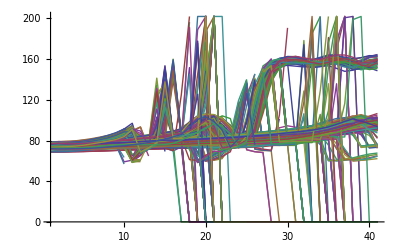

```mathematica
SetDirectory[pathdumpdata]
partialfilelist=FileNames[](*Take[FileNames[],{1,350}]*);
data=Table[Import[partialfilelist[[index]],"CSV"],{index,1,Length[partialfilelist]}];
Length[data]
fn=Select[FileNames[],StringSplit[#,"."][[2]]=="txt"&];
ListPlot[data[[All,All,9]],Joined->True,PlotRange->All]
```

```mathematica
warning=2;
nobs=2;
SetDirectory[pathdumpdata]
lfn=Length[fn]
(*preData=Table[GenerateReducedData[i],{i,1,10(*lfn*)}];*)
ConstructPreData;
normalize[preData];
Data=Map[Transpose,newX];
```

C:\Users\RHester-lab\Desktop\Population\PARFUM\iitsecdata

399

```mathematica
SplitData={};
ddd=Data;
For[ii=1,ii≤Length[ddd],ii++,
AppendTo[SplitData,SplitPatient[ddd,ii,nobs]]];
SplitData=Flatten[SplitData,1];
ClassificationData=Map[CompileData,SplitData];

Length[%]
```

5329

```mathematica
lcd=Length[ClassificationData];
R1=Range[Floor[lcd/3]];
R2=Range[Floor[lcd/3]+1,Floor[2*lcd/3]];
R3=Range[Floor[2*lcd/3]+1,lcd];
RR={R1,R2,R3};
{R1[[1]],R1[[-1]]}
{R2[[1]],R2[[-1]]}
{R3[[1]],R3[[-1]]}
TestPool1=Take[ClassificationData,{R1[[1]],R1[[-1]]}];
TestPool2=Take[ClassificationData,{R2[[1]],R2[[-1]]}];
TestPool3=Take[ClassificationData,{R3[[1]],R3[[-1]]}];
TestPool={TestPool1,TestPool2,TestPool3};
```

{1,1776}

{1777,3552}

{3553,5329}

```mathematica
EncodeTrain[train_]:=
Module[{},
SLr=train[[All,-1]];
MI=Length[train[[1]]]-1;
trlist={};
trcom="";
set=train;
For[ii=1,ii≤Length[train],ii++,
ele=set[[ii]];
ele1=ele;
FTable=Reverse[Table[index,{index,1,MI}]];
Do[
ele1=ReplacePart[ele1,FTable[[MI+1-i]]->ToString[{FTable[[i]],":",ele[[i]],"x"}]],{i,1,MI}];
ele1=Reverse[ele1];
ele1=ReplacePart[ele1,1->{ele1[[1]],"x"}];
AppendTo[trlist,ele1];
ele1=ToString[ele1];
eleOut=StringReplace[ele1,{{"{","}",","}->""," "->"","x"->" "}];
trcom=trcom<>eleOut<>"\n"];
Export[pathsvm<>"SVM_train.txt",trcom,"Text"];
];

EncodeTest[test_]:=Module[{},
MI=Length[test[[1]]]-1;
telist={};
tecom="";
set=test;
LL=Length[set];
For[ii=1,ii≤LL,ii++,
ele=set[[ii]];
ele1=ele;
FTable=Reverse[Table[index,{index,1,MI}]];
Do[
ele1=ReplacePart[ele1,FTable[[MI+1-i]]->ToString[{FTable[[i]],":",ele[[i]],"x"}]],{i,1,MI}];
ele1=Reverse[ele1];
AppendTo[telist,ele1];
ele1=ReplacePart[ele1,1->{ele1[[1]],"x"}];
ele1=ToString[ele1];
eleOut=StringReplace[ele1,{{"{","}",","}->""," "->"","x"->" "}];
tecom=tecom<>eleOut<>"\n"];
Export[pathsvm<>"SVM_full.txt",tecom,"Text"];];

EncodeSVM[train_,test_]:=Do[
EncodeTrain[train];
EncodeTest[test],{1}];

train=TestPool[[1]];
test=TestPool[[2]];(*Join[TestPool1,TestPool2,TestPool3];*)
test3=TestPool[[3]];
EncodeTrain[train]
EncodeTest[ClassificationData]
```

```mathematica
(*AnalyzeData:=Module[{Se,ErrorN,Type2,Error1,Error2,OneOut,closelist,pred},
(*import predictions*)
pred=Import["prediction.txt","Text"];
pred=ToExpression[StringInsert[StringInsert[StringReplace[pred,"\n"->","],"{",1],"}",-1]];
(*create the test set*)
tset=Join[TestPool2,TestPool3];
L=Length[tset];
(*define the observations (SLe) and the predictions (SP), with newSP the reduction to the test set*)
SLe=ClassificationData[[All,-1]][[Union[R2,R3]]];
SP=Sign[pred];
newSP=SP[[Union[R2,R3]]];
testsettry=Transpose[{newSP,SLe}];
(*Pos is the real decompensators, and FalsePos is the fake decomps (T1 errors)*)
FalsePos=Length[Select[testsettry,#[[1]]>#[[2]]&]];
Pos=Length[Select[testsettry,1==#[[2]]&]];
Type1=N[FalsePos/L];
(*Neg is the real compensators, and FalseNeg is the fake compensators (T2 errors) that we want to minimize*)
FalseNeg=Length[Select[testsettry,#[[1]]<#[[2]]&]];
Neg=Length[Select[testsettry,-1==#[[2]]&]];
Type2=N[FalseNeg/L];
(*ErorN counts the mismatches*)
ErrorN=Count[newSP*SLe,-1];
Print["Error Incidence = ",ErrorN];
Print["False positive n  = ",FalsePos];
Print["Type1 = ",Type1];
Print["Type2 = ",Type2];
OneOut=newSP[[close[3]]];
Error1=Count[OneOut,-1];
Pos=Length[Select[testsettry,1==#[[2]]&]];
Neg=Length[Select[testsettry,-1==#[[2]]&]];
Acc=N[Count[newSP*SLe,1]/L]^2;
Print["Error1 = ",Error1];
Print["Error1Rate = ",N[Error1/FalsePos]];
OneOut=newSP[[close[4]]];
Error2=Count[OneOut,-1];
Print["Error2 = ",Error2];
Print["Error2Rate = ",N[Error2/FalsePos]];
Print[];
roc=N[Table[Count[newSP[[close[k]]],1],{k,1,15}]];];*)

ShortAnalyzeData[ind_]:=
Module[{Se,ErrorN,Error1,Error2,OneOut,closelist,pred,SLe},
SetDirectory[pathsvm];
pred=Import["prediction.txt","Text"];
pred=ToExpression[StringInsert[StringInsert[StringReplace[pred,"\n"->","],"{",1],"}",-1]];
tset=TestPool[[ind]];
L=Length[tset];
SLe=ClassificationData[[All,-1]][[RR[[ind]]]];

newSP=Sign[pred][[RR[[ind]]]];
testsettry=Transpose[{newSP,SLe}];
Pos=Length[Select[testsettry,#[[2]]>0&]];
Neg=Length[Select[testsettry,#[[2]]<0&]];

predPos=Length[Select[testsettry,#[[1]]>0&]];
predNeg=Length[Select[testsettry,#[[1]]<0&]];
FalsePos=Length[Select[testsettry,#[[1]]>#[[2]]&]];
FalseNeg=Length[Select[testsettry,#[[1]]<#[[2]]&]];
sens=N[(predPos-FalsePos)/Pos];
spec=N[(predNeg-FalseNeg)/Neg];
Acc=N[Count[newSP*SLe,1]/L]^2;
Type1=N[FalsePos/L];
Type2=N[FalseNeg/L];
roc=N[Table[Count[newSP[[close[k,ind]]],1],{k,3,10}]/FalsePos]];
```

```mathematica
EncodeTrain[train]
EncodeTest[ClassificationData]
```

10

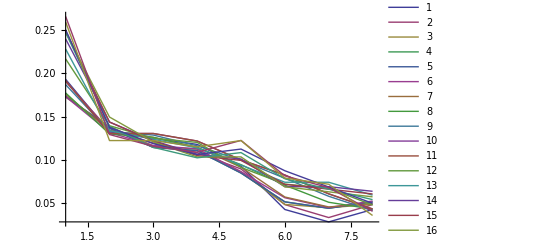

r | acc | |t2| | |nearmiss| | wasted resources | (t2/nearmiss)*(0.05t1+t2)/(0.05pos+neg) | spec*sens/((1-t1)*(1-t2))
0.01 | 0.68976 | 0.0118243 | 0.325 | 280 | 11.6276 | 0.772988
0.02 | 0.701972 | 0.0112613 | 0.324627 | 268 | 11.7708 | 0.783837
0.03 | 0.704806 | 0.0101351 | 0.310861 | 267 | 12.0015 | 0.804729
0.04 | 0.701029 | 0.0101351 | 0.309963 | 271 | 11.9923 | 0.80459
0.05 | 0.701972 | 0.00957207 | 0.309963 | 271 | 12.1388 | 0.814999
0.06 | 0.706698 | 0.00957207 | 0.304511 | 266 | 12.1293 | 0.815175
0.07 | 0.71334 | 0.00788288 | 0.30916 | 262 | 12.6443 | 0.846483
0.08 | 0.720969 | 0.00788288 | 0.307087 | 254 | 12.6525 | 0.846771
0.09 | 0.734418 | 0.00731982 | 0.319502 | 241 | 12.9041 | 0.857608
0.1 | 0.746045 | 0.00675676 | 0.321739 | 230 | 13.1351 | 0.868365
0.1 | 0.746045 | 0.00675676 | 0.321739 | 230 | 13.1351 | 0.868365
0.2 | 0.765625 | 0.00788288 | 0.355769 | 208 | 12.8897 | 0.848369
0.3 | 0.774519 | 0.00619369 | 0.361386 | 202 | 13.533 | 0.879711
0.4 | 0.786457 | 0.00731982 | 0.382979 | 188 | 13.1972 | 0.859433
0.5 | 0.793464 | 0.00731982 | 0.392265 | 181 | 13.2369 | 0.859665
0.6 | 0.798487 | 0.00844595 | 0.396552 | 174 | 12.8894 | 0.839077
0.7 | 0.803526 | 0.0101351 | 0.385542 | 166 | 12.3925 | 0.808006
0.8 | 0.808582 | 0.0106982 | 0.3875 | 160 | 12.2631 | 0.79772
0.9 | 0.819759 | 0.0118243 | 0.394558 | 147 | 12.0322 | 0.777123
1. | 0.826912 | 0.0123874 | 0.381295 | 139 | 11.8841 | 0.766839

20

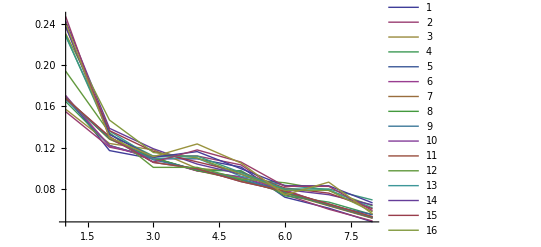

r | acc | |t2| | |nearmiss| | wasted resources | (t2/nearmiss)*(0.05t1+t2)/(0.05pos+neg) | spec*sens/((1-t1)*(1-t2))
0.01 | 0.613435 | 0.00506757 | 0.287234 | 376 | 13.4289 | 0.893464
0.02 | 0.63748 | 0.00506757 | 0.275072 | 349 | 13.4355 | 0.894653
0.03 | 0.653767 | 0.00506757 | 0.280967 | 331 | 13.4913 | 0.895421
0.04 | 0.659242 | 0.00337838 | 0.286585 | 328 | 14.4536 | 0.926344
0.05 | 0.660156 | 0.00281532 | 0.289634 | 328 | 14.8745 | 0.936586
0.06 | 0.659242 | 0.00281532 | 0.291793 | 329 | 14.8796 | 0.936542
0.07 | 0.660156 | 0.00281532 | 0.295732 | 328 | 14.8953 | 0.936586
0.08 | 0.661072 | 0.00281532 | 0.296636 | 327 | 14.9007 | 0.93663
0.09 | 0.663821 | 0.00281532 | 0.296296 | 324 | 14.9066 | 0.936761
0.1 | 0.666577 | 0.00225225 | 0.298137 | 322 | 15.4124 | 0.947082
0.1 | 0.666577 | 0.00225225 | 0.298137 | 322 | 15.4124 | 0.947082
0.2 | 0.715244 | 0.00337838 | 0.328358 | 268 | 14.7335 | 0.928845
0.3 | 0.750916 | 0.00506757 | 0.364035 | 228 | 13.9754 | 0.899473
0.4 | 0.773528 | 0.00675676 | 0.381188 | 202 | 13.366 | 0.869342
0.5 | 0.779482 | 0.00563063 | 0.373737 | 198 | 13.8158 | 0.890207
0.6 | 0.785459 | 0.00619369 | 0.376963 | 191 | 13.6016 | 0.88009
0.7 | 0.788456 | 0.00619369 | 0.361702 | 188 | 13.5676 | 0.880192
0.8 | 0.790457 | 0.00900901 | 0.370166 | 181 | 12.636 | 0.828429
0.9 | 0.800501 | 0.00957207 | 0.376471 | 170 | 12.5139 | 0.818336
1. | 0.806558 | 0.0106982 | 0.37037 | 162 | 12.2142 | 0.797661

30

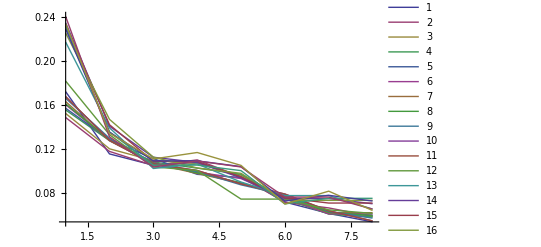

r | acc | |t2| | |nearmiss| | wasted resources | (t2/nearmiss)*(0.05t1+t2)/(0.05pos+neg) | spec*sens/((1-t1)*(1-t2))
0.01 | 0.604646 | 0.00337838 | 0.287918 | 389 | 14.3306 | 0.92358
0.02 | 0.605522 | 0.00225225 | 0.266667 | 390 | 15.1445 | 0.943944
0.03 | 0.619624 | 0.00225225 | 0.272727 | 374 | 15.2017 | 0.944709
0.04 | 0.631202 | 0.00281532 | 0.283333 | 360 | 14.7804 | 0.93515
0.05 | 0.64018 | 0.00281532 | 0.285714 | 350 | 14.8107 | 0.935606
0.06 | 0.646503 | 0.00281532 | 0.28863 | 343 | 14.8366 | 0.935921
0.07 | 0.651947 | 0.00281532 | 0.290801 | 337 | 14.8577 | 0.936189
0.08 | 0.653767 | 0.00281532 | 0.289552 | 335 | 14.858 | 0.936278
0.09 | 0.658328 | 0.00225225 | 0.296073 | 331 | 15.3833 | 0.946684
0.1 | 0.661072 | 0.00225225 | 0.295732 | 328 | 15.3895 | 0.946817
0.1 | 0.661072 | 0.00225225 | 0.295732 | 328 | 15.3895 | 0.946817
0.2 | 0.678583 | 0.00281532 | 0.314935 | 308 | 15.0061 | 0.937452
0.3 | 0.739251 | 0.00281532 | 0.356557 | 244 | 15.3008 | 0.940071
0.4 | 0.766611 | 0.0045045 | 0.375587 | 213 | 14.3319 | 0.910347
0.5 | 0.768584 | 0.0045045 | 0.374408 | 211 | 14.3341 | 0.910419
0.6 | 0.774519 | 0.00506757 | 0.372549 | 204 | 14.0591 | 0.90034
0.7 | 0.778488 | 0.00563063 | 0.366834 | 199 | 13.7946 | 0.890172
0.8 | 0.780477 | 0.00844595 | 0.364583 | 192 | 12.768 | 0.838496
0.9 | 0.788456 | 0.00900901 | 0.371585 | 183 | 12.6359 | 0.828365
1. | 0.799494 | 0.00957207 | 0.368421 | 171 | 12.4903 | 0.818305

40

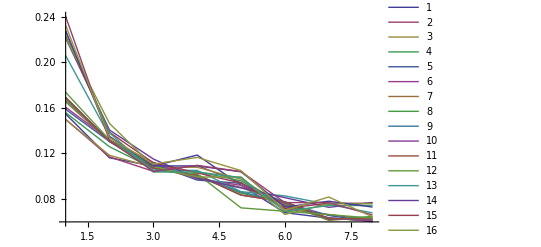

r | acc | |t2| | |nearmiss| | wasted resources | (t2/nearmiss)*(0.05t1+t2)/(0.05pos+neg) | spec*sens/((1-t1)*(1-t2))
0.01 | 0.585535 | 0.00168919 | 0.270531 | 414 | 15.7258 | 0.952936
0.02 | 0.602022 | 0.00225225 | 0.266497 | 394 | 15.1354 | 0.943749
0.03 | 0.613435 | 0.00225225 | 0.267717 | 381 | 15.1678 | 0.944376
0.04 | 0.625845 | 0.00225225 | 0.281421 | 366 | 15.2508 | 0.944369
0.05 | 0.63748 | 0.00281532 | 0.288952 | 353 | 14.8154 | 0.93547
0.06 | 0.641082 | 0.00281532 | 0.292264 | 349 | 14.8356 | 0.935651
0.07 | 0.645598 | 0.00225225 | 0.295652 | 345 | 15.3484 | 0.946054
0.08 | 0.649222 | 0.00168919 | 0.298246 | 342 | 15.9881 | 0.956402
0.09 | 0.652857 | 0.00168919 | 0.298817 | 338 | 16. | 0.956585
0.1 | 0.653767 | 0.00168919 | 0.299703 | 337 | 16.0055 | 0.95663
0.1 | 0.653767 | 0.00168919 | 0.299703 | 337 | 16.0055 | 0.95663
0.2 | 0.655589 | 0.00225225 | 0.305389 | 334 | 15.407 | 0.94655
0.3 | 0.716196 | 0.00337838 | 0.340824 | 267 | 14.7733 | 0.928885
0.4 | 0.745072 | 0.0045045 | 0.361702 | 235 | 14.2369 | 0.909534
0.5 | 0.755803 | 0.0045045 | 0.361607 | 224 | 14.2649 | 0.909943
0.6 | 0.766611 | 0.00506757 | 0.367925 | 212 | 14.026 | 0.900054
0.7 | 0.774519 | 0.00563063 | 0.364532 | 203 | 13.7784 | 0.890032
0.8 | 0.779482 | 0.00844595 | 0.362694 | 193 | 12.7608 | 0.838463
0.9 | 0.788456 | 0.00900901 | 0.371585 | 183 | 12.6359 | 0.828365
1. | 0.798487 | 0.00957207 | 0.366279 | 172 | 12.4825 | 0.818274

50

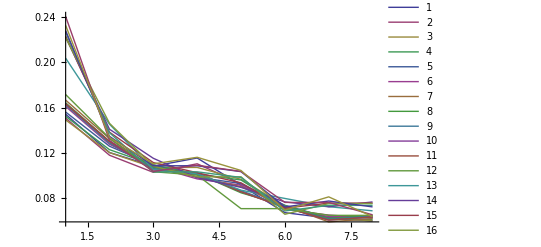

r | acc | |t2| | |nearmiss| | wasted resources | (t2/nearmiss)*(0.05t1+t2)/(0.05pos+neg) | spec*sens/((1-t1)*(1-t2))
0.01 | 0.584674 | 0.00168919 | 0.274699 | 415 | 15.739 | 0.952886
0.02 | 0.599404 | 0.00168919 | 0.268844 | 398 | 15.7539 | 0.953738
0.03 | 0.612553 | 0.00225225 | 0.269634 | 382 | 15.1728 | 0.944329
0.04 | 0.619624 | 0.00225225 | 0.275401 | 374 | 15.2114 | 0.944709
0.05 | 0.627628 | 0.00225225 | 0.282192 | 365 | 15.2558 | 0.945133
0.06 | 0.632097 | 0.00225225 | 0.288889 | 360 | 15.2905 | 0.945365
0.07 | 0.638379 | 0.00168919 | 0.299435 | 354 | 15.9627 | 0.955849
0.08 | 0.64018 | 0.00112613 | 0.294618 | 353 | 16.8094 | 0.966091
0.09 | 0.636581 | 0.00112613 | 0.291317 | 357 | 16.788 | 0.965903
0.1 | 0.632992 | 0.00112613 | 0.293629 | 361 | 16.7859 | 0.965714
0.1 | 0.632992 | 0.00112613 | 0.293629 | 361 | 16.7859 | 0.965714
0.2 | 0.652857 | 0.00168919 | 0.304734 | 338 | 16.0196 | 0.956585
0.3 | 0.709541 | 0.00281532 | 0.349091 | 275 | 15.1934 | 0.93883
0.4 | 0.745072 | 0.0045045 | 0.363248 | 234 | 14.2437 | 0.908944
0.5 | 0.755803 | 0.0045045 | 0.361607 | 224 | 14.2649 | 0.909943
0.6 | 0.766611 | 0.00506757 | 0.367925 | 212 | 14.026 | 0.900054
0.7 | 0.774519 | 0.00563063 | 0.364532 | 203 | 13.7784 | 0.890032
0.8 | 0.779482 | 0.00844595 | 0.362694 | 193 | 12.7608 | 0.838463
0.9 | 0.788456 | 0.00900901 | 0.371585 | 183 | 12.6359 | 0.828365
1. | 0.798487 | 0.00957207 | 0.366279 | 172 | 12.4825 | 0.818274

60

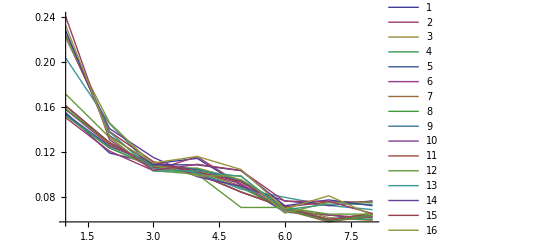

r | acc | |t2| | |nearmiss| | wasted resources | (t2/nearmiss)*(0.05t1+t2)/(0.05pos+neg) | spec*sens/((1-t1)*(1-t2))
0.01 | 0.581235 | 0.00168919 | 0.274463 | 419 | 15.7298 | 0.952682
0.02 | 0.593316 | 0.00168919 | 0.271605 | 405 | 15.749 | 0.95339
0.03 | 0.608154 | 0.00225225 | 0.276486 | 387 | 15.1871 | 0.944088
0.04 | 0.6152 | 0.00168919 | 0.276316 | 380 | 15.8214 | 0.954618
0.05 | 0.612553 | 0.00168919 | 0.279373 | 383 | 15.8256 | 0.954473
0.06 | 0.6152 | 0.00168919 | 0.284211 | 380 | 15.8496 | 0.954618
0.07 | 0.616968 | 0.00168919 | 0.285714 | 378 | 15.8594 | 0.954714
0.08 | 0.622286 | 0.00112613 | 0.286863 | 373 | 16.7331 | 0.965139
0.09 | 0.62852 | 0.00112613 | 0.289617 | 366 | 16.7598 | 0.965475
0.1 | 0.62852 | 0.00112613 | 0.289617 | 366 | 16.7598 | 0.965475
0.1 | 0.62852 | 0.00112613 | 0.289617 | 366 | 16.7598 | 0.965475
0.2 | 0.652857 | 0.00168919 | 0.304734 | 338 | 16.0196 | 0.956585
0.3 | 0.709541 | 0.00281532 | 0.349091 | 275 | 15.1934 | 0.93883
0.4 | 0.745072 | 0.0045045 | 0.363248 | 234 | 14.2437 | 0.908944
0.5 | 0.755803 | 0.0045045 | 0.361607 | 224 | 14.2649 | 0.909943
0.6 | 0.766611 | 0.00506757 | 0.367925 | 212 | 14.026 | 0.900054
0.7 | 0.774519 | 0.00563063 | 0.364532 | 203 | 13.7784 | 0.890032
0.8 | 0.779482 | 0.00844595 | 0.362694 | 193 | 12.7608 | 0.838463
0.9 | 0.788456 | 0.00900901 | 0.371585 | 183 | 12.6359 | 0.828365
1. | 0.798487 | 0.00957207 | 0.366279 | 172 | 12.4825 | 0.818274

70

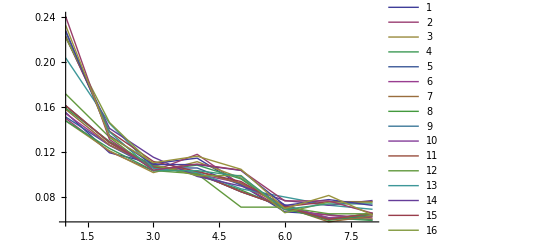

r | acc | |t2| | |nearmiss| | wasted resources | (t2/nearmiss)*(0.05t1+t2)/(0.05pos+neg) | spec*sens/((1-t1)*(1-t2))
0.01 | 0.581235 | 0.00168919 | 0.274463 | 419 | 15.7298 | 0.952682
0.02 | 0.591583 | 0.00168919 | 0.27027 | 407 | 15.7397 | 0.953289
0.03 | 0.586397 | 0.00168919 | 0.268765 | 413 | 15.7214 | 0.952987
0.04 | 0.592449 | 0.00168919 | 0.270936 | 406 | 15.7443 | 0.953339
0.05 | 0.600276 | 0.00168919 | 0.277078 | 397 | 15.7863 | 0.953787
0.06 | 0.607276 | 0.00168919 | 0.280206 | 389 | 15.8151 | 0.954181
0.07 | 0.616084 | 0.00112613 | 0.284211 | 380 | 16.707 | 0.9648
0.08 | 0.624064 | 0.00112613 | 0.28841 | 371 | 16.7434 | 0.965236
0.09 | 0.62852 | 0.00112613 | 0.289617 | 366 | 16.7598 | 0.965475
0.1 | 0.62852 | 0.00112613 | 0.289617 | 366 | 16.7598 | 0.965475
0.1 | 0.62852 | 0.00112613 | 0.289617 | 366 | 16.7598 | 0.965475
0.2 | 0.652857 | 0.00168919 | 0.304734 | 338 | 16.0196 | 0.956585
0.3 | 0.709541 | 0.00281532 | 0.349091 | 275 | 15.1934 | 0.93883
0.4 | 0.745072 | 0.0045045 | 0.363248 | 234 | 14.2437 | 0.908944
0.5 | 0.755803 | 0.0045045 | 0.361607 | 224 | 14.2649 | 0.909943
0.6 | 0.766611 | 0.00506757 | 0.367925 | 212 | 14.026 | 0.900054
0.7 | 0.774519 | 0.00563063 | 0.364532 | 203 | 13.7784 | 0.890032
0.8 | 0.779482 | 0.00844595 | 0.362694 | 193 | 12.7608 | 0.838463
0.9 | 0.788456 | 0.00900901 | 0.371585 | 183 | 12.6359 | 0.828365
1. | 0.798487 | 0.00957207 | 0.366279 | 172 | 12.4825 | 0.818274

80

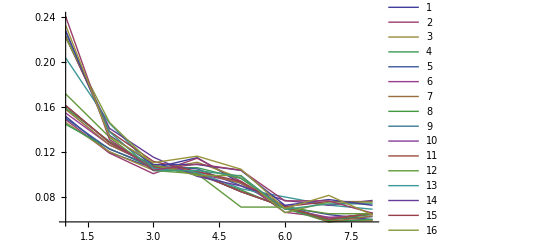

r | acc | |t2| | |nearmiss| | wasted resources | (t2/nearmiss)*(0.05t1+t2)/(0.05pos+neg) | spec*sens/((1-t1)*(1-t2))
0.01 | 0.567579 | 0.00168919 | 0.271264 | 435 | 15.6852 | 0.951855
0.02 | 0.565883 | 0.00168919 | 0.267735 | 437 | 15.6681 | 0.951751
0.03 | 0.57695 | 0.00168919 | 0.266509 | 424 | 15.69 | 0.952426
0.04 | 0.584674 | 0.00168919 | 0.26747 | 415 | 15.7123 | 0.952886
0.05 | 0.597661 | 0.00168919 | 0.2725 | 400 | 15.7631 | 0.953639
0.06 | 0.608154 | 0.00168919 | 0.280928 | 388 | 15.8199 | 0.954229
0.07 | 0.616084 | 0.00112613 | 0.284211 | 380 | 16.707 | 0.9648
0.08 | 0.624064 | 0.00112613 | 0.28841 | 371 | 16.7434 | 0.965236
0.09 | 0.62852 | 0.00112613 | 0.289617 | 366 | 16.7598 | 0.965475
0.1 | 0.62852 | 0.00112613 | 0.289617 | 366 | 16.7598 | 0.965475
0.1 | 0.62852 | 0.00112613 | 0.289617 | 366 | 16.7598 | 0.965475
0.2 | 0.652857 | 0.00168919 | 0.304734 | 338 | 16.0196 | 0.956585
0.3 | 0.709541 | 0.00281532 | 0.349091 | 275 | 15.1934 | 0.93883
0.4 | 0.745072 | 0.0045045 | 0.363248 | 234 | 14.2437 | 0.908944
0.5 | 0.755803 | 0.0045045 | 0.361607 | 224 | 14.2649 | 0.909943
0.6 | 0.766611 | 0.00506757 | 0.367925 | 212 | 14.026 | 0.900054
0.7 | 0.774519 | 0.00563063 | 0.364532 | 203 | 13.7784 | 0.890032
0.8 | 0.779482 | 0.00844595 | 0.362694 | 193 | 12.7608 | 0.838463
0.9 | 0.788456 | 0.00900901 | 0.371585 | 183 | 12.6359 | 0.828365
1. | 0.798487 | 0.00957207 | 0.366279 | 172 | 12.4825 | 0.818274

90

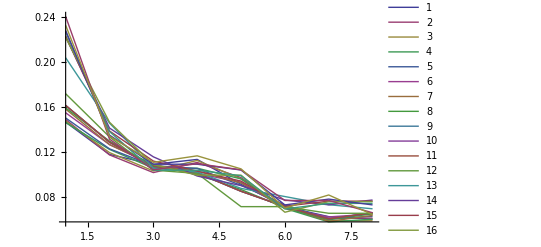

r | acc | |t2| | |nearmiss| | wasted resources | (t2/nearmiss)*(0.05t1+t2)/(0.05pos+neg) | spec*sens/((1-t1)*(1-t2))
0.01 | 0.554924 | 0.00112613 | 0.263858 | 451 | 16.4765 | 0.961152
0.02 | 0.559969 | 0.00168919 | 0.265766 | 444 | 15.6467 | 0.951382
0.03 | 0.573533 | 0.00168919 | 0.266355 | 428 | 15.6812 | 0.952219
0.04 | 0.582093 | 0.00168919 | 0.267943 | 418 | 15.7078 | 0.952733
0.05 | 0.597661 | 0.00168919 | 0.2725 | 400 | 15.7631 | 0.953639
0.06 | 0.608154 | 0.00168919 | 0.280928 | 388 | 15.8199 | 0.954229
0.07 | 0.616084 | 0.00112613 | 0.284211 | 380 | 16.707 | 0.9648
0.08 | 0.624064 | 0.00112613 | 0.28841 | 371 | 16.7434 | 0.965236
0.09 | 0.62852 | 0.00112613 | 0.289617 | 366 | 16.7598 | 0.965475
0.1 | 0.62852 | 0.00112613 | 0.289617 | 366 | 16.7598 | 0.965475
0.1 | 0.62852 | 0.00112613 | 0.289617 | 366 | 16.7598 | 0.965475
0.2 | 0.652857 | 0.00168919 | 0.304734 | 338 | 16.0196 | 0.956585
0.3 | 0.709541 | 0.00281532 | 0.349091 | 275 | 15.1934 | 0.93883
0.4 | 0.745072 | 0.0045045 | 0.363248 | 234 | 14.2437 | 0.908944
0.5 | 0.755803 | 0.0045045 | 0.361607 | 224 | 14.2649 | 0.909943
0.6 | 0.766611 | 0.00506757 | 0.367925 | 212 | 14.026 | 0.900054
0.7 | 0.774519 | 0.00563063 | 0.364532 | 203 | 13.7784 | 0.890032
0.8 | 0.779482 | 0.00844595 | 0.362694 | 193 | 12.7608 | 0.838463
0.9 | 0.788456 | 0.00900901 | 0.371585 | 183 | 12.6359 | 0.828365
1. | 0.798487 | 0.00957207 | 0.366279 | 172 | 12.4825 | 0.818274

100

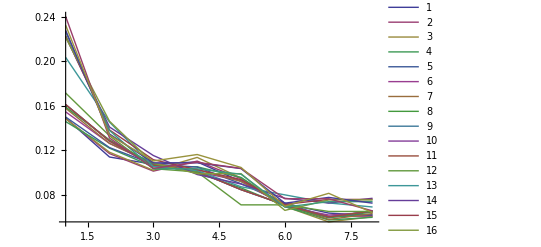

r | acc | |t2| | |nearmiss| | wasted resources | (t2/nearmiss)*(0.05t1+t2)/(0.05pos+neg) | spec*sens/((1-t1)*(1-t2))
0.01 | 0.550738 | 0.00112613 | 0.263158 | 456 | 16.4638 | 0.96088
0.02 | 0.559969 | 0.00168919 | 0.265766 | 444 | 15.6467 | 0.951382
0.03 | 0.570978 | 0.00168919 | 0.266821 | 431 | 15.6768 | 0.952064
0.04 | 0.582093 | 0.00168919 | 0.267943 | 418 | 15.7078 | 0.952733
0.05 | 0.597661 | 0.00168919 | 0.2725 | 400 | 15.7631 | 0.953639
0.06 | 0.608154 | 0.00168919 | 0.280928 | 388 | 15.8199 | 0.954229
0.07 | 0.616084 | 0.00112613 | 0.284211 | 380 | 16.707 | 0.9648
0.08 | 0.624064 | 0.00112613 | 0.28841 | 371 | 16.7434 | 0.965236
0.09 | 0.62852 | 0.00112613 | 0.289617 | 366 | 16.7598 | 0.965475
0.1 | 0.62852 | 0.00112613 | 0.289617 | 366 | 16.7598 | 0.965475
0.1 | 0.62852 | 0.00112613 | 0.289617 | 366 | 16.7598 | 0.965475
0.2 | 0.652857 | 0.00168919 | 0.304734 | 338 | 16.0196 | 0.956585
0.3 | 0.709541 | 0.00281532 | 0.349091 | 275 | 15.1934 | 0.93883
0.4 | 0.745072 | 0.0045045 | 0.363248 | 234 | 14.2437 | 0.908944
0.5 | 0.755803 | 0.0045045 | 0.361607 | 224 | 14.2649 | 0.909943
0.6 | 0.766611 | 0.00506757 | 0.367925 | 212 | 14.026 | 0.900054
0.7 | 0.774519 | 0.00563063 | 0.364532 | 203 | 13.7784 | 0.890032
0.8 | 0.779482 | 0.00844595 | 0.362694 | 193 | 12.7608 | 0.838463
0.9 | 0.788456 | 0.00900901 | 0.371585 | 183 | 12.6359 | 0.828365
1. | 0.798487 | 0.00957207 | 0.366279 | 172 | 12.4825 | 0.818274

```mathematica
jgroup=Range[10,100,10];
testgroup={0.0001,0.0005,0.001,0.005,0.01,0.025,0.05,0.075,0.1,0.25,0.5,0.75,1};(*{0.0001,0.001,0.01,0.1,1,10};*)
testgroup=Union[(*Range[0.005,0.01,0.001],*)Range[0.01,0.1,0.01],Range[0.1,1,0.1]];
R[X_,m_]:=Map[Apply[Plus,#[[1;;m]]]&,X];
EndTable={};
For[jindex=1,jindex≤Length[jgroup],jindex++,
RocTable={};
T2Table={};
T1Table={};
AccTable={};
OthTable={};
CostTable={};
Cost2Table={};

For[tindex=1,tindex≤Length[testgroup],tindex++,
Run["svm_learn -t 2 -j "<>ToString[jgroup[[jindex]]]<>" -g "<>ToString[testgroup[[tindex]]]<>" SVM_train.txt model.txt"];
Run[pathsvm<>"svm_classify "<>pathsvm<>"SVM_full.txt "<>pathsvm<>"model.txt "<>pathsvm<>"prediction.txt"];
ShortAnalyzeData[2];
AppendTo[RocTable,roc];
AppendTo[T2Table,Type2];
AppendTo[T1Table,FalsePos];
AppendTo[AccTable,Acc];
AppendTo[OthTable,(0.05*FalsePos + FalseNeg)/(0.05*Pos+Neg)];
AppendTo[CostTable,-Log[Type2^2*((0.05*FalsePos + FalseNeg)/(0.05*Pos+Neg))/R[{roc},2]]];
AppendTo[Cost2Table,sens*spec/((1-Type1)*(1-Type2))]];
Print[];
AppendTo[EndTable,CostTable];
Print[jgroup[[jindex]]];
Print[ListPlot[RocTable,Joined->True,PlotRange->All,PlotLegends->LineLegend[Automatic]]];
headings={"r","acc","|t2|","|nearmiss|","wasted resources","(t2/nearmiss)*(0.05t1+t2)/(0.05pos+neg)","spec*sens/((1-t1)*(1-t2))"};
Print[TableForm[Join[{headings},Transpose[{testgroup,AccTable,T2Table,R[RocTable,2],T1Table,-Log[T2Table^2*OthTable/R[RocTable,2]],Cost2Table}]]]]
]
```

```mathematica
Run[pathsvm<>"svm_learn -t 2 -j 90 -g 0.01 "<>pathsvm<>"SVM_train.txt "<>pathsvm<>"model.txt"];
Run[pathsvm<>"svm_classify "<>pathsvm<>"SVM_full.txt "<>pathsvm<>"model.txt "<>pathsvm<>"prediction.txt"];
ShortAnalyzeData[1];

Print["real pos = ",Pos]
Print["false pos = ",FalsePos]
Print["pred pos = ",predPos]
Print[]
Print["real neg = ",Neg]
Print["false neg = ",FalseNeg]
Print["pred neg = ",predNeg]
Print[]
Print["miss% = ",N[100*FalseNeg/Pos]]
Print["recall (sensitivity) = ",N[(predPos-FalsePos)/Pos]]
Print["specificity = ",N[(predNeg-FalseNeg)/Neg]]

eff=(FalsePos +0.05* FalseNeg)/(Pos+0.05*Neg);
Print["efficiency = ",eff]
Print["Cost = ",-Log[Type2^2*eff/R[{roc},2]][[1]]]
```

real pos = 92

false pos = 426

pred pos = 518

real neg = 1684

false neg = 0

pred neg = 1258

miss% = 0.

recall (sensitivity) = 1.

specificity = 0.747031

efficiency = 2.41771

Cost = Indeterminate

90

335

420

1687

5

1357

miss% = 5.55556

0.944444

0.801423

```mathematica
map=preData[[All,1]][[All,3]];
sbp=preData[[All,1]][[All,2]];
dbp=preData[[All,1]][[All,4]];
TV=preData[[All,1]][[All,5]];
RR=preData[[All,1]][[All,6]];
PO2=preData[[All,1]][[All,7]];
HR=preData[[All,1]][[All,8]];
Print["map ",{Mean[map],StandardDeviation[map]}]
Print["sbp ",{Mean[sbp],StandardDeviation[sbp]}]
Print["dbp ",{Mean[dbp],StandardDeviation[dbp]}]
Print["TV ",{Mean[TV],StandardDeviation[TV]}]
Print["RR ",{Mean[RR],StandardDeviation[RR]}]
Print["PO2 ",{Mean[PO2],StandardDeviation[PO2]}]
Print["HR ",{Mean[HR],StandardDeviation[HR]}]
```

map {99.4752,7.76549}

sbp {121.128,7.04079}

dbp {83.4713,8.31185}

TV {503.929,11.5961}

RR {11.5995,0.138102}

PO2 {97.7307,0.0952577}

HR {73.9168,2.12377}

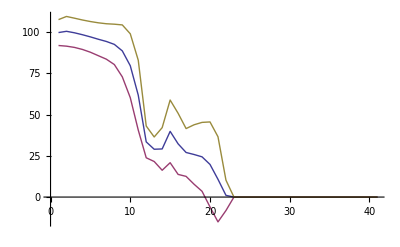

C:\Users\RHester-lab\Desktop\pressuredata1.CSV

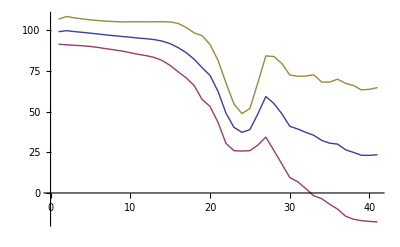

C:\Users\RHester-lab\Desktop\pressuredata2.CSV

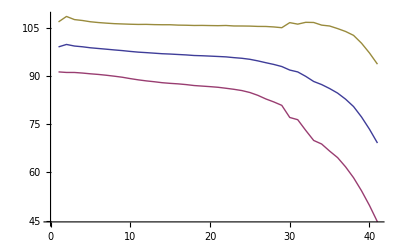

C:\Users\RHester-lab\Desktop\pressuredata3.CSV

```mathematica
s1=Select[data,#[[-1,-2]]==150&];
s2=Select[data,#[[-1,-2]]==75&];
s3=Select[data,#[[-1,-2]]==37.5&];
ms=Map[Mean,Transpose[Map[PadRight[#,41]&,s1[[All,All,3]]]]];
SDs=Map[StandardDeviation,Transpose[Map[PadRight[#,41]&,s1[[All,All,3]]]]];
ListPlot[{ms,ms-SDs,ms+SDs},Joined->True]
Export[pathdesk<>"pressuredata1.CSV",Transpose[{ms,SDs}],"CSV"]

ms=Map[Mean,Transpose[Map[PadRight[#,41]&,s2[[All,All,3]]]]];
SDs=Map[StandardDeviation,Transpose[Map[PadRight[#,41]&,s2[[All,All,3]]]]];
ListPlot[{ms,ms-SDs,ms+SDs},Joined->True]
Export[pathdesk<>"pressuredata2.CSV",Transpose[{ms,SDs}],"CSV"]

ms=Map[Mean,Transpose[Map[PadRight[#,41]&,s3[[All,All,3]]]]];
SDs=Map[StandardDeviation,Transpose[Map[PadRight[#,41]&,s3[[All,All,3]]]]];
ListPlot[{ms,ms-SDs,ms+SDs},Joined->True]
Export[pathdesk<>"pressuredata3.CSV",Transpose[{ms,SDs}],"CSV"]
(*Export[pathdesk<>"rogueHR.csv",data[[18,All,9]],"CSV"]*)
```

```mathematica
PadRight
```

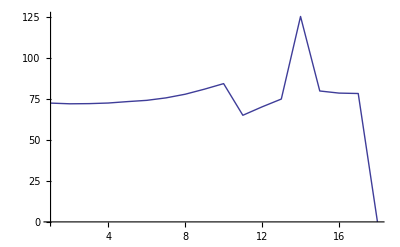

```mathematica
ListPlot[data[[18,All,9]],Joined->True,PlotRange->All]
```

```mathematica
Count[newSP,1]
Count[SLe,1]
```

189

261

```mathematica
et1=Map[Flatten,EndTable];
domain=Table[{jgroup[[j]],testgroup[[i]],et1[[j,i]]},{j,1,Length[jgroup]},{i,1,Length[testgroup]}];
gg=Flatten[domain,1];

cost=ListPlot3D[gg,PlotRange->All,Mesh->None,ColorFunction->Function[{x,y,z},Hue[z]],ViewPoint->{-250,150,50},AxesLabel->{"j","r","Cost"}]
Export[pathdata<>"cost.jpg",cost,ImageResolution->350]
```

-Graphics3D-

C:\Users\RHester-lab\Desktop\Population\PARFUM\cost.jpg

```mathematica
et3=Map[Flatten,EndTable];
domain=Table[{jgroup[[j]],testgroup[[i]],et3[[j,i]]},{j,1,Length[jgroup]},{i,1,Length[testgroup]}];
gg=Flatten[domain,1];

cost=ListPlot3D[gg,PlotRange->All,Mesh->None,ColorFunction->Function[{x,y,z},Hue[z]],ViewPoint->{-250,150,50},AxesLabel->{"j","r","Cost"}]
Export[pathdata<>"cost2.jpg",cost,ImageResolution->350]
```

-Graphics3D-

C:\Users\RHester-lab\Desktop\Population\PARFUM\cost2.jpg

```mathematica
class=Compile[{{x1,_Real},{y1,_Real},{z1,_Real},{w1,_Real},{x2,_Real},{y2,_Real},{z2,_Real},{w2,_Real},{x3,_Real},{y3,_Real},{z3,_Real},{w3,_Real},{x4,_Real},{y4,_Real},{z4,_Real},{w4,_Real}},
Module[{},
extdata=Flatten[Transpose[{({x1,x2,x3,x4}-means[[2]])/sds[[2]],({y1,y2,y3,y4}-means[[3]])/sds[[3]],({z1,z2,z3,z4}-means[[4]])/sds[[4]],({w1,w2,w3,w4}-means[[5]])/sds[[5]]}]];
EncodeTest[{extdata}];
```

```mathematica
means
sds
```

{-12.7147,95.8133,67.346,14.8213,87.9305}

{9.01961,28.2414,23.5666,6.39947,25.4255}

```mathematica
SetDirectory[pathsvm]
model1=StringSplit[Import["model.txt"],"plus 1"][[2]];
model2=StringReplace[StringSplit[model1,{"# threshold","alpha*y)\n"}],"\n"->""];
model3=StringSplit[model2[[-1]],"#"];
b=ToExpression[model2[[1]]];
svlist={};
alphalist={};
For[i=1,i≤Length[model3],i++,
newrow=model3[[i]];
broken=ToExpression[StringSplit[newrow,{"1:","2:","3:","4:","5:","6:","7:","8:","9:","10:","11:","12:"}]];
AppendTo[alphalist,broken[[1]]];
AppendTo[svlist,Drop[broken,1]]]
```

C:\Users\RHester-lab\Desktop\svm-light

```mathematica
K[j_,x_]:=alphalist[[j]]*Dot[svlist[[j]],x]
K[1,Reverse[Drop[ClassificationData[[1]],-1]]]
```

-0.430857 (0.369133 0.369133+0.369851 0.369851+0.38629 0.38629+0.470946 0.470946+0.482879 0.482879+0.488609 0.488609+1.37794 1.37794+1.38186 1.38186+1.38705 1.38705+1.40561 1.40561+1.44064 1.44064+1.4661 1.4661)

```mathematica
Reverse[Drop[ClassificationData[[1]],-1]]
```

{-0.369851,-0.470946,1.38186,1.37794,-0.369133,-0.488609,1.4661,1.44064,-0.38629,-0.482879,1.38705,1.40561}

```mathematica
svlist[[1]]

new={{107,105,81},{87,85,61},{12,12,16},{77,79,99}};
means
sds
KK[new_]:=Apply[Plus,Table[alphalist[[l]]*Dot[svlist[[l]],Reverse[Flatten[Transpose[Map[(new[[#]]-means[[#+1]])/sds[[#+1]]&,Range[4]]]]]],{l,1,Length[alphalist]}]]
```

{-0.369851,-0.470946,1.38186,1.37794,-0.369133,-0.488609,1.4661,1.44064,-0.38629,-0.482879,1.38705,1.40561}

{-12.7147,95.8133,67.346,14.8213,87.9305}

{9.01961,28.2414,23.5666,6.39947,25.4255}

```mathematica
ll=3;
jj=15;
preData[[ll,jj;;jj+2]]
New=Transpose[preData[[ll,jj;;jj+2]][[All,2;;-1]]]
KK[New]+b
```

{{-5,59.6394,42.4119,30.8523,135.939},{-4,46.6313,25.639,17.5743,85.3474},{-3,44.1491,23.4512,27.7564,85.1884}}

{{59.6394,46.6313,44.1491},{42.4119,25.639,23.4512},{30.8523,17.5743,27.7564},{135.939,85.3474,85.1884}}

154.701

```mathematica
ClassifyF=Compile[{{x1,_Real,1},{y1,_Real,1},{z1,_Real,1},{w1,_Real,1},{x2,_Real,1},{y2,_Real,1},{z2,_Real,1},{w2,_Real,1},{x3,_Real,1},{y3,_Real,1},{z3,_Real,1},{w3,_Real,1}},
Module[{Alphalist,SVlist,extdata,Means,SDS},
Alphalist={-0.43085742229590096 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.3016447801277724 ,1.027395050120915 ,5.7067477760480445 ,1.5601288087202914 ,3.4097433513976725 ,0.5710887492916709 ,-0.5379046633072178 ,4.325606151426289 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.15421100605108648 ,4.571564062680221 ,-0.35761062840810687 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,6.800911132417174 ,-0.5379046633072178 ,2.283867190438977 ,-0.5379046633072178 ,5.245350224697719 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.10090100837200401 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,4.86214313530823 ,0.7338211857571351 ,16.839112502973204 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,14.112220891408302 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.5453178457826566 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.6198896893523238 ,5.346780942163542 ,4.944725751609696 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,4.161987834338847 ,-0.5379046633072178 ,-0.5379046633072178 ,0.6555802362420583 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,5.70828737270651 ,-0.5379046633072178 ,1.646356694272347 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.1527002977153402 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.9683952346914455 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,0.008561673940757035 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,4.305263956955241 ,0.6111866485978797 ,-0.5379046633072178 ,-0.5379046633072178 ,2.0643893873883385 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,12.558643334421307 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,0.42654476963840054 ,1.271502331204058 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.466630328075566 ,4.837088994041194 ,3.984610356065579 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.756472657027905 ,-0.5379046633072178 ,-0.15968159735996432 ,-0.5379046633072178 ,-0.05168229545567247 ,5.053954529118751 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.03906148545232593 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.671194622948311 ,-0.41658885250748684 ,-0.33581690449075563 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,2.4157523936247034 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.334007022670936 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,2.3155196364341406 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.101485653413442 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,2.1821589766428944 ,-0.5379046633072178 ,3.2038008510656297 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.0719715110042096 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.401793508564496 ,-0.030695786471042198 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.9617848730804934 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.2092969288417311 ,0.41605989209285066 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.32240475603916097 ,1.0769304809250455 ,1.6145735414130697 ,-0.5379046633072178 ,-0.04703824239709883 ,1.1167521236283915 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.4453846703380776 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.8919145404144007 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.14573857174325322 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5148412108591994 ,-0.3951030295466005 ,-0.18341910873753547 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.4200386553426636 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.1040954193813834 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,0.1865769177902623 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,0.7577476538755268 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.4124155290196273 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.2557975535034186 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,0.3750552802296926 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.2452609270069488 ,-0.5379046633072178 ,-0.10372187956859354 ,-0.04150517293159994 ,-0.33359713829891857 ,0.5464737918491299 ,-0.46569589164899755 ,-0.3183130820650332 ,-0.032071267587842116 ,-0.43216724909099685 ,-0.2979907699771092 ,-0.38590896180840595 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.42383122331324813 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.4555540240556437 ,-0.5379046633072178 ,-0.48431584366607305 ,-0.5379046633072178 ,-0.5023184823322752 ,-0.5379046633072178 ,-0.19867697111994456 ,-0.2773196482883349 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.11216877546143753 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.1522236774029435 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.41023405929777335 ,-0.5379046633072178 ,-0.03959870182512156 ,-0.22026418488220328 ,-0.3307678685711174 ,0.6512368243607087 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.23524658081222752 ,-0.3107734437065557 ,-0.5379046633072178 ,-0.2912891865583973 ,-0.5379046633072178 ,-0.2950281094401684 ,-0.0012821849065098867 ,-0.33571592276640444 ,-0.5379046633072178 ,0.6020390619444087 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.2843205912129128 ,-0.14942757903963058 ,-0.07611594432133384 ,-0.07566081367671433 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.34889654131019954 ,-0.31232602377287455 ,-0.22307647712560974 ,-0.3862071455580424 ,-0.06129309453582458 ,-0.22534947884093193 ,-0.5379046633072178 ,-0.16822009192133253 ,-0.5379046633072178 ,0.3622875016829147 ,-0.5379046633072178 ,-0.20061759004908392 ,-0.22835654974679984 ,-0.10081328682426494 ,-0.2789650741928603 ,-0.2767046731852717 ,-0.13231359154316147 ,-0.08027664214843716 ,-0.13610249122407306 ,-0.03400097158524288 ,-0.02333497849232087 ,-0.014598932608741233 ,-0.32289835758301827 ,-0.14296273753956587 ,-0.5048314338611173 ,-0.12503358934457526 ,-0.2411481807197275 };
SVlist={{-0.36985099 ,-0.47094601 ,1.38186 ,1.3779401 ,-0.369133 ,-0.48860899 ,1.4661 ,1.44064 ,-0.38629001 ,-0.48287901 ,1.38705 ,1.40561 },{-0.177873 ,-0.394896 ,-0.47803801 ,-0.45220101 ,-0.25360599 ,-0.428004 ,-0.31457201 ,-0.28339201 ,-0.31650299 ,-0.44888401 ,-0.180271 ,-0.144438 },{2.8285899 ,2.68101 ,0.52291399 ,0.046072599 ,2.7675099 ,2.6682401 ,0.402695 ,-0.060671799 ,2.50811 ,2.4311399 ,0.097142898 ,-0.318028 },{-0.029093999 ,-0.35137701 ,-0.45861399 ,-0.40858299 ,-0.237912 ,-0.39833501 ,-0.45827001 ,-0.38496599 ,-0.30481401 ,-0.43470901 ,-0.310285 ,-0.242888 },{-0.55093902 ,-0.62343401 ,-1.92828 ,-1.88924 ,-0.66632998 ,-0.46401501 ,-1.8496 ,-1.7611099 ,-0.218769 ,-0.15476801 ,-0.56365001 ,-0.586178 },{-0.48603401 ,-0.34638801 ,-0.306642 ,-0.136455 ,-0.51413703 ,-0.38415599 ,0.042328801 ,0.247702 ,-0.54857498 ,-0.41379899 ,0.137383 ,0.37991199 },{-0.045498598 ,2.33251 ,-1.84644 ,-1.82302 ,-0.10785 ,2.02127 ,-1.8625799 ,-1.82938 ,-0.101597 ,0.43019199 ,-1.76975 ,-1.74149 },{-0.49438199 ,-0.47863701 ,-1.8417 ,-1.83038 ,-0.65317702 ,-0.133394 ,-1.80264 ,-1.72848 ,-0.23458 ,0.069907099 ,-0.44569701 ,-0.48564899 },{0.057422802 ,2.6027701 ,-1.63868 ,-1.66171 ,-0.0083404602 ,2.52545 ,-1.7916501 ,-1.77175 ,-0.081730299 ,1.92984 ,-1.78442 ,-1.7543499 },{-0.56117898 ,-0.59062999 ,-1.89653 ,-1.88256 ,-0.691392 ,-0.22092199 ,-1.85225 ,-1.78257 ,-0.35581401 ,-0.121371 ,-0.44856101 ,-0.51175702 },{2.7471099 ,2.58881 ,0.62853801 ,0.14115 ,2.83727 ,2.5825701 ,0.70750999 ,0.205385 ,2.93823 ,2.6643 ,0.69321603 ,0.192151 },{-0.55453002 ,-0.592623 ,-1.90089 ,-1.8696001 ,-0.69300997 ,-0.250532 ,-1.84958 ,-1.7625 ,-0.19205301 ,-0.0173099 ,-0.36778399 ,-0.42423299 },{-0.57738602 ,-0.624502 ,-1.9117399 ,-1.88808 ,-0.69974798 ,-0.389507 ,-1.83982 ,-1.7730401 ,-0.37062001 ,-0.136952 ,-0.43164301 ,-0.48230201 },{2.83727 ,2.5825701 ,0.70750999 ,0.205385 ,2.93823 ,2.6643 ,0.69321603 ,0.192151 ,2.9319401 ,2.6795299 ,0.59565699 ,0.10782 },{2.68627 ,2.55615 ,0.59492803 ,0.116207 ,2.78421 ,2.6715801 ,0.59870499 ,0.115857 ,2.83464 ,2.6900499 ,0.56009799 ,0.0792467 },{2.6994801 ,2.5634799 ,0.53814203 ,0.058436099 ,2.77755 ,2.61536 ,0.58149201 ,0.095268503 ,2.84776 ,2.7244799 ,0.57868701 ,0.096764401 },{2.17606 ,2.7997501 ,-0.83479702 ,-1.0946 ,-0.329317 ,-0.51785302 ,-1.91034 ,-1.88064 ,-0.60935599 ,-0.58062798 ,-1.94935 ,-1.86812 },{-0.55698198 ,-0.65123701 ,-1.92147 ,-1.87446 ,-0.70342201 ,-0.221581 ,-1.86523 ,-1.74959 ,-0.0039973701 ,-0.0184165 ,-0.108729 ,-0.205182 },{-0.45185801 ,0.61726302 ,-1.50764 ,-1.47261 ,-0.391655 ,-0.85407102 ,-1.15501 ,-1.1321599 ,2.1786399 ,2.52828 ,-0.060439199 ,-0.44830799 },{-0.61597002 ,-0.58215302 ,-1.93102 ,-1.87801 ,-0.75984597 ,-0.45197999 ,-1.86879 ,-1.75538 ,-0.043200999 ,-0.12942401 ,-0.345938 ,-0.40936601 },{-0.60935599 ,-0.58062798 ,-1.94935 ,-1.86812 ,-0.76930201 ,-0.401124 ,-1.90273 ,-1.76169 ,0.0121859 ,-0.120015 ,-0.53606701 ,-0.558321 },{-0.48992801 ,-0.53456402 ,-1.85604 ,-1.8329 ,-0.64348 ,-0.147938 ,-1.81754 ,-1.73448 ,-0.066743597 ,0.093681201 ,-0.238594 ,-0.311784 },{2.73823 ,2.6858101 ,0.5431 ,0.073890999 ,2.6673501 ,2.6368401 ,0.479137 ,0.020786401 ,2.68047 ,2.6264 ,0.49896199 ,0.0348715 },{-0.43985599 ,-0.36795199 ,-0.24956299 ,-0.098561801 ,-0.51246202 ,-0.387337 ,0.0104473 ,0.199754 ,-0.55708802 ,-0.43437201 ,0.19737799 ,0.42138699 },{-0.30294099 ,2.1609199 ,-1.49273 ,-1.53207 ,-0.27901199 ,1.0545 ,-1.42844 ,-1.4642 ,2.4244101 ,2.81229 ,-0.171983 ,-0.58504403 },{-0.069212899 ,2.4273 ,-1.74176 ,-1.7388999 ,-0.15291899 ,2.0741401 ,-1.77197 ,-1.7553 ,-0.16803201 ,0.57258499 ,-1.6824 ,-1.6709599 },{2.237 ,2.4198999 ,-0.32637399 ,-0.661322 ,1.2147599 ,1.5848 ,-1.00115 ,-1.1701601 ,-0.205908 ,0.038980301 ,-1.72165 ,-1.68753 },{0.0204395 ,2.3046701 ,-1.65773 ,-1.67388 ,-0.075582199 ,2.01719 ,-1.69653 ,-1.69666 ,-0.113265 ,0.63132203 ,-1.63789 ,-1.63495 },{-0.0083404602 ,2.52545 ,-1.7916501 ,-1.77175 ,-0.081730299 ,1.92984 ,-1.78442 ,-1.7543499 ,-0.050763201 ,0.14000399 ,-1.6423301 ,-1.62286 },{-0.226796 ,2.4669299 ,-1.66996 ,-1.64863 ,-0.230856 ,2.23013 ,-1.66851 ,-1.64934 ,-0.235108 ,2.0269799 ,-1.6638499 ,-1.6489201 },{1.7954299 ,1.93253 ,-0.54205 ,-0.82942599 ,0.25045401 ,0.44954899 ,-1.47501 ,-1.54229 ,-0.218813 ,-0.19314501 ,-1.6318901 ,-1.66422 },{-0.45433301 ,-0.35253599 ,-0.255889 ,-0.0944447 ,-0.52865797 ,-0.36388701 ,-0.107479 ,0.096469 ,-0.579849 ,-0.40415901 ,0.026384801 ,0.28035101 },{-0.15291899 ,2.0741401 ,-1.77197 ,-1.7553 ,-0.16803201 ,0.57258499 ,-1.6824 ,-1.6709599 ,1.6465501 ,2.16909 ,-1.06523 ,-1.2784801 },{2.2765901 ,2.30494 ,-0.16926201 ,-0.54150498 ,1.20191 ,1.48857 ,-0.997706 ,-1.17874 ,-0.193909 ,-0.034193899 ,-1.6511101 ,-1.63486 },{-0.47681299 ,-0.393226 ,-0.29125899 ,-0.117766 ,-0.47738901 ,-0.40435201 ,-0.034136999 ,0.13978299 ,-0.47990099 ,-0.41411701 ,0.0873385 ,0.290425 },{-0.461178 ,-0.32709301 ,-0.213617 ,-0.051886 ,-0.527982 ,-0.37231901 ,0.0131514 ,0.18657599 ,-0.56089503 ,-0.41217801 ,0.118575 ,0.34421501 },{-0.64174998 ,-0.42485499 ,-0.229037 ,0.037169602 ,-0.67896199 ,-0.43097201 ,-0.123056 ,0.175745 ,-0.71099901 ,-0.467742 ,-0.039832301 ,0.28405899 },{-0.64819801 ,-0.422346 ,-0.205533 ,0.054673899 ,-0.685027 ,-0.44229099 ,-0.111565 ,0.17514899 ,-0.71504802 ,-0.47668299 ,-0.030030901 ,0.29276001 },{-0.27397799 ,2.1131001 ,-1.62032 ,-1.6083 ,-0.266049 ,1.83109 ,-1.6420701 ,-1.62799 ,-0.271054 ,1.66913 ,-1.64862 ,-1.62779 },{-0.38162199 ,2.97119 ,-1.47177 ,-1.49371 ,-0.39051601 ,1.7999001 ,-1.57617 ,-1.5678101 ,-0.44754499 ,1.74252 ,-1.58883 ,-1.5558 },{-0.460715 ,-0.36855 ,-0.227332 ,-0.033380099 ,-0.530186 ,-0.39568999 ,-0.085761599 ,0.16253901 ,-0.59602797 ,-0.41197801 ,-0.0146496 ,0.26738301 },{-0.215011 ,2.1488099 ,-1.6680599 ,-1.64537 ,-0.217658 ,1.9351799 ,-1.68662 ,-1.66256 ,-0.227778 ,1.78416 ,-1.6907901 ,-1.66553 },{2.0148399 ,2.1691401 ,-0.35512501 ,-0.67272902 ,1.07245 ,1.3701299 ,-1.03626 ,-1.20781 ,-0.228002 ,0.0436919 ,-1.69059 ,-1.66395 },{2.2402201 ,2.3133399 ,-0.282731 ,-0.62810099 ,1.0343 ,1.26948 ,-1.0822099 ,-1.2395101 ,-0.281526 ,-0.13518301 ,-1.72653 ,-1.69677 },{2.1786399 ,2.52828 ,-0.060439199 ,-0.44830799 ,1.08571 ,1.5562299 ,-0.88032103 ,-1.07649 ,-0.318023 ,0.0762458 ,-1.61736 ,-1.60434 },{2.1815801 ,2.3522201 ,-0.30102301 ,-0.622024 ,1.42857 ,1.81375 ,-0.88925803 ,-1.09053 ,0.096813202 ,0.468463 ,-1.58759 ,-1.61891 },{-0.19932599 ,-0.35404 ,-0.380211 ,-0.314459 ,-0.39764401 ,-0.40700001 ,-0.274167 ,-0.177507 ,-0.48568401 ,-0.40620801 ,-0.13505299 ,0.026514901 },{-0.42692301 ,-0.405139 ,-0.41048801 ,-0.224141 ,-0.438247 ,-0.433898 ,-0.154075 ,0.0156123 ,-0.46546599 ,-0.42804101 ,-0.052073199 ,0.131062 },{-0.342922 ,-0.354581 ,-0.49551201 ,-0.40340701 ,-0.44109499 ,-0.36853001 ,-0.215343 ,-0.107095 ,-0.51639301 ,-0.37791201 ,-0.048984401 ,0.113382 },{-0.39764401 ,-0.40700001 ,-0.274167 ,-0.177507 ,-0.48568401 ,-0.40620801 ,-0.13505299 ,0.026514901 ,-0.555475 ,-0.392387 ,-0.00925982 ,0.197135 },{2.0264299 ,2.184 ,-0.351576 ,-0.68924397 ,0.61105198 ,0.79348201 ,-1.22425 ,-1.35356 ,-0.23898 ,-0.192543 ,-1.63196 ,-1.65258 },{-0.41498101 ,-0.29164001 ,-0.69196397 ,-0.480784 ,-0.449496 ,-0.40057799 ,-0.13112 ,0.071545899 ,-0.534181 ,-0.420827 ,-0.052162498 ,0.170489 },{-0.36166799 ,-0.325804 ,-0.578475 ,-0.42420799 ,-0.45433301 ,-0.35253599 ,-0.255889 ,-0.0944447 ,-0.52865797 ,-0.36388701 ,-0.107479 ,0.096469 },{-0.42260599 ,-0.37893 ,-0.47896799 ,-0.30290499 ,-0.47681299 ,-0.393226 ,-0.29125899 ,-0.117766 ,-0.47738901 ,-0.40435201 ,-0.034136999 ,0.13978299 },{1.8505501 ,2.2056799 ,-0.56082797 ,-0.83482999 ,0.63618201 ,0.95371199 ,-1.31619 ,-1.40729 ,-0.40667999 ,-0.30059701 ,-1.80239 ,-1.7618901 },{2.4203601 ,2.52352 ,0.0350057 ,-0.34858701 ,2.0148399 ,2.1691401 ,-0.35512501 ,-0.67272902 ,1.07245 ,1.3701299 ,-1.03626 ,-1.20781 },{1.14293 ,1.4872299 ,-1.0055 ,-1.19311 ,-0.23242199 ,-0.0187495 ,-1.6814899 ,-1.67468 ,-0.47695699 ,-0.29042301 ,-1.7695301 ,-1.7115901 },{-0.230856 ,2.23013 ,-1.66851 ,-1.64934 ,-0.235108 ,2.0269799 ,-1.6638499 ,-1.6489201 ,-0.249768 ,1.9430701 ,-1.66285 ,-1.6445301 },{1.88535 ,1.9822201 ,-0.45642999 ,-0.769804 ,0.60422403 ,0.74663401 ,-1.27729 ,-1.39176 ,-0.266231 ,-0.20969599 ,-1.67129 ,-1.67082 },{1.20191 ,1.48857 ,-0.997706 ,-1.17874 ,-0.193909 ,-0.034193899 ,-1.6511101 ,-1.63486 ,-0.44122401 ,-0.32428199 ,-1.73183 ,-1.6806901 },{2.0327401 ,2.2309401 ,-0.39886999 ,-0.72122902 ,0.71581697 ,1.04319 ,-1.2124799 ,-1.33518 ,-0.38325399 ,-0.27631301 ,-1.7532901 ,-1.72973 },{-0.39274499 ,-0.383578 ,-0.698865 ,-0.48252699 ,-0.42692301 ,-0.405139 ,-0.41048801 ,-0.224141 ,-0.438247 ,-0.433898 ,-0.154075 ,0.0156123 },{2.7315099 ,2.6323199 ,0.34645501 ,-0.113759 ,2.3008599 ,2.3132901 ,-0.091397204 ,-0.46981001 ,1.29282 ,1.46737 ,-0.86670202 ,-1.07897 },{-0.33874801 ,-0.34710601 ,-0.65330201 ,-0.46906999 ,-0.42260599 ,-0.37893 ,-0.47896799 ,-0.30290499 ,-0.47681299 ,-0.393226 ,-0.29125899 ,-0.117766 },{-0.22920799 ,1.77343 ,-1.5327801 ,-1.54125 ,-0.226796 ,2.4669299 ,-1.66996 ,-1.64863 ,-0.230856 ,2.23013 ,-1.66851 ,-1.64934 },{2.5269799 ,2.5046101 ,0.0085712103 ,-0.36640999 ,2.02191 ,2.16575 ,-0.420398 ,-0.71796399 ,0.947568 ,1.22241 ,-1.14038 ,-1.27665 },{-0.51639301 ,-0.37791201 ,-0.048984401 ,0.113382 ,-0.56310999 ,-0.40846899 ,0.107371 ,0.31235299 ,-0.59959 ,-0.42795101 ,0.181894 ,0.43457699 },{-0.30913901 ,1.90414 ,-1.6325099 ,-1.64193 ,-0.272302 ,0.670304 ,-1.5641 ,-1.57965 ,2.1380501 ,2.72721 ,-0.52232802 ,-0.85924399 },{-0.52393502 ,-0.454301 ,-1.80164 ,-1.7535501 ,-0.599666 ,-0.37612399 ,-1.74081 ,-1.65711 ,-0.29273 ,-0.081024401 ,-0.95623499 ,-0.94178802 },{-0.53039801 ,-0.43676901 ,-1.8092 ,-1.72837 ,-0.59672201 ,-0.47041699 ,-1.75416 ,-1.64485 ,-0.28703901 ,-0.186574 ,-0.93329197 ,-0.926772 },{-0.697577 ,-0.463673 ,-1.89389 ,-1.78495 ,-0.899472 ,-0.55027699 ,-1.90965 ,-1.70061 ,-0.140008 ,-0.30808899 ,-0.96523601 ,-0.90031397 },{-0.35853499 ,-0.38879699 ,-0.449527 ,-0.298924 ,-0.39839599 ,-0.415999 ,-0.229893 ,-0.091124304 ,-0.44555399 ,-0.41389301 ,-0.121824 ,0.0228751 },{-0.50111902 ,-0.67934799 ,-1.88108 ,-1.88151 ,-0.65262699 ,-0.387795 ,-1.86069 ,-1.80838 ,-0.47456801 ,0.14961 ,-0.85486102 ,-0.794568 },{-0.31248701 ,-0.38983101 ,-0.331063 ,-0.223719 ,-0.37138501 ,-0.41486201 ,-0.16463099 ,-0.053566702 ,-0.415544 ,-0.42418501 ,-0.046705801 ,0.074121296 },{-0.31362399 ,-0.428597 ,-0.32932499 ,-0.20869599 ,-0.377877 ,-0.455634 ,-0.212194 ,-0.082707599 ,-0.41604999 ,-0.456103 ,-0.116327 ,0.0303072 },{-0.394651 ,-0.39768001 ,-0.257173 ,-0.181097 ,-0.48228601 ,-0.38217801 ,-0.0554129 ,0.070101202 ,-0.541421 ,-0.38639599 ,0.133496 ,0.32137501 },{-0.390598 ,-0.59631097 ,-1.90371 ,-1.8784 ,-0.56021702 ,-0.49265301 ,-1.88173 ,-1.81292 ,-0.18957099 ,0.40740299 ,-0.92425603 ,-0.86726701 },{-0.59643799 ,-0.78276199 ,-1.98956 ,-1.93171 ,-0.76606601 ,-0.65218598 ,-1.94655 ,-1.83176 ,-0.173307 ,-0.095834501 ,-0.56457001 ,-0.57927603 },{-0.60509998 ,-0.69724798 ,-1.8616 ,-1.78995 ,-0.655168 ,-0.514817 ,-1.76569 ,-1.63758 ,-0.27448899 ,-0.238603 ,-0.94574302 ,-0.93617201 },{-0.56905299 ,-0.71612298 ,-1.94894 ,-1.91871 ,-0.68669701 ,-0.43660399 ,-1.89757 ,-1.81323 ,-0.35347 ,-0.150465 ,-0.64839703 ,-0.66091198 },{-0.40763 ,-0.70490003 ,-1.97332 ,-1.90819 ,-0.58071297 ,-0.74846298 ,-1.94643 ,-1.83617 ,-0.33059701 ,0.150481 ,-1.22298 ,-1.1399601 },{-1.07848 ,-0.71208799 ,-1.9371901 ,-1.7253 ,-0.97277999 ,-0.409704 ,-1.7665401 ,-1.58188 ,-0.00040752001 ,-0.26091999 ,-0.87029701 ,-0.82740599 },{-0.316912 ,1.67272 ,-1.44135 ,-1.4876 ,-0.26623201 ,0.31506899 ,-1.35312 ,-1.41237 ,1.63605 ,2.6740699 ,-0.667669 ,-0.94714898 },{-0.27388299 ,-0.34599799 ,-0.59898698 ,-0.456094 ,-0.35853499 ,-0.38879699 ,-0.449527 ,-0.298924 ,-0.39839599 ,-0.415999 ,-0.229893 ,-0.091124304 },{-0.227593 ,-0.39926901 ,-0.443203 ,-0.33223999 ,-0.31362399 ,-0.428597 ,-0.32932499 ,-0.20869599 ,-0.377877 ,-0.455634 ,-0.212194 ,-0.082707599 },{-0.18782701 ,-0.28569001 ,-0.84867603 ,-0.753968 ,-0.342922 ,-0.354581 ,-0.49551201 ,-0.40340701 ,-0.44109499 ,-0.36853001 ,-0.215343 ,-0.107095 },{-0.174539 ,-0.33394599 ,-0.70709002 ,-0.60405999 ,-0.249733 ,-0.364382 ,-0.54157197 ,-0.429979 ,-0.31248701 ,-0.38983101 ,-0.331063 ,-0.223719 },{-0.89346498 ,-0.98246402 ,-2.0870099 ,-1.88922 ,-1.1202199 ,-0.67637902 ,-2.0695801 ,-1.82213 ,-0.18782701 ,-0.28569001 ,-0.84867603 ,-0.753968 },{-0.52865797 ,-0.36388701 ,-0.107479 ,0.096469 ,-0.579849 ,-0.40415901 ,0.026384801 ,0.28035101 ,-0.602516 ,-0.433851 ,0.13807601 ,0.43681601 },{-0.28800899 ,2.1128099 ,-1.67734 ,-1.6521 ,-0.28866601 ,1.88073 ,-1.69707 ,-1.67037 ,-0.30568799 ,1.76563 ,-1.70219 ,-1.67032 },{-0.59213102 ,-0.643098 ,-1.94319 ,-1.85054 ,-0.70872599 ,-0.345698 ,-1.87154 ,-1.71683 ,0.21072499 ,0.155039 ,-0.41384199 ,-0.40710199 },{-0.596609 ,-0.74045902 ,-1.9688801 ,-1.92242 ,-0.73485601 ,-0.455897 ,-1.91758 ,-1.82127 ,-0.109012 ,-0.12784301 ,-0.26670101 ,-0.34254301 },{-0.59106898 ,-0.79260498 ,-1.99778 ,-1.89132 ,-0.73608702 ,-0.27653801 ,-1.90889 ,-1.72447 ,0.15775301 ,-0.031272698 ,-0.318771 ,-0.33191699 },{-0.117663 ,0.24482401 ,-0.77033198 ,-0.79293102 ,0.112241 ,0.000234835 ,-0.29035801 ,-0.316874 ,-0.190391 ,-0.18465599 ,0.0123837 ,0.0333279 },{-0.48361099 ,-0.27114201 ,-1.34988 ,-1.1418999 ,-0.42763999 ,-0.26891899 ,-0.72074699 ,-0.51858401 ,-0.44977099 ,-0.351504 ,-0.12202 ,0.057933901 },{-0.33357999 ,-0.31948099 ,-0.73286998 ,-0.56585401 ,-0.43985599 ,-0.36795199 ,-0.24956299 ,-0.098561801 ,-0.51246202 ,-0.387337 ,0.0104473 ,0.199754 },{-0.31650299 ,-0.44888401 ,-0.180271 ,-0.144438 ,-0.37883699 ,-0.46757299 ,-0.076062903 ,-0.028822601 ,-0.430089 ,-0.467219 ,0.0037596601 ,0.076342203 },{-0.64312202 ,-0.58669001 ,-1.97359 ,-1.84273 ,-0.80583501 ,-0.29121399 ,-1.89554 ,-1.67731 ,0.073818497 ,-0.14703199 ,-0.341409 ,-0.34113199 },{1.07245 ,1.3701299 ,-1.03626 ,-1.20781 ,-0.228002 ,0.0436919 ,-1.69059 ,-1.66395 ,-0.48329699 ,-0.229718 ,-1.77554 ,-1.70315 },{-1.02628 ,-1.08786 ,-2.0803499 ,-1.8026 ,-1.11033 ,-0.74712998 ,-2.0322499 ,-1.74186 ,-0.260851 ,-0.333318 ,-1.1055599 ,-0.98385602 },{-0.33059701 ,0.150481 ,-1.22298 ,-1.1399601 ,0.098122299 ,0.141008 ,-0.33658499 ,-0.28236499 ,-0.18668599 ,-0.210713 ,0.21953601 ,0.26765901 },{-0.42534199 ,-0.696652 ,-1.90222 ,-1.90774 ,-0.57738602 ,-0.624502 ,-1.9117399 ,-1.88808 ,-0.69974798 ,-0.389507 ,-1.83982 ,-1.7730401 },{-0.35040101 ,0.205406 ,-1.0217299 ,-0.99478698 ,0.20005199 ,-0.052912399 ,-0.20008101 ,-0.27470201 ,-0.084156401 ,-0.21088199 ,0.034771699 ,0.0165623 },{-0.45638499 ,2.7051301 ,-1.37955 ,-1.40801 ,-0.46164101 ,1.54837 ,-1.4547 ,-1.46539 ,-0.47658101 ,1.0601 ,-1.40227 ,-1.4008501 },{-0.381201 ,-0.27270699 ,-1.27098 ,-1.09038 ,-0.416787 ,-0.28633401 ,-0.74531901 ,-0.582461 ,-0.461178 ,-0.32709301 ,-0.213617 ,-0.051886 },{-0.552248 ,0.24568801 ,-1.61044 ,-1.5586801 ,-0.35040101 ,0.205406 ,-1.0217299 ,-0.99478698 ,0.20005199 ,-0.052912399 ,-0.20008101 ,-0.27470201 },{-0.60966599 ,-0.95726001 ,-2.0214 ,-1.95996 ,-0.74360299 ,-0.498043 ,-1.91611 ,-1.76781 ,0.15325999 ,-0.125135 ,-0.175677 ,-0.25490201 },{-0.56943798 ,-1.10096 ,-2.1450701 ,-2.00529 ,-1.03405 ,-1.12246 ,-2.1210201 ,-1.87085 ,-0.381201 ,-0.27270699 ,-1.27098 ,-1.09038 },{-1.09594 ,-1.09278 ,-2.11043 ,-1.79855 ,-1.09394 ,-0.66014397 ,-2.03917 ,-1.72756 ,-0.234246 ,-0.31863901 ,-1.183 ,-0.985093 },{0.947568 ,1.22241 ,-1.14038 ,-1.27665 ,-0.267371 ,-0.121279 ,-1.7586401 ,-1.73623 ,-0.43252099 ,-0.43623 ,-1.79849 ,-1.75033 },{-0.61097503 ,-0.85856402 ,-1.9920599 ,-1.94777 ,-0.72547501 ,-0.53105801 ,-1.90846 ,-1.80532 ,0.0149297 ,-0.11501 ,-0.17123599 ,-0.262481 },{-0.37233999 ,-0.72350901 ,-1.9612 ,-1.91631 ,-0.58605599 ,-0.67756999 ,-1.9614 ,-1.86496 ,-0.71985298 ,-0.32992399 ,-1.88525 ,-1.72531 },{-0.46123999 ,-0.63708198 ,-1.94048 ,-1.92442 ,-0.61597002 ,-0.58215302 ,-1.93102 ,-1.87801 ,-0.75984597 ,-0.45197999 ,-1.86879 ,-1.75538 },{-0.50999999 ,-0.33664101 ,-1.50528 ,-1.2549599 ,-0.41498101 ,-0.29164001 ,-0.69196397 ,-0.480784 ,-0.449496 ,-0.40057799 ,-0.13112 ,0.071545899 },{-0.557491 ,-0.0069551002 ,-1.3772 ,-1.3679301 ,-0.038481601 ,0.153539 ,-0.611696 ,-0.701231 ,0.27509999 ,0.0090545099 ,-0.14297 ,-0.31389999 },{1.1170599 ,1.34176 ,-1.03256 ,-1.21088 ,-0.206838 ,-0.103047 ,-1.69091 ,-1.69266 ,-0.41129401 ,-0.30436301 ,-1.74326 ,-1.71732 },{-0.54032701 ,-0.0466047 ,-1.38912 ,-1.3648 ,-0.20812 ,0.069494702 ,-0.811463 ,-0.85915202 ,0.330863 ,0.0118978 ,-0.086961903 ,-0.25956401 },{-0.273458 ,-0.37778899 ,-0.612625 ,-0.53161001 ,-0.394651 ,-0.39768001 ,-0.257173 ,-0.181097 ,-0.48228601 ,-0.38217801 ,-0.0554129 ,0.070101202 },{-0.22171301 ,-0.35278499 ,-0.43092501 ,-0.318324 ,-0.30489799 ,-0.387326 ,-0.284159 ,-0.16023 ,-0.36552599 ,-0.40630499 ,-0.11039 ,0.0010059 },{-0.44883201 ,2.6096799 ,-1.30976 ,-1.34489 ,-0.487544 ,1.52837 ,-1.35675 ,-1.36387 ,-0.491034 ,0.364553 ,-1.2338001 ,-1.24149 },{-0.038481601 ,0.153539 ,-0.611696 ,-0.701231 ,0.27509999 ,0.0090545099 ,-0.14297 ,-0.31389999 ,0.446426 ,-0.095721699 ,0.130188 ,-0.0651014 },{0.27850699 ,0.0531643 ,-0.40499401 ,-0.38160199 ,-0.052423399 ,-0.18294001 ,-0.0142248 ,0.0356111 ,-0.22328199 ,-0.33468899 ,0.50130099 ,0.51566201 },{-0.483401 ,-0.83171499 ,-2.01493 ,-1.99853 ,-0.61097503 ,-0.85856402 ,-1.9920599 ,-1.94777 ,-0.72547501 ,-0.53105801 ,-1.90846 ,-1.80532 },{-0.65653098 ,-0.208425 ,-1.84056 ,-1.72875 ,0.25268 ,-0.0014511599 ,0.16 ,0.0181814 ,0.072825298 ,-0.200028 ,0.80827701 ,0.61238098 },{0.222284 ,0.41230199 ,-1.45443 ,-1.53986 ,-0.248273 ,-0.27756801 ,-1.59865 ,-1.65596 ,-0.29929999 ,-0.22552601 ,-1.60335 ,-1.64922 },{0.25045401 ,0.44954899 ,-1.47501 ,-1.54229 ,-0.218813 ,-0.19314501 ,-1.6318901 ,-1.66422 ,-0.287332 ,-0.317148 ,-1.65742 ,-1.67574 },{0.278301 ,0.45989001 ,-1.4094501 ,-1.4821399 ,-0.168859 ,-0.18622901 ,-1.62625 ,-1.65168 ,-0.29394901 ,-0.328949 ,-1.68174 ,-1.67992 },{-0.292382 ,1.8774199 ,-1.6437 ,-1.62747 ,-0.293432 ,1.70039 ,-1.64961 ,-1.63378 ,-0.302829 ,1.58016 ,-1.64647 ,-1.62854 },{-0.261466 ,1.97118 ,-1.68595 ,-1.67021 ,-0.28136799 ,1.91458 ,-1.68397 ,-1.66247 ,-0.32726899 ,1.30214 ,-1.6086 ,-1.5585099 },{-0.266049 ,1.83109 ,-1.6420701 ,-1.62799 ,-0.271054 ,1.66913 ,-1.64862 ,-1.62779 ,-0.310761 ,1.3150899 ,-1.5914299 ,-1.55238 },{-0.28866601 ,1.88073 ,-1.69707 ,-1.67037 ,-0.30568799 ,1.76563 ,-1.70219 ,-1.67032 ,-0.34096101 ,1.5853 ,-1.69496 ,-1.65188 },{0.58343601 ,-0.19973999 ,0.41368499 ,0.183549 ,0.38066599 ,-0.217299 ,0.58206302 ,0.35658699 ,0.200611 ,-0.255595 ,0.727678 ,0.50977802 },{1.0343 ,1.26948 ,-1.0822099 ,-1.2395101 ,-0.281526 ,-0.13518301 ,-1.72653 ,-1.69677 ,-0.45365101 ,-0.33498001 ,-1.7570601 ,-1.7046601 },{-0.415025 ,-0.71856898 ,-1.98667 ,-1.96371 ,-0.59643799 ,-0.78276199 ,-1.98956 ,-1.93171 ,-0.76606601 ,-0.65218598 ,-1.94655 ,-1.83176 },{-0.329317 ,-0.51785302 ,-1.91034 ,-1.88064 ,-0.60935599 ,-0.58062798 ,-1.94935 ,-1.86812 ,-0.76930201 ,-0.401124 ,-1.90273 ,-1.76169 },{-0.45114401 ,-0.36812001 ,-1.84728 ,-1.80352 ,-0.54554898 ,-0.56312698 ,-1.87058 ,-1.80952 ,-0.60509998 ,-0.69724798 ,-1.8616 ,-1.78995 },{-0.305307 ,1.88313 ,-1.5114 ,-1.56151 ,-0.30913901 ,1.90414 ,-1.6325099 ,-1.64193 ,-0.272302 ,0.670304 ,-1.5641 ,-1.57965 },{-0.302829 ,1.58016 ,-1.64647 ,-1.62854 ,-0.32880199 ,1.05744 ,-1.57275 ,-1.53975 ,-0.29021299 ,-0.162082 ,-1.40701 ,-1.37928 },{-0.27901199 ,1.0545 ,-1.42844 ,-1.4642 ,2.4244101 ,2.81229 ,-0.171983 ,-0.58504403 ,-0.144006 ,0.193735 ,-1.60719 ,-1.64597 },{-0.235108 ,2.0269799 ,-1.6638499 ,-1.6489201 ,-0.249768 ,1.9430701 ,-1.66285 ,-1.6445301 ,-0.288138 ,1.26907 ,-1.56783 ,-1.53677 },{-0.227778 ,1.78416 ,-1.6907901 ,-1.66553 ,-0.25332299 ,1.71808 ,-1.68938 ,-1.65481 ,-0.28068501 ,0.538661 ,-1.60519 ,-1.55756 },{-0.255768 ,2.17133 ,-1.68695 ,-1.6704299 ,-0.261466 ,1.97118 ,-1.68595 ,-1.67021 ,-0.28136799 ,1.91458 ,-1.68397 ,-1.66247 },{-0.30568799 ,1.76563 ,-1.70219 ,-1.67032 ,-0.34096101 ,1.5853 ,-1.69496 ,-1.65188 ,-0.35520101 ,0.370644 ,-1.5739599 ,-1.5237401 },{-0.39051601 ,1.7999001 ,-1.57617 ,-1.5678101 ,-0.44754499 ,1.74252 ,-1.58883 ,-1.5558 ,-0.45185801 ,0.61726302 ,-1.50764 ,-1.47261 },{-0.28136799 ,1.91458 ,-1.68397 ,-1.66247 ,-0.32726899 ,1.30214 ,-1.6086 ,-1.5585099 ,-0.29861599 ,0.216557 ,-1.4396 ,-1.3978601 },{-0.426092 ,-0.66667801 ,-1.91127 ,-1.91181 ,-0.57902598 ,-0.62337101 ,-1.91623 ,-1.89103 ,-0.70945501 ,-0.26904601 ,-1.8497 ,-1.76817 },{-0.35921201 ,-0.73114598 ,-1.98753 ,-1.93555 ,-0.59106898 ,-0.79260498 ,-1.99778 ,-1.89132 ,-0.73608702 ,-0.27653801 ,-1.90889 ,-1.72447 },{-0.401389 ,-0.67085499 ,-1.91403 ,-1.91008 ,-0.55135602 ,-0.58671403 ,-1.90797 ,-1.875 ,-0.68329197 ,-0.294249 ,-1.8539799 ,-1.75875 },{-0.302802 ,1.92207 ,-1.9032201 ,-1.8601 ,-0.31812301 ,1.30375 ,-1.88774 ,-1.84433 ,-0.23278201 ,-0.54916298 ,-1.59009 ,-1.64127 },{1.08571 ,1.5562299 ,-0.88032103 ,-1.07649 ,-0.318023 ,0.0762458 ,-1.61736 ,-1.60434 ,-0.51517397 ,-0.21170001 ,-1.66732 ,-1.6246099 },{1.2147599 ,1.5848 ,-1.00115 ,-1.1701601 ,-0.205908 ,0.038980301 ,-1.72165 ,-1.68753 ,-0.49786499 ,-0.40402499 ,-1.81119 ,-1.74436 },{1.29282 ,1.46737 ,-0.86670202 ,-1.07897 ,-0.14063001 ,0.042593502 ,-1.64247 ,-1.63065 ,-0.43763599 ,-0.246023 ,-1.7162499 ,-1.67068 },{-0.416787 ,-0.28633401 ,-0.74531901 ,-0.582461 ,-0.461178 ,-0.32709301 ,-0.213617 ,-0.051886 ,-0.527982 ,-0.37231901 ,0.0131514 ,0.18657599 },{-0.249733 ,-0.364382 ,-0.54157197 ,-0.429979 ,-0.31248701 ,-0.38983101 ,-0.331063 ,-0.223719 ,-0.37138501 ,-0.41486201 ,-0.16463099 ,-0.053566702 },{-0.54046297 ,-0.374199 ,-1.72049 ,-1.63889 ,-0.59934998 ,-0.44697401 ,-1.67969 ,-1.57284 ,0.087430298 ,-0.15827601 ,-0.57584602 ,-0.63434398 },{-0.219465 ,-0.27156401 ,-0.99928099 ,-0.83456701 ,-0.36166799 ,-0.325804 ,-0.578475 ,-0.42420799 ,-0.45433301 ,-0.35253599 ,-0.255889 ,-0.0944447 },{-0.28258899 ,-0.29877701 ,-1.25328 ,-1.08382 ,-0.33357999 ,-0.31948099 ,-0.73286998 ,-0.56585401 ,-0.43985599 ,-0.36795199 ,-0.24956299 ,-0.098561801 },{-0.42763999 ,-0.26891899 ,-0.72074699 ,-0.51858401 ,-0.44977099 ,-0.351504 ,-0.12202 ,0.057933901 ,-0.50565797 ,-0.39833501 ,-0.00245355 ,0.214081 },{-0.54554898 ,-0.56312698 ,-1.87058 ,-1.80952 ,-0.60509998 ,-0.69724798 ,-1.8616 ,-1.78995 ,-0.655168 ,-0.514817 ,-1.76569 ,-1.63758 },{0.89439499 ,1.18435 ,-1.09489 ,-1.25629 ,-0.19742399 ,0.00237087 ,-1.65213 ,-1.67256 ,-0.31438801 ,-0.33366799 ,-1.70279 ,-1.70495 },{-0.217658 ,1.9351799 ,-1.68662 ,-1.66256 ,-0.227778 ,1.78416 ,-1.6907901 ,-1.66553 ,-0.25332299 ,1.71808 ,-1.68938 ,-1.65481 },{0.037941098 ,2.2666299 ,-1.70268 ,-1.69552 ,-0.022184899 ,1.83841 ,-1.71022 ,-1.69393 ,-0.0075340802 ,-0.058193799 ,-1.5604 ,-1.5483299 },{-0.53280801 ,-0.68751699 ,-1.92743 ,-1.87822 ,-0.65653098 ,-0.208425 ,-1.84056 ,-1.72875 ,0.25268 ,-0.0014511599 ,0.16 ,0.0181814 },{-0.76930201 ,-0.401124 ,-1.90273 ,-1.76169 ,0.0121859 ,-0.120015 ,-0.53606701 ,-0.558321 ,-0.14772201 ,-0.192082 ,0.066454001 ,0.044500101 },{-0.58605599 ,-0.67756999 ,-1.9614 ,-1.86496 ,-0.71985298 ,-0.32992399 ,-1.88525 ,-1.72531 ,0.18474001 ,0.0021174001 ,-0.26304901 ,-0.29161799 },{-0.58328003 ,-0.73671299 ,-2.0755401 ,-1.9257801 ,-0.65653503 ,-0.86034799 ,-2.04563 ,-1.87462 ,-0.80658901 ,-0.94208598 ,-2.04054 ,-1.81955 },{-0.44109499 ,-0.36853001 ,-0.215343 ,-0.107095 ,-0.51639301 ,-0.37791201 ,-0.048984401 ,0.113382 ,-0.56310999 ,-0.40846899 ,0.107371 ,0.31235299 },{-0.39839599 ,-0.415999 ,-0.229893 ,-0.091124304 ,-0.44555399 ,-0.41389301 ,-0.121824 ,0.0228751 ,-0.458738 ,-0.42136201 ,0.00497565 ,0.179819 },{-0.30489799 ,-0.387326 ,-0.284159 ,-0.16023 ,-0.36552599 ,-0.40630499 ,-0.11039 ,0.0010059 ,-0.41433701 ,-0.42915601 ,-0.026577299 ,0.108331 },{-0.583152 ,-0.642546 ,-1.94929 ,-1.83689 ,-0.68905401 ,-0.42405599 ,-1.87185 ,-1.70621 ,0.27850699 ,0.0531643 ,-0.40499401 ,-0.38160199 },{-0.55135602 ,-0.58671403 ,-1.90797 ,-1.875 ,-0.68329197 ,-0.294249 ,-1.8539799 ,-1.75875 ,0.0049949498 ,-0.0618365 ,-0.14106899 ,-0.239099 },{0.055121999 ,0.35144401 ,-1.5454 ,-1.58768 ,-0.35277599 ,-0.324718 ,-1.71365 ,-1.7185 ,-0.44203201 ,-0.446419 ,-1.7484601 ,-1.74006 },{-0.57902598 ,-0.62337101 ,-1.91623 ,-1.89103 ,-0.70945501 ,-0.26904601 ,-1.8497 ,-1.76817 ,-0.15712 ,-0.121978 ,-0.116578 ,-0.22608 },{-0.53092498 ,-0.45814601 ,-2.0729301 ,-1.89045 ,-0.67381001 ,-0.73983502 ,-2.06949 ,-1.84721 ,-0.76274401 ,-0.90220201 ,-2.0404 ,-1.7874 },{-0.57990497 ,-0.43437701 ,-1.78736 ,-1.6867501 ,-0.62503898 ,-0.45861301 ,-1.74411 ,-1.62117 ,0.212975 ,-0.182842 ,-0.54355502 ,-0.61381 },{-0.58572298 ,-0.41341099 ,-1.75337 ,-1.67119 ,-0.63789701 ,-0.37706599 ,-1.69613 ,-1.58208 ,0.057782602 ,-0.176612 ,-0.55039299 ,-0.61827499 },{-0.40384001 ,-0.63535601 ,-1.90292 ,-1.9015599 ,-0.55453002 ,-0.592623 ,-1.90089 ,-1.8696001 ,-0.69300997 ,-0.250532 ,-1.84958 ,-1.7625 },{-0.425446 ,-0.64754802 ,-1.89623 ,-1.9062001 ,-0.56117898 ,-0.59062999 ,-1.89653 ,-1.88256 ,-0.691392 ,-0.22092199 ,-1.85225 ,-1.78257 },{-0.36031201 ,-0.73400301 ,-1.93297 ,-1.91631 ,-0.53280801 ,-0.68751699 ,-1.92743 ,-1.87822 ,-0.65653098 ,-0.208425 ,-1.84056 ,-1.72875 },{-0.445429 ,-0.71449202 ,-1.97004 ,-1.92989 ,-0.59063601 ,-0.59089398 ,-1.93952 ,-1.85461 ,-0.71430999 ,-0.162992 ,-1.82214 ,-1.66357 },{-0.67381001 ,-0.73983502 ,-2.06949 ,-1.84721 ,-0.76274401 ,-0.90220201 ,-2.0404 ,-1.7874 ,-0.93987501 ,-0.98800403 ,-2.0643699 ,-1.7615401 },{-0.58563 ,-0.46136701 ,-1.78663 ,-1.69265 ,-0.63578802 ,-0.390008 ,-1.72241 ,-1.58988 ,0.195995 ,-0.191974 ,-0.427818 ,-0.51540899 },{0.60422403 ,0.74663401 ,-1.27729 ,-1.39176 ,-0.266231 ,-0.20969599 ,-1.67129 ,-1.67082 ,-0.40661201 ,-0.28951001 ,-1.72384 ,-1.69979 },{-0.59063601 ,-0.59089398 ,-1.93952 ,-1.85461 ,-0.71430999 ,-0.162992 ,-1.82214 ,-1.66357 ,0.25319001 ,-0.114575 ,0.094636299 ,-0.0202851 },{-0.554748 ,-0.29188299 ,-1.80804 ,-1.76104 ,-0.73724699 ,0.129265 ,-1.77458 ,-1.64775 ,0.062535301 ,0.124801 ,-0.18222301 ,-0.23253199 },{-0.53177798 ,-0.36663601 ,-1.69864 ,-1.66535 ,-0.60286498 ,-0.226964 ,-1.59297 ,-1.5270801 ,-0.174945 ,-0.087338999 ,-0.38539401 ,-0.476466 },{-1.01248 ,-0.538086 ,-1.9813499 ,-1.7856801 ,-1.07848 ,-0.71208799 ,-1.9371901 ,-1.7253 ,-0.97277999 ,-0.409704 ,-1.7665401 ,-1.58188 },{-0.97558701 ,-0.58211601 ,-1.95951 ,-1.74638 ,-1.0404201 ,-0.65415102 ,-1.90021 ,-1.6745501 ,-1.03642 ,-0.37711301 ,-1.76103 ,-1.54303 },{-0.476441 ,-0.016365699 ,-1.40806 ,-1.39194 ,-0.59250301 ,0.35330299 ,-1.39413 ,-1.32656 ,0.056211501 ,0.042607199 ,-0.501086 ,-0.59375602 },{-0.43252099 ,-0.43623 ,-1.79849 ,-1.75033 ,-0.53039801 ,-0.43676901 ,-1.8092 ,-1.72837 ,-0.59672201 ,-0.47041699 ,-1.75416 ,-1.64485 },{-0.409134 ,-0.442884 ,-1.77859 ,-1.7527601 ,-0.52393502 ,-0.454301 ,-1.80164 ,-1.7535501 ,-0.599666 ,-0.37612399 ,-1.74081 ,-1.65711 },{-0.49786499 ,-0.40402499 ,-1.81119 ,-1.74436 ,-0.57990497 ,-0.43437701 ,-1.78736 ,-1.6867501 ,-0.62503898 ,-0.45861301 ,-1.74411 ,-1.62117 },{-0.50416303 ,0.0230914 ,-1.35966 ,-1.35095 ,-0.46694499 ,0.035902899 ,-1.0112799 ,-1.00991 ,0.27870101 ,-0.0858294 ,-0.21884701 ,-0.37742099 },{0.61105198 ,0.79348201 ,-1.22425 ,-1.35356 ,-0.23898 ,-0.192543 ,-1.63196 ,-1.65258 ,-0.358069 ,-0.25948101 ,-1.66855 ,-1.65931 },{-0.51644897 ,-0.040374901 ,-1.3321 ,-1.33241 ,-0.33598799 ,0.070206799 ,-0.86713201 ,-0.90319598 ,0.119314 ,-0.00275097 ,-0.29413 ,-0.41566399 },{-0.57010102 ,0.029876299 ,-1.4235899 ,-1.40127 ,-0.31446901 ,-0.052091099 ,-0.903736 ,-0.93401003 ,0.28553301 ,-0.124227 ,-0.201812 ,-0.37457699 },{-0.66495502 ,-0.15887401 ,-1.90596 ,-1.7347701 ,-0.97558701 ,-0.58211601 ,-1.95951 ,-1.74638 ,-1.0404201 ,-0.65415102 ,-1.90021 ,-1.6745501 },{0.531793 ,-0.169937 ,0.157317 ,-0.075913101 ,0.720451 ,-0.265163 ,0.33871701 ,0.071177997 ,0.64801198 ,-0.300704 ,0.260232 ,0.039958101 },{-0.83453798 ,-0.90331101 ,-2.04392 ,-1.77104 ,-1.09594 ,-1.09278 ,-2.11043 ,-1.79855 ,-1.09394 ,-0.66014397 ,-2.03917 ,-1.72756 },{-0.240475 ,-0.53166699 ,-1.82933 ,-1.84714 ,-0.48992801 ,-0.53456402 ,-1.85604 ,-1.8329 ,-0.64348 ,-0.147938 ,-1.81754 ,-1.73448 },{-0.93987501 ,-0.98800403 ,-2.0643699 ,-1.7615401 ,-1.14197 ,-1.06453 ,-2.1018 ,-1.77364 ,-0.62905198 ,-0.42179501 ,-1.57851 ,-1.34089 },{-0.67896199 ,-0.43097201 ,-0.123056 ,0.175745 ,-0.71099901 ,-0.467742 ,-0.039832301 ,0.28405899 ,-0.72749698 ,-0.490807 ,0.0452727 ,0.40292901 },{-0.340352 ,0.25058001 ,-1.52196 ,-1.50454 ,-0.50708801 ,-0.092026301 ,-1.53114 ,-1.48708 ,-0.553204 ,-0.149464 ,-1.5105 ,-1.43101 },{-0.56923401 ,0.134518 ,-1.16772 ,-1.1816601 ,-0.082200497 ,-0.015649199 ,-0.47821999 ,-0.61785698 ,0.2225 ,-0.148334 ,-0.0936848 ,-0.30739501 },{-0.168613 ,0.53954899 ,-1.2151 ,-1.25959 ,-0.54032701 ,-0.0466047 ,-1.38912 ,-1.3648 ,-0.20812 ,0.069494702 ,-0.811463 ,-0.85915202 },{0.50032502 ,1.3320301 ,-1.1469899 ,-1.27236 ,-0.552248 ,0.24568801 ,-1.61044 ,-1.5586801 ,-0.35040101 ,0.205406 ,-1.0217299 ,-0.99478698 },{2.64798 ,2.5556099 ,0.203594 ,-0.23642799 ,2.09145 ,2.1859901 ,-0.35010201 ,-0.68408501 ,0.89439499 ,1.18435 ,-1.09489 ,-1.25629 },{2.5934999 ,2.5499301 ,0.063844502 ,-0.33935499 ,2.0334301 ,2.1533401 ,-0.403328 ,-0.715608 ,0.881661 ,1.16229 ,-1.1536601 ,-1.29799 },{2.6612301 ,2.60672 ,0.235304 ,-0.190323 ,2.2765901 ,2.30494 ,-0.16926201 ,-0.54150498 ,1.20191 ,1.48857 ,-0.997706 ,-1.17874 },{2.51139 ,2.61713 ,0.0056698401 ,-0.368559 ,2.1815801 ,2.3522201 ,-0.30102301 ,-0.622024 ,1.42857 ,1.81375 ,-0.88925803 ,-1.09053 },{-0.144006 ,0.193735 ,-1.60719 ,-1.64597 ,-0.53603101 ,-0.065915003 ,-1.72637 ,-1.69879 ,-0.71122003 ,0.147808 ,-1.71667 ,-1.6133 },{-0.260851 ,-0.333318 ,-1.1055599 ,-0.98385602 ,-0.234937 ,-0.33256 ,-0.76404703 ,-0.65580201 ,-0.28547299 ,-0.36379999 ,-0.48844901 ,-0.39825499 },{0.0636613 ,0.79024899 ,-1.00458 ,-1.12104 ,-0.51644897 ,-0.040374901 ,-1.3321 ,-1.33241 ,-0.33598799 ,0.070206799 ,-0.86713201 ,-0.90319598 },{-0.36977601 ,-0.42090499 ,-0.101911 ,-0.0272756 ,-0.411484 ,-0.42969 ,-0.094998002 ,0.0278462 ,-0.48141301 ,-0.43358201 ,-0.050834101 ,0.081939697 },{-0.449496 ,-0.40057799 ,-0.13112 ,0.071545899 ,-0.534181 ,-0.420827 ,-0.052162498 ,0.170489 ,-0.604684 ,-0.42689601 ,-0.0534808 ,0.211099 },{0.97185498 ,1.07645 ,-1.10259 ,-1.26372 ,-0.187682 ,-0.121648 ,-1.66705 ,-1.67339 ,-0.347262 ,-0.35438201 ,-1.72083 ,-1.70523 },{0.881661 ,1.16229 ,-1.1536601 ,-1.29799 ,-0.168154 ,-0.029639199 ,-1.6914999 ,-1.7045799 ,-0.28432399 ,-0.322182 ,-1.73373 ,-1.72936 },{1.23627 ,1.51458 ,-1.26176 ,-1.41549 ,-0.402475 ,-0.63964701 ,-1.9075201 ,-1.86601 ,-0.57605302 ,-0.57340902 ,-1.89174 ,-1.8127199 },{0.99979001 ,1.52704 ,-0.62121099 ,-0.86761498 ,-0.39247799 ,-0.0033599799 ,-1.51035 ,-1.51533 ,-0.52005702 ,-0.174762 ,-1.52926 ,-1.5043 },{-0.488152 ,-0.048914399 ,-1.3638 ,-1.35144 ,-0.558707 ,-0.046757799 ,-1.19779 ,-1.17436 ,0.27026001 ,0.0042587901 ,-0.168109 ,-0.319846 },{-0.50708801 ,-0.092026301 ,-1.53114 ,-1.48708 ,-0.553204 ,-0.149464 ,-1.5105 ,-1.43101 ,0.170178 ,-0.16896901 ,-0.62042701 ,-0.71680802 },{-0.28163099 ,0.281656 ,-1.5661 ,-1.56422 ,-0.28800899 ,2.1128099 ,-1.67734 ,-1.6521 ,-0.28866601 ,1.88073 ,-1.69707 ,-1.67037 },{-0.29961699 ,1.6534801 ,-1.37745 ,-1.42224 ,-0.22183301 ,-0.37417501 ,-1.19363 ,-1.2646 ,0.50032502 ,1.3320301 ,-1.1469899 ,-1.27236 },{-0.022184899 ,1.83841 ,-1.71022 ,-1.69393 ,-0.0075340802 ,-0.058193799 ,-1.5604 ,-1.5483299 ,1.23627 ,1.51458 ,-1.26176 ,-1.41549 },{-0.081730299 ,1.92984 ,-1.78442 ,-1.7543499 ,-0.050763201 ,0.14000399 ,-1.6423301 ,-1.62286 ,1.38528 ,1.7555701 ,-1.22858 ,-1.40248 },{0.54685301 ,1.23452 ,-0.82395899 ,-0.99843401 ,-0.454779 ,-0.126523 ,-1.3668 ,-1.36264 ,-0.53365302 ,-0.103371 ,-1.34118 ,-1.30591 },{-0.48568401 ,-0.40620801 ,-0.13505299 ,0.026514901 ,-0.555475 ,-0.392387 ,-0.00925982 ,0.197135 ,-0.59036702 ,-0.43817899 ,0.17399199 ,0.438889 },{-0.44977099 ,-0.351504 ,-0.12202 ,0.057933901 ,-0.50565797 ,-0.39833501 ,-0.00245355 ,0.214081 ,-0.568551 ,-0.41115099 ,0.0486564 ,0.28699899 },{2.02191 ,2.16575 ,-0.420398 ,-0.71796399 ,0.947568 ,1.22241 ,-1.14038 ,-1.27665 ,-0.267371 ,-0.121279 ,-1.7586401 ,-1.73623 },{-0.067678802 ,2.39886 ,-1.75605 ,-1.74633 ,-0.139705 ,1.64821 ,-1.75275 ,-1.73931 ,2.7118101 ,2.96313 ,-0.45691699 ,-0.81745303 },{-0.491034 ,0.364553 ,-1.2338001 ,-1.24149 ,2.2792799 ,2.5727501 ,0.65552402 ,0.142839 ,1.54822 ,2.1022699 ,-0.114099 ,-0.47800499 },{2.6661899 ,2.5510001 ,0.57019299 ,0.096926004 ,2.68627 ,2.55615 ,0.59492803 ,0.116207 ,2.78421 ,2.6715801 ,0.59870499 ,0.115857 },{2.6772499 ,2.56127 ,0.55166799 ,0.0736738 ,2.7413199 ,2.59987 ,0.575625 ,0.092210002 ,2.8127699 ,2.6637299 ,0.59552097 ,0.110458 },{2.6673501 ,2.6368401 ,0.479137 ,0.020786401 ,2.68047 ,2.6264 ,0.49896199 ,0.0348715 ,2.74576 ,2.6529901 ,0.532058 ,0.062124599 },{2.68047 ,2.6264 ,0.49896199 ,0.0348715 ,2.74576 ,2.6529901 ,0.532058 ,0.062124599 ,2.77316 ,2.68748 ,0.50479901 ,0.043357801 },{2.7413199 ,2.59987 ,0.575625 ,0.092210002 ,2.8127699 ,2.6637299 ,0.59552097 ,0.110458 ,2.8285899 ,2.68101 ,0.52291399 ,0.046072599 },{2.77755 ,2.61536 ,0.58149201 ,0.095268503 ,2.84776 ,2.7244799 ,0.57868701 ,0.096764401 ,2.84635 ,2.7106299 ,0.54503602 ,0.058325302 },{-0.28547299 ,-0.36379999 ,-0.48844901 ,-0.39825499 ,-0.31753999 ,-0.39627701 ,-0.236729 ,-0.16867 ,-0.36977601 ,-0.42090499 ,-0.101911 ,-0.0272756 },{-0.237912 ,-0.39833501 ,-0.45827001 ,-0.38496599 ,-0.30481401 ,-0.43470901 ,-0.310285 ,-0.242888 ,-0.36091 ,-0.452407 ,-0.205162 ,-0.115842 },{2.0334301 ,2.1533401 ,-0.403328 ,-0.715608 ,0.881661 ,1.16229 ,-1.1536601 ,-1.29799 ,-0.168154 ,-0.029639199 ,-1.6914999 ,-1.7045799 },{2.09145 ,2.1859901 ,-0.35010201 ,-0.68408501 ,0.89439499 ,1.18435 ,-1.09489 ,-1.25629 ,-0.19742399 ,0.00237087 ,-1.65213 ,-1.67256 },{2.1247399 ,2.1552401 ,-0.262344 ,-0.60716099 ,0.97185498 ,1.07645 ,-1.10259 ,-1.26372 ,-0.187682 ,-0.121648 ,-1.66705 ,-1.67339 },{2.74576 ,2.6529901 ,0.532058 ,0.062124599 ,2.77316 ,2.68748 ,0.50479901 ,0.043357801 ,2.7526 ,2.6724701 ,0.427248 ,-0.0232228 },{2.6904399 ,2.5281999 ,0.489494 ,0.046366401 ,2.77742 ,2.5962999 ,0.49691501 ,0.0498951 ,2.8318501 ,2.68466 ,0.45539999 ,0.0133607 },{2.77316 ,2.68748 ,0.50479901 ,0.043357801 ,2.7526 ,2.6724701 ,0.427248 ,-0.0232228 ,2.6612301 ,2.60672 ,0.235304 ,-0.190323 },{2.53053 ,2.5892401 ,0.28508401 ,-0.123406 ,2.59112 ,2.6229801 ,0.306256 ,-0.105434 ,2.64167 ,2.6802101 ,0.28306299 ,-0.124422 },{2.6728699 ,2.58371 ,0.44872701 ,-0.0015814099 ,2.7848599 ,2.6463101 ,0.50715101 ,0.0457961 ,2.84462 ,2.6979599 ,0.46033099 ,0.0021752799 },{-0.25246701 ,-0.41274899 ,-0.39368501 ,-0.291913 ,-0.32653201 ,-0.44070199 ,-0.23593 ,-0.13239799 ,-0.388533 ,-0.47236401 ,-0.103611 ,0.0083012599 },{2.3008599 ,2.3132901 ,-0.091397204 ,-0.46981001 ,1.29282 ,1.46737 ,-0.86670202 ,-1.07897 ,-0.14063001 ,0.042593502 ,-1.64247 ,-1.63065 },{2.4725399 ,2.59673 ,-0.087210998 ,-0.48811901 ,1.51702 ,1.8325 ,-0.77180803 ,-1.00708 ,0.055121999 ,0.35144401 ,-1.5454 ,-1.58768 },{2.4479101 ,2.47139 ,0.021948799 ,-0.389732 ,1.41986 ,1.6603301 ,-0.75072098 ,-0.99114799 ,-0.137033 ,0.18850601 ,-1.59043 ,-1.59605 },{2.6149499 ,2.9791501 ,-0.476477 ,-0.83446699 ,0.32605499 ,0.54926503 ,-1.60681 ,-1.6888601 ,-0.425446 ,-0.64754802 ,-1.89623 ,-1.9062001 },{2.5785201 ,2.68257 ,0.28330901 ,-0.13229699 ,2.53053 ,2.5892401 ,0.28508401 ,-0.123406 ,2.59112 ,2.6229801 ,0.306256 ,-0.105434 },{-0.36091 ,-0.452407 ,-0.205162 ,-0.115842 ,-0.39345801 ,-0.450066 ,-0.12973 ,-0.020785701 ,-0.44760001 ,-0.46188101 ,-0.094852701 ,0.051766001 },{2.59112 ,2.6229801 ,0.306256 ,-0.105434 ,2.64167 ,2.6802101 ,0.28306299 ,-0.124422 ,2.6180899 ,2.73599 ,0.20759401 ,-0.19416399 },{2.84776 ,2.7244799 ,0.57868701 ,0.096764401 ,2.84635 ,2.7106299 ,0.54503602 ,0.058325302 ,2.8287301 ,2.68608 ,0.44713101 ,-0.0177394 },{2.78421 ,2.6715801 ,0.59870499 ,0.115857 ,2.83464 ,2.6900499 ,0.56009799 ,0.0792467 ,2.8178101 ,2.67665 ,0.46235701 ,-0.00754409 },{-0.71099901 ,-0.467742 ,-0.039832301 ,0.28405899 ,-0.72749698 ,-0.490807 ,0.0452727 ,0.40292901 ,-0.732274 ,-0.531515 ,0.068043701 ,0.446006 },{-0.377877 ,-0.455634 ,-0.212194 ,-0.082707599 ,-0.41604999 ,-0.456103 ,-0.116327 ,0.0303072 ,-0.464477 ,-0.44834501 ,-0.067286998 ,0.10717 },{-0.30481401 ,-0.43470901 ,-0.310285 ,-0.242888 ,-0.36091 ,-0.452407 ,-0.205162 ,-0.115842 ,-0.39345801 ,-0.450066 ,-0.12973 ,-0.020785701 },{-0.59250301 ,0.35330299 ,-1.39413 ,-1.32656 ,0.056211501 ,0.042607199 ,-0.501086 ,-0.59375602 ,0.41241699 ,-0.077164702 ,0.0727247 ,-0.098531701 },{1.42857 ,1.81375 ,-0.88925803 ,-1.09053 ,0.096813202 ,0.468463 ,-1.58759 ,-1.61891 ,-0.45114401 ,-0.36812001 ,-1.84728 ,-1.80352 },{1.65942 ,1.75237 ,-0.60687399 ,-0.87715501 ,0.278301 ,0.45989001 ,-1.4094501 ,-1.4821399 ,-0.168859 ,-0.18622901 ,-1.62625 ,-1.65168 },{1.41986 ,1.6603301 ,-0.75072098 ,-0.99114799 ,-0.137033 ,0.18850601 ,-1.59043 ,-1.59605 ,-0.46967 ,-0.281434 ,-1.70735 ,-1.66255 },{2.8127699 ,2.6637299 ,0.59552097 ,0.110458 ,2.8285899 ,2.68101 ,0.52291399 ,0.046072599 ,2.7675099 ,2.6682401 ,0.402695 ,-0.060671799 },{-0.438247 ,-0.433898 ,-0.154075 ,0.0156123 ,-0.46546599 ,-0.42804101 ,-0.052073199 ,0.131062 ,-0.49107999 ,-0.423581 ,0.020844599 ,0.242035 },{-0.32653201 ,-0.44070199 ,-0.23593 ,-0.13239799 ,-0.388533 ,-0.47236401 ,-0.103611 ,0.0083012599 ,-0.43264699 ,-0.46790799 ,-0.0250961 ,0.104143 },{-0.31753999 ,-0.39627701 ,-0.236729 ,-0.16867 ,-0.36977601 ,-0.42090499 ,-0.101911 ,-0.0272756 ,-0.411484 ,-0.42969 ,-0.094998002 ,0.0278462 },{-0.553204 ,-0.149464 ,-1.5105 ,-1.43101 ,0.170178 ,-0.16896901 ,-0.62042701 ,-0.71680802 ,0.57332301 ,-0.226611 ,-0.15935101 ,-0.34018299 },{0.71581697 ,1.04319 ,-1.2124799 ,-1.33518 ,-0.38325399 ,-0.27631301 ,-1.7532901 ,-1.72973 ,-0.50163001 ,-0.40118 ,-1.77637 ,-1.72621 },{1.52858 ,2.0661299 ,-1.14114 ,-1.33925 ,-0.401389 ,-0.67085499 ,-1.91403 ,-1.91008 ,-0.55135602 ,-0.58671403 ,-1.90797 ,-1.875 },{1.28491 ,1.77145 ,-1.26887 ,-1.42483 ,-0.445429 ,-0.71449202 ,-1.97004 ,-1.92989 ,-0.59063601 ,-0.59089398 ,-1.93952 ,-1.85461 },{1.38528 ,1.7555701 ,-1.22858 ,-1.40248 ,-0.36031201 ,-0.73400301 ,-1.93297 ,-1.91631 ,-0.53280801 ,-0.68751699 ,-1.92743 ,-1.87822 },{-0.454779 ,-0.126523 ,-1.3668 ,-1.36264 ,-0.53365302 ,-0.103371 ,-1.34118 ,-1.30591 ,0.12574001 ,0.14194299 ,-0.467179 ,-0.55853403 },{-0.162582 ,-0.38118899 ,-0.52416301 ,-0.44249001 ,-0.25246701 ,-0.41274899 ,-0.39368501 ,-0.291913 ,-0.32653201 ,-0.44070199 ,-0.23593 ,-0.13239799 },{-0.685027 ,-0.44229099 ,-0.111565 ,0.17514899 ,-0.71504802 ,-0.47668299 ,-0.030030901 ,0.29276001 ,-0.73223603 ,-0.50203198 ,0.044413999 ,0.38780099 },{-0.122367 ,-0.31121001 ,-0.56275398 ,-0.468321 ,-0.22171301 ,-0.35278499 ,-0.43092501 ,-0.318324 ,-0.30489799 ,-0.387326 ,-0.284159 ,-0.16023 },{-0.234937 ,-0.33256 ,-0.76404703 ,-0.65580201 ,-0.28547299 ,-0.36379999 ,-0.48844901 ,-0.39825499 ,-0.31753999 ,-0.39627701 ,-0.236729 ,-0.16867 },{-0.530186 ,-0.39568999 ,-0.085761599 ,0.16253901 ,-0.59602797 ,-0.41197801 ,-0.0146496 ,0.26738301 ,-0.61129898 ,-0.443149 ,0.120621 ,0.44452599 },{-0.52005702 ,-0.174762 ,-1.52926 ,-1.5043 ,-0.613419 ,0.092412397 ,-1.52136 ,-1.45416 ,0.040071901 ,0.0107922 ,-0.470254 ,-0.550973 },{-0.44203201 ,-0.446419 ,-1.7484601 ,-1.74006 ,-0.54418403 ,-0.420021 ,-1.75946 ,-1.72473 ,-0.60905701 ,-0.46899301 ,-1.70927 ,-1.63889 },{-0.47695699 ,-0.29042301 ,-1.7695301 ,-1.7115901 ,-0.56605101 ,-0.43922299 ,-1.75893 ,-1.6712199 ,-0.62308401 ,-0.51028103 ,-1.73364 ,-1.63016 },{-0.48329699 ,-0.229718 ,-1.77554 ,-1.70315 ,-0.571688 ,-0.435132 ,-1.75937 ,-1.65764 ,-0.62917298 ,-0.50149602 ,-1.73943 ,-1.6164401 },{-0.37138501 ,-0.41486201 ,-0.16463099 ,-0.053566702 ,-0.415544 ,-0.42418501 ,-0.046705801 ,0.074121296 ,-0.46354699 ,-0.42425099 ,-0.036097199 ,0.12764101 },{0.112241 ,0.000234835 ,-0.29035801 ,-0.316874 ,-0.190391 ,-0.18465599 ,0.0123837 ,0.0333279 ,-0.355544 ,-0.34289199 ,0.46074799 ,0.464398 },{-0.39345801 ,-0.450066 ,-0.12973 ,-0.020785701 ,-0.44760001 ,-0.46188101 ,-0.094852701 ,0.051766001 ,-0.48719901 ,-0.44082701 ,-0.052123599 ,0.12842 },{-0.41604999 ,-0.456103 ,-0.116327 ,0.0303072 ,-0.464477 ,-0.44834501 ,-0.067286998 ,0.10717 ,-0.50787199 ,-0.43440199 ,-0.0147436 ,0.194315 },{-0.0258995 ,0.26545599 ,-1.90461 ,-1.83376 ,-0.58328003 ,-0.73671299 ,-2.0755401 ,-1.9257801 ,-0.65653503 ,-0.86034799 ,-2.04563 ,-1.87462 },{-0.75037497 ,-0.77051598 ,-2.0669899 ,-1.83366 ,-0.83453798 ,-0.90331101 ,-2.04392 ,-1.77104 ,-1.09594 ,-1.09278 ,-2.11043 ,-1.79855 },{-0.65653503 ,-0.86034799 ,-2.04563 ,-1.87462 ,-0.80658901 ,-0.94208598 ,-2.04054 ,-1.81955 ,-1.02628 ,-1.08786 ,-2.0803499 ,-1.8026 },{-0.39247799 ,-0.0033599799 ,-1.51035 ,-1.51533 ,-0.52005702 ,-0.174762 ,-1.52926 ,-1.5043 ,-0.613419 ,0.092412397 ,-1.52136 ,-1.45416 },{-0.437572 ,-0.00968224 ,-1.5263 ,-1.51572 ,-0.525585 ,-0.1558 ,-1.546 ,-1.51169 ,-0.61639899 ,-0.0073370798 ,-1.5255001 ,-1.44638 },{0.189868 ,0.168304 ,-1.72558 ,-1.76221 ,-0.429649 ,-0.63661098 ,-1.92709 ,-1.90438 ,-0.58057398 ,-0.499475 ,-1.90058 ,-1.83241 },{-0.25360599 ,-0.428004 ,-0.31457201 ,-0.28339201 ,-0.31650299 ,-0.44888401 ,-0.180271 ,-0.144438 ,-0.37883699 ,-0.46757299 ,-0.076062903 ,-0.028822601 },{-0.44555399 ,-0.41389301 ,-0.121824 ,0.0228751 ,-0.458738 ,-0.42136201 ,0.00497565 ,0.179819 ,-0.48731199 ,-0.41607201 ,0.0573311 ,0.26092499 },{-0.28340101 ,-0.43608999 ,-0.22220699 ,-0.140257 ,-0.34995499 ,-0.45453501 ,-0.13646901 ,-0.029963201 ,-0.39449599 ,-0.47226799 ,-0.061888002 ,0.053153198 },{-0.137033 ,0.18850601 ,-1.59043 ,-1.59605 ,-0.46967 ,-0.281434 ,-1.70735 ,-1.66255 ,-0.561149 ,-0.35425699 ,-1.70249 ,-1.6345299 },{-0.31812301 ,1.30375 ,-1.88774 ,-1.84433 ,-0.23278201 ,-0.54916298 ,-1.59009 ,-1.64127 ,0.319289 ,0.33783299 ,-1.65844 ,-1.68812 },{0.63618201 ,0.95371199 ,-1.31619 ,-1.40729 ,-0.40667999 ,-0.30059701 ,-1.80239 ,-1.7618901 ,-0.51746798 ,-0.36562601 ,-1.8128 ,-1.74312 },{-0.53603101 ,-0.065915003 ,-1.72637 ,-1.69879 ,-0.71122003 ,0.147808 ,-1.71667 ,-1.6133 ,-0.019429401 ,-0.0728034 ,-0.329961 ,-0.39650699 },{-0.13780899 ,0.47548899 ,-1.47956 ,-1.49418 ,-0.53100401 ,-0.174977 ,-1.63183 ,-1.58724 ,-0.59403801 ,-0.28427401 ,-1.6278 ,-1.55889 },{-0.534181 ,-0.420827 ,-0.052162498 ,0.170489 ,-0.604684 ,-0.42689601 ,-0.0534808 ,0.211099 ,-0.64628899 ,-0.44086599 ,0.0548064 ,0.349475 },{-0.193234 ,-0.378813 ,-0.37157199 ,-0.30989501 ,-0.267694 ,-0.42056 ,-0.225105 ,-0.160762 ,-0.321646 ,-0.43732801 ,-0.13767 ,-0.060113899 },{-0.44760001 ,-0.46188101 ,-0.094852701 ,0.051766001 ,-0.48719901 ,-0.44082701 ,-0.052123599 ,0.12842 ,-0.52971298 ,-0.427607 ,0.038198501 ,0.22990499 },{1.51702 ,1.8325 ,-0.77180803 ,-1.00708 ,0.055121999 ,0.35144401 ,-1.5454 ,-1.58768 ,-0.35277599 ,-0.324718 ,-1.71365 ,-1.7185 },{-1.0404201 ,-0.65415102 ,-1.90021 ,-1.6745501 ,-1.03642 ,-0.37711301 ,-1.76103 ,-1.54303 ,0.073750697 ,-0.276932 ,-0.70215499 ,-0.67131698 },{-0.429649 ,-0.63661098 ,-1.92709 ,-1.90438 ,-0.58057398 ,-0.499475 ,-1.90058 ,-1.83241 ,-0.56290299 ,0.111542 ,-1.3688999 ,-1.25494 },{-0.34096101 ,1.5853 ,-1.69496 ,-1.65188 ,-0.35520101 ,0.370644 ,-1.5739599 ,-1.5237401 ,2.70943 ,2.65312 ,0.32641599 ,-0.114866 },{-0.119025 ,2.33902 ,-1.8569 ,-1.8200001 ,-0.172023 ,1.98103 ,-1.8634599 ,-1.81856 ,-0.15869799 ,0.26809001 ,-1.74342 ,-1.70489 },{-0.293432 ,1.70039 ,-1.64961 ,-1.63378 ,-0.302829 ,1.58016 ,-1.64647 ,-1.62854 ,-0.32880199 ,1.05744 ,-1.57275 ,-1.53975 },{-0.57986897 ,0.045539901 ,-1.2108001 ,-1.19098 ,0.115686 ,0.115549 ,-0.34560701 ,-0.476349 ,0.44345501 ,0.036944401 ,0.111838 ,-0.076875597 },{-0.44754499 ,1.74252 ,-1.58883 ,-1.5558 ,-0.45185801 ,0.61726302 ,-1.50764 ,-1.47261 ,-0.391655 ,-0.85407102 ,-1.15501 ,-1.1321599 },{-0.53489703 ,-0.35825899 ,-1.73311 ,-1.67487 ,-0.60336602 ,-0.41812301 ,-1.69277 ,-1.60393 ,-0.21834099 ,-0.125229 ,-0.85875702 ,-0.868177 },{-0.49555099 ,-0.31160799 ,-1.70184 ,-1.66415 ,-0.57352298 ,-0.366005 ,-1.6698101 ,-1.6094 ,-0.31694299 ,-0.054770902 ,-0.89760798 ,-0.90527701 },{-0.56605101 ,-0.43922299 ,-1.75893 ,-1.6712199 ,-0.62308401 ,-0.51028103 ,-1.73364 ,-1.63016 ,-0.39979199 ,-0.219253 ,-1.0386 ,-1.02126 },{-0.39652601 ,1.04731 ,-1.42188 ,-1.4382499 ,-0.45638499 ,2.7051301 ,-1.37955 ,-1.40801 ,-0.46164101 ,1.54837 ,-1.4547 ,-1.46539 },{2.64167 ,2.6802101 ,0.28306299 ,-0.124422 ,2.6180899 ,2.73599 ,0.20759401 ,-0.19416399 ,2.51139 ,2.61713 ,0.0056698401 ,-0.368559 },{-0.140008 ,-0.30808899 ,-0.96523601 ,-0.90031397 ,-0.273458 ,-0.37778899 ,-0.612625 ,-0.53161001 ,-0.394651 ,-0.39768001 ,-0.257173 ,-0.181097 },{-0.262346 ,-0.31237599 ,-0.85929 ,-0.666354 ,-0.33874801 ,-0.34710601 ,-0.65330201 ,-0.46906999 ,-0.42260599 ,-0.37893 ,-0.47896799 ,-0.30290499 },{-0.525585 ,-0.1558 ,-1.546 ,-1.51169 ,-0.61639899 ,-0.0073370798 ,-1.5255001 ,-1.44638 ,0.045709401 ,-0.112259 ,-0.48855099 ,-0.57054198 },{-0.58071297 ,-0.74846298 ,-1.94643 ,-1.83617 ,-0.33059701 ,0.150481 ,-1.22298 ,-1.1399601 ,0.098122299 ,0.141008 ,-0.33658499 ,-0.28236499 },{-0.53031498 ,0.045323901 ,-1.68001 ,-1.65517 ,-0.66673201 ,-0.0151639 ,-1.67414 ,-1.6005501 ,-0.053218499 ,-0.0383774 ,-0.54246902 ,-0.58259797 },{-0.57352298 ,-0.366005 ,-1.6698101 ,-1.6094 ,-0.31694299 ,-0.054770902 ,-0.89760798 ,-0.90527701 ,0.169293 ,-0.142076 ,0.143787 ,-0.052310999 },{2.7848599 ,2.6463101 ,0.50715101 ,0.0457961 ,2.84462 ,2.6979599 ,0.46033099 ,0.0021752799 ,2.7999201 ,2.73441 ,0.35178 ,-0.0965477 },{2.93823 ,2.6643 ,0.69321603 ,0.192151 ,2.9319401 ,2.6795299 ,0.59565699 ,0.10782 ,2.83461 ,2.6612301 ,0.387793 ,-0.069457598 },{2.77742 ,2.5962999 ,0.49691501 ,0.0498951 ,2.8318501 ,2.68466 ,0.45539999 ,0.0133607 ,2.7420001 ,2.6524 ,0.28040001 ,-0.13631301 },{0.0121859 ,-0.120015 ,-0.53606701 ,-0.558321 ,-0.14772201 ,-0.192082 ,0.066454001 ,0.044500101 ,-0.28747299 ,-0.32997501 ,0.52234602 ,0.49339801 },{-0.22183301 ,-0.37417501 ,-1.19363 ,-1.2646 ,0.50032502 ,1.3320301 ,-1.1469899 ,-1.27236 ,-0.552248 ,0.24568801 ,-1.61044 ,-1.5586801 },{-0.244848 ,0.357651 ,-1.79752 ,-1.7505701 ,0.89945501 ,1.38353 ,-1.45021 ,-1.56411 ,-0.483401 ,-0.83171499 ,-2.01493 ,-1.99853 },{-0.80658901 ,-0.94208598 ,-2.04054 ,-1.81955 ,-1.02628 ,-1.08786 ,-2.0803499 ,-1.8026 ,-1.11033 ,-0.74712998 ,-2.0322499 ,-1.74186 },{-0.075582199 ,2.01719 ,-1.69653 ,-1.69666 ,-0.113265 ,0.63132203 ,-1.63789 ,-1.63495 ,2.23998 ,2.5367899 ,-0.67792302 ,-0.98617399 },{-0.60861897 ,-0.19549499 ,-1.56216 ,-1.5264699 ,-0.38040599 ,-0.113158 ,-0.73818702 ,-0.78317899 ,-0.0042288499 ,-0.176054 ,0.45245701 ,0.185368 },{-0.27427101 ,1.92119 ,-1.8687 ,-1.82706 ,-0.29098001 ,0.79364902 ,-1.82037 ,-1.78232 ,2.17606 ,2.7997501 ,-0.83479702 ,-1.0946 },{2.83464 ,2.6900499 ,0.56009799 ,0.0792467 ,2.8178101 ,2.67665 ,0.46235701 ,-0.00754409 ,2.64798 ,2.5556099 ,0.203594 ,-0.23642799 },{2.84635 ,2.7106299 ,0.54503602 ,0.058325302 ,2.8287301 ,2.68608 ,0.44713101 ,-0.0177394 ,2.6493399 ,2.52613 ,0.19321001 ,-0.23936801 },{-0.51746798 ,-0.36562601 ,-1.8128 ,-1.74312 ,-0.58563 ,-0.46136701 ,-1.78663 ,-1.69265 ,-0.63578802 ,-0.390008 ,-1.72241 ,-1.58988 },{0.096813202 ,0.468463 ,-1.58759 ,-1.61891 ,-0.45114401 ,-0.36812001 ,-1.84728 ,-1.80352 ,-0.54554898 ,-0.56312698 ,-1.87058 ,-1.80952 },{-0.318023 ,0.0762458 ,-1.61736 ,-1.60434 ,-0.51517397 ,-0.21170001 ,-1.66732 ,-1.6246099 ,-0.58913499 ,-0.29006901 ,-1.65264 ,-1.57671 },{-0.0104852 ,2.9921 ,-1.65503 ,-1.69045 ,-0.12633 ,2.4444699 ,-1.79457 ,-1.77987 ,-0.205778 ,1.7577 ,-1.7856899 ,-1.7598701 },{2.6493399 ,2.52613 ,0.19321001 ,-0.23936801 ,2.1247399 ,2.1552401 ,-0.262344 ,-0.60716099 ,0.97185498 ,1.07645 ,-1.10259 ,-1.26372 },{2.7409599 ,2.65521 ,0.18866301 ,-0.235162 ,2.2402201 ,2.3133399 ,-0.282731 ,-0.62810099 ,1.0343 ,1.26948 ,-1.0822099 ,-1.2395101 },{2.6110799 ,2.62412 ,0.12198 ,-0.297822 ,2.0327401 ,2.2309401 ,-0.39886999 ,-0.72122902 ,0.71581697 ,1.04319 ,-1.2124799 ,-1.33518 },{-0.14063001 ,0.042593502 ,-1.64247 ,-1.63065 ,-0.43763599 ,-0.246023 ,-1.7162499 ,-1.67068 ,-0.54273802 ,-0.384938 ,-1.7217 ,-1.65195 },{-0.205908 ,0.038980301 ,-1.72165 ,-1.68753 ,-0.49786499 ,-0.40402499 ,-1.81119 ,-1.74436 ,-0.57990497 ,-0.43437701 ,-1.78736 ,-1.6867501 },{-0.40667999 ,-0.30059701 ,-1.80239 ,-1.7618901 ,-0.51746798 ,-0.36562601 ,-1.8128 ,-1.74312 ,-0.58563 ,-0.46136701 ,-1.78663 ,-1.69265 },{-0.35520101 ,0.370644 ,-1.5739599 ,-1.5237401 ,2.70943 ,2.65312 ,0.32641599 ,-0.114866 ,2.6110799 ,2.62412 ,0.12198 ,-0.297822 },{2.6180899 ,2.73599 ,0.20759401 ,-0.19416399 ,2.51139 ,2.61713 ,0.0056698401 ,-0.368559 ,2.1815801 ,2.3522201 ,-0.30102301 ,-0.622024 },{-0.69974798 ,-0.389507 ,-1.83982 ,-1.7730401 ,-0.37062001 ,-0.136952 ,-0.43164301 ,-0.48230201 ,0.030017801 ,-0.18425199 ,0.97801298 ,0.70501298 },{-0.113265 ,0.63132203 ,-1.63789 ,-1.63495 ,2.23998 ,2.5367899 ,-0.67792302 ,-0.98617399 ,-0.240475 ,-0.53166699 ,-1.82933 ,-1.84714 },{-0.28068501 ,0.538661 ,-1.60519 ,-1.55756 ,-0.194242 ,-0.89711797 ,-0.967852 ,-0.978827 ,2.7409599 ,2.65521 ,0.18866301 ,-0.235162 },{-0.036316998 ,1.30152 ,-1.60066 ,-1.64 ,-0.069212899 ,2.4273 ,-1.74176 ,-1.7388999 ,-0.15291899 ,2.0741401 ,-1.77197 ,-1.7553 },{-0.205778 ,1.7577 ,-1.7856899 ,-1.7598701 ,2.6149499 ,2.9791501 ,-0.476477 ,-0.83446699 ,0.32605499 ,0.54926503 ,-1.60681 ,-1.6888601 },{-0.12633 ,2.4444699 ,-1.79457 ,-1.77987 ,-0.205778 ,1.7577 ,-1.7856899 ,-1.7598701 ,2.6149499 ,2.9791501 ,-0.476477 ,-0.83446699 },{-0.17942201 ,1.50631 ,-1.81863 ,-1.78372 ,2.6007299 ,2.9064801 ,-0.55331701 ,-0.87976003 ,0.189868 ,0.168304 ,-1.72558 ,-1.76221 },{-0.391655 ,-0.85407102 ,-1.15501 ,-1.1321599 ,2.1786399 ,2.52828 ,-0.060439199 ,-0.44830799 ,1.08571 ,1.5562299 ,-0.88032103 ,-1.07649 },{-0.45427099 ,-0.17526799 ,-1.27595 ,-1.27639 ,2.1821301 ,2.56078 ,0.25963399 ,-0.178114 ,0.99979001 ,1.52704 ,-0.62121099 ,-0.86761498 },{-0.26623201 ,0.31506899 ,-1.35312 ,-1.41237 ,1.63605 ,2.6740699 ,-0.667669 ,-0.94714898 ,-0.53031498 ,0.045323901 ,-1.68001 ,-1.65517 },{-0.411484 ,-0.42969 ,-0.094998002 ,0.0278462 ,-0.48141301 ,-0.43358201 ,-0.050834101 ,0.081939697 ,-0.49933401 ,-0.43046799 ,0.029866001 ,0.18899199 },{-0.61639899 ,-0.0073370798 ,-1.5255001 ,-1.44638 ,0.045709401 ,-0.112259 ,-0.48855099 ,-0.57054198 ,0.34587699 ,-0.17170601 ,-0.038836099 ,-0.196826 },{-0.249768 ,1.9430701 ,-1.66285 ,-1.6445301 ,-0.288138 ,1.26907 ,-1.56783 ,-1.53677 ,-0.251798 ,0.203236 ,-1.4058501 ,-1.3836401 },{-0.271054 ,1.66913 ,-1.64862 ,-1.62779 ,-0.310761 ,1.3150899 ,-1.5914299 ,-1.55238 ,-0.29444501 ,0.036896002 ,-1.46684 ,-1.43363 },{2.4244101 ,2.81229 ,-0.171983 ,-0.58504403 ,-0.144006 ,0.193735 ,-1.60719 ,-1.64597 ,-0.53603101 ,-0.065915003 ,-1.72637 ,-1.69879 },{1.54822 ,2.1022699 ,-0.114099 ,-0.47800499 ,-0.168613 ,0.53954899 ,-1.2151 ,-1.25959 ,-0.54032701 ,-0.0466047 ,-1.38912 ,-1.3648 },{-0.62905198 ,-0.42179501 ,-1.57851 ,-1.34089 ,-0.242599 ,-0.32728699 ,-0.91474301 ,-0.74994898 ,-0.27388299 ,-0.34599799 ,-0.59898698 ,-0.456094 },{-0.267694 ,-0.42056 ,-0.225105 ,-0.160762 ,-0.321646 ,-0.43732801 ,-0.13767 ,-0.060113899 ,-0.37438899 ,-0.45292899 ,-0.100355 ,0.0166534 },{0.33455399 ,0.42895001 ,-1.64193 ,-1.71311 ,-0.426092 ,-0.66667801 ,-1.91127 ,-1.91181 ,-0.57902598 ,-0.62337101 ,-1.91623 ,-1.89103 },{-0.464477 ,-0.44834501 ,-0.067286998 ,0.10717 ,-0.50787199 ,-0.43440199 ,-0.0147436 ,0.194315 ,-0.54075402 ,-0.41278899 ,0.0705157 ,0.30300099 },{-0.53365302 ,-0.103371 ,-1.34118 ,-1.30591 ,0.12574001 ,0.14194299 ,-0.467179 ,-0.55853403 ,0.55121201 ,0.027062099 ,0.159034 ,-0.0355036 },{-0.33598799 ,0.070206799 ,-0.86713201 ,-0.90319598 ,0.119314 ,-0.00275097 ,-0.29413 ,-0.41566399 ,0.40118399 ,-0.110227 ,0.22329301 ,0.0213563 },{-0.36552599 ,-0.40630499 ,-0.11039 ,0.0010059 ,-0.41433701 ,-0.42915601 ,-0.026577299 ,0.108331 ,-0.464735 ,-0.423011 ,0.0131854 ,0.174576 },{-0.48228601 ,-0.38217801 ,-0.0554129 ,0.070101202 ,-0.541421 ,-0.38639599 ,0.133496 ,0.32137501 ,-0.57148898 ,-0.423204 ,0.29069501 ,0.52389097 },{-0.487544 ,1.52837 ,-1.35675 ,-1.36387 ,-0.491034 ,0.364553 ,-1.2338001 ,-1.24149 ,2.2792799 ,2.5727501 ,0.65552402 ,0.142839 },{-0.402475 ,-0.63964701 ,-1.9075201 ,-1.86601 ,-0.57605302 ,-0.57340902 ,-1.89174 ,-1.8127199 ,-0.649652 ,0.098063603 ,-1.48628 ,-1.35176 },{-1.03642 ,-0.37711301 ,-1.76103 ,-1.54303 ,0.073750697 ,-0.276932 ,-0.70215499 ,-0.67131698 ,-0.0287764 ,-0.291325 ,-0.661327 ,-0.59787399 },{-0.415544 ,-0.42418501 ,-0.046705801 ,0.074121296 ,-0.46354699 ,-0.42425099 ,-0.036097199 ,0.12764101 ,-0.53599602 ,-0.42259899 ,-0.0198304 ,0.16234501 },{-0.194242 ,-0.89711797 ,-0.967852 ,-0.978827 ,2.7409599 ,2.65521 ,0.18866301 ,-0.235162 ,2.2402201 ,2.3133399 ,-0.282731 ,-0.62810099 },{-0.024503 ,-0.357535 ,-0.3114 ,-0.273413 ,-0.227593 ,-0.39926901 ,-0.443203 ,-0.33223999 ,-0.31362399 ,-0.428597 ,-0.32932499 ,-0.20869599 },{-0.47456801 ,0.14961 ,-0.85486102 ,-0.794568 ,-0.042364601 ,-0.15352 ,0.73945701 ,0.55528301 ,-0.173702 ,-0.268235 ,1.03442 ,0.84338498 },{-0.37062001 ,-0.136952 ,-0.43164301 ,-0.48230201 ,0.030017801 ,-0.18425199 ,0.97801298 ,0.70501298 ,-0.097043097 ,-0.26431999 ,1.14223 ,0.913252 },{-0.48141301 ,-0.43358201 ,-0.050834101 ,0.081939697 ,-0.49933401 ,-0.43046799 ,0.029866001 ,0.18899199 ,-0.54630202 ,-0.42509699 ,0.046282899 ,0.234217 },{-0.48719901 ,-0.44082701 ,-0.052123599 ,0.12842 ,-0.52971298 ,-0.427607 ,0.038198501 ,0.22990499 ,-0.56703699 ,-0.42444599 ,0.107314 ,0.32969299 },{-0.19024201 ,0.476616 ,-1.8094 ,-1.75577 ,1.89449 ,2.51669 ,-1.0986201 ,-1.29486 ,-0.35921201 ,-0.73114598 ,-1.98753 ,-1.93555 },{0.21072499 ,0.155039 ,-0.41384199 ,-0.40710199 ,-0.104755 ,-0.164829 ,0.045977499 ,0.0725917 ,-0.278943 ,-0.34366 ,0.53752702 ,0.54760599 },{-0.088220403 ,-0.35458899 ,-0.504004 ,-0.44688001 ,-0.193234 ,-0.378813 ,-0.37157199 ,-0.30989501 ,-0.267694 ,-0.42056 ,-0.225105 ,-0.160762 },{-0.71122003 ,0.147808 ,-1.71667 ,-1.6133 ,-0.019429401 ,-0.0728034 ,-0.329961 ,-0.39650699 ,-0.087210298 ,-0.224251 ,0.225307 ,0.14181399 },{0.319289 ,0.33783299 ,-1.65844 ,-1.68812 ,-0.59213102 ,-0.643098 ,-1.94319 ,-1.85054 ,-0.70872599 ,-0.345698 ,-1.87154 ,-1.71683 },{-0.321646 ,-0.43732801 ,-0.13767 ,-0.060113899 ,-0.37438899 ,-0.45292899 ,-0.100355 ,0.0166534 ,-0.417362 ,-0.45004699 ,-0.042197399 ,0.097483203 },{0.32605499 ,0.54926503 ,-1.60681 ,-1.6888601 ,-0.425446 ,-0.64754802 ,-1.89623 ,-1.9062001 ,-0.56117898 ,-0.59062999 ,-1.89653 ,-1.88256 },{2.1821301 ,2.56078 ,0.25963399 ,-0.178114 ,0.99979001 ,1.52704 ,-0.62121099 ,-0.86761498 ,-0.39247799 ,-0.0033599799 ,-1.51035 ,-1.51533 },{-0.54953003 ,-0.14319301 ,-1.4849 ,-1.43721 ,-0.61838102 ,-0.131209 ,-1.46425 ,-1.39245 ,0.193203 ,-0.068512402 ,-0.39612901 ,-0.49483299 },{-0.12664101 ,0.352786 ,-1.78545 ,-1.74928 ,1.87459 ,2.48646 ,-1.0957201 ,-1.29711 ,-0.40763 ,-0.70490003 ,-1.97332 ,-1.90819 },{0.357582 ,-0.177306 ,0.75575602 ,0.45220399 ,0.17842001 ,-0.233628 ,1.01139 ,0.70686799 ,0.079180397 ,-0.28649899 ,1.18057 ,0.88379401 },{-0.25332299 ,1.71808 ,-1.68938 ,-1.65481 ,-0.28068501 ,0.538661 ,-1.60519 ,-1.55756 ,-0.194242 ,-0.89711797 ,-0.967852 ,-0.978827 },{-0.39611501 ,0.253218 ,-1.38184 ,-1.38778 ,-0.57010102 ,0.029876299 ,-1.4235899 ,-1.40127 ,-0.31446901 ,-0.052091099 ,-0.903736 ,-0.93401003 },{-0.54140598 ,-0.33250201 ,-1.6445 ,-1.6356601 ,-0.60861897 ,-0.19549499 ,-1.56216 ,-1.5264699 ,-0.38040599 ,-0.113158 ,-0.73818702 ,-0.78317899 },{-0.54273802 ,-0.384938 ,-1.7217 ,-1.65195 ,-0.60004598 ,-0.40689099 ,-1.67654 ,-1.5716701 ,0.151122 ,-0.175368 ,-0.49466801 ,-0.57538402 },{2.2792799 ,2.5727501 ,0.65552402 ,0.142839 ,1.54822 ,2.1022699 ,-0.114099 ,-0.47800499 ,-0.168613 ,0.53954899 ,-1.2151 ,-1.25959 },{0.720451 ,-0.265163 ,0.33871701 ,0.071177997 ,0.64801198 ,-0.300704 ,0.260232 ,0.039958101 ,0.41282001 ,-0.30069399 ,-0.176008 ,-0.25171 },{-0.571688 ,-0.435132 ,-1.75937 ,-1.65764 ,-0.62917298 ,-0.50149602 ,-1.73943 ,-1.6164401 ,-0.365628 ,-0.25203201 ,-1.06692 ,-1.03582 },{-1.14197 ,-1.06453 ,-2.1018 ,-1.77364 ,-0.62905198 ,-0.42179501 ,-1.57851 ,-1.34089 ,-0.242599 ,-0.32728699 ,-0.91474301 ,-0.74994898 },{-0.57605302 ,-0.57340902 ,-1.89174 ,-1.8127199 ,-0.649652 ,0.098063603 ,-1.48628 ,-1.35176 ,0.184338 ,-0.052119698 ,0.26596299 ,0.17417599 },{-0.604684 ,-0.42689601 ,-0.0534808 ,0.211099 ,-0.64628899 ,-0.44086599 ,0.0548064 ,0.349475 ,-0.6516 ,-0.481585 ,0.25347999 ,0.56543499 },{-0.242599 ,-0.32728699 ,-0.91474301 ,-0.74994898 ,-0.27388299 ,-0.34599799 ,-0.59898698 ,-0.456094 ,-0.35853499 ,-0.38879699 ,-0.449527 ,-0.298924 },{-0.70872599 ,-0.345698 ,-1.87154 ,-1.71683 ,0.21072499 ,0.155039 ,-0.41384199 ,-0.40710199 ,-0.104755 ,-0.164829 ,0.045977499 ,0.0725917 },{-0.20812 ,0.069494702 ,-0.811463 ,-0.85915202 ,0.330863 ,0.0118978 ,-0.086961903 ,-0.25956401 ,0.359817 ,0.00607211 ,0.110614 ,-0.045245301 },{-0.199604 ,2.78267 ,-1.83925 ,-1.80169 ,-0.23218299 ,2.0448799 ,-1.9226 ,-1.86125 ,-0.19024201 ,0.476616 ,-1.8094 ,-1.75577 },{-0.34995499 ,-0.45453501 ,-0.13646901 ,-0.029963201 ,-0.39449599 ,-0.47226799 ,-0.061888002 ,0.053153198 ,-0.44146401 ,-0.47625601 ,-0.034844998 ,0.119326 },{-0.207274 ,1.90624 ,-1.8185101 ,-1.79461 ,-0.221303 ,0.53909898 ,-1.74243 ,-1.72506 ,1.71524 ,2.5051 ,-1.0707099 ,-1.28921 },{-0.76274401 ,-0.90220201 ,-2.0404 ,-1.7874 ,-0.93987501 ,-0.98800403 ,-2.0643699 ,-1.7615401 ,-1.14197 ,-1.06453 ,-2.1018 ,-1.77364 },{-0.23278201 ,-0.54916298 ,-1.59009 ,-1.64127 ,0.319289 ,0.33783299 ,-1.65844 ,-1.68812 ,-0.59213102 ,-0.643098 ,-1.94319 ,-1.85054 },{0.239977 ,-0.177007 ,0.70316303 ,0.404618 ,0.22381499 ,-0.218187 ,1.06178 ,0.73278201 ,0.122471 ,-0.26016 ,1.21754 ,0.883452 },{-0.0042288499 ,-0.176054 ,0.45245701 ,0.185368 ,0.203054 ,-0.22859199 ,1.0498101 ,0.67754102 ,0.10417 ,-0.26397401 ,1.16844 ,0.79847503 },{-0.228002 ,0.0436919 ,-1.69059 ,-1.66395 ,-0.48329699 ,-0.229718 ,-1.77554 ,-1.70315 ,-0.571688 ,-0.435132 ,-1.75937 ,-1.65764 },{-0.42680001 ,-0.435904 ,-1.74598 ,-1.73327 ,-0.52774602 ,-0.45236099 ,-1.76229 ,-1.7295001 ,-0.59611702 ,-0.42211199 ,-1.67988 ,-1.61545 },{2.50811 ,2.4311399 ,0.097142898 ,-0.318028 ,1.88535 ,1.9822201 ,-0.45642999 ,-0.769804 ,0.60422403 ,0.74663401 ,-1.27729 ,-1.39176 },{-0.52050298 ,-0.47504699 ,0.895733 ,1.01065 ,-0.49572301 ,-0.49260399 ,0.96483201 ,1.0572 ,-0.52396798 ,-0.49290001 ,0.78853703 ,0.953062 },{1.63605 ,2.6740699 ,-0.667669 ,-0.94714898 ,-0.53031498 ,0.045323901 ,-1.68001 ,-1.65517 ,-0.66673201 ,-0.0151639 ,-1.67414 ,-1.6005501 },{-0.26168099 ,2.0513201 ,-1.91766 ,-1.86033 ,-0.244848 ,0.357651 ,-1.79752 ,-1.7505701 ,0.89945501 ,1.38353 ,-1.45021 ,-1.56411 },{-0.19742399 ,0.00237087 ,-1.65213 ,-1.67256 ,-0.31438801 ,-0.33366799 ,-1.70279 ,-1.70495 ,-0.42680001 ,-0.435904 ,-1.74598 ,-1.73327 },{2.7118101 ,2.96313 ,-0.45691699 ,-0.81745303 ,0.33455399 ,0.42895001 ,-1.64193 ,-1.71311 ,-0.426092 ,-0.66667801 ,-1.91127 ,-1.91181 },{-0.46354699 ,-0.42425099 ,-0.036097199 ,0.12764101 ,-0.53599602 ,-0.42259899 ,-0.0198304 ,0.16234501 ,-0.56 ,-0.43959001 ,0.121046 ,0.32328799 },{-0.47658101 ,1.0601 ,-1.40227 ,-1.4008501 ,-0.45427099 ,-0.17526799 ,-1.27595 ,-1.27639 ,2.1821301 ,2.56078 ,0.25963399 ,-0.178114 },{-0.388533 ,-0.47236401 ,-0.103611 ,0.0083012599 ,-0.43264699 ,-0.46790799 ,-0.0250961 ,0.104143 ,-0.48269501 ,-0.46765101 ,0.0057019601 ,0.170571 },{0.0373757 ,2.85499 ,-1.58296 ,-1.6344 ,0.0204395 ,2.3046701 ,-1.65773 ,-1.67388 ,-0.075582199 ,2.01719 ,-1.69653 ,-1.69666 },{-0.66673201 ,-0.0151639 ,-1.67414 ,-1.6005501 ,-0.053218499 ,-0.0383774 ,-0.54246902 ,-0.58259797 ,0.076864898 ,-0.27530101 ,0.20134 ,0.107082 },{-0.0075340802 ,-0.058193799 ,-1.5604 ,-1.5483299 ,1.23627 ,1.51458 ,-1.26176 ,-1.41549 ,-0.402475 ,-0.63964701 ,-1.9075201 ,-1.86601 },{-0.29098001 ,0.79364902 ,-1.82037 ,-1.78232 ,2.17606 ,2.7997501 ,-0.83479702 ,-1.0946 ,-0.329317 ,-0.51785302 ,-1.91034 ,-1.88064 },{2.74898 ,2.6768601 ,0.29275301 ,-0.161652 ,2.4725399 ,2.59673 ,-0.087210998 ,-0.48811901 ,1.51702 ,1.8325 ,-0.77180803 ,-1.00708 },{-0.60905701 ,-0.46899301 ,-1.70927 ,-1.63889 ,-0.67594701 ,-0.249073 ,-1.52776 ,-1.42603 ,0.021326 ,-0.15220401 ,-0.023679299 ,-0.169834 },{-0.136306 ,2.2353401 ,-1.84443 ,-1.81207 ,-0.17942201 ,1.50631 ,-1.81863 ,-1.78372 ,2.6007299 ,2.9064801 ,-0.55331701 ,-0.87976003 },{0.12574001 ,0.14194299 ,-0.467179 ,-0.55853403 ,0.55121201 ,0.027062099 ,0.159034 ,-0.0355036 ,0.367587 ,0.0053375298 ,0.140847 ,0.000743435 },{-0.32726899 ,1.30214 ,-1.6086 ,-1.5585099 ,-0.29861599 ,0.216557 ,-1.4396 ,-1.3978601 ,2.74898 ,2.6768601 ,0.29275301 ,-0.161652 },{-0.213429 ,0.46707299 ,-1.81181 ,-1.77801 ,1.64235 ,2.31282 ,-1.18235 ,-1.37207 ,-0.415025 ,-0.71856898 ,-1.98667 ,-1.96371 },{-0.29861599 ,0.216557 ,-1.4396 ,-1.3978601 ,2.74898 ,2.6768601 ,0.29275301 ,-0.161652 ,2.4725399 ,2.59673 ,-0.087210998 ,-0.48811901 },{-0.334878 ,-0.43988201 ,1.3858 ,1.3456 ,-0.36985099 ,-0.47094601 ,1.38186 ,1.3779401 ,-0.369133 ,-0.48860899 ,1.4661 ,1.44064 },{-0.46164101 ,1.54837 ,-1.4547 ,-1.46539 ,-0.47658101 ,1.0601 ,-1.40227 ,-1.4008501 ,-0.45427099 ,-0.17526799 ,-1.27595 ,-1.27639 },{-0.29444501 ,0.036896002 ,-1.46684 ,-1.43363 ,2.7936399 ,2.6582601 ,0.50866401 ,0.027801801 ,2.7315099 ,2.6323199 ,0.34645501 ,-0.113759 },{-0.56290299 ,0.111542 ,-1.3688999 ,-1.25494 ,0.14132001 ,-0.075947098 ,0.38075501 ,0.25940701 ,-0.058392599 ,-0.21257401 ,0.86372 ,0.69297898 },{-0.37438899 ,-0.45292899 ,-0.100355 ,0.0166534 ,-0.417362 ,-0.45004699 ,-0.042197399 ,0.097483203 ,-0.46170101 ,-0.442184 ,0.00220261 ,0.161816 },{-0.50163001 ,-0.40118 ,-1.77637 ,-1.72621 ,-0.58572298 ,-0.41341099 ,-1.75337 ,-1.67119 ,-0.63789701 ,-0.37706599 ,-1.69613 ,-1.58208 },{0.122471 ,-0.26016 ,1.21754 ,0.883452 ,0.054715801 ,-0.29457599 ,1.27215 ,0.96039999 ,0.00058028899 ,-0.30974001 ,1.29177 ,1.00922 }};
transdata={(w3-87.9305)/25.4255,(z3-14.8213)/6.39947,(y3-67.346)/23.5666,(x3-95.8133)/28.2414,(w2-87.9305)/25.4255,(z2-14.8213)/6.39947,(y2-67.346)/23.5666,(x2-95.8133)/28.2414,(w1-87.9305)/25.4255,(z1-14.8213)/6.39947,(y1-67.346)/23.5666,(x1-95.8133)/28.2414};
Apply[Plus,Table[Alphalist[[l]]*Dot[SVlist[[l]],transdata],{l,1,Length[alphalist]}]]
]]
```

CompiledFunction[{x1,y1,z1,w1,x2,y2,z2,w2,x3,y3,z3,w3},Module[{Alphalist,SVlist,extdata,Means,SDS},«1»],-CompiledCode-]

```mathematica
targetDir="C:Users\RHester-lab\Desktop";
fnSource=FileNameJoin[{targetDir,"Classify.c"}]

Export[fnsource,ClassifyF]
(*
fnSrcFile=pathdesk<>"ClassifyMain.c";
Export[fnSrcFile,ClassifyMainSrc,"Text"]*)
```

C:Users\RHester-lab\Desktop\Classify.c

CCodeGenerate::wmreq: The expression Function[{x1, y1, z1, w1, x2, y2, z2, w2, x3, y3, z3, w3}, transdata = {(w3 - 87.9305)\ 0.0393306, (z3 - 14.8213)\ 0.156263, (y3 - 67.346)\ 0.0424329, (x3 - 95.8133)\ 0.035409, (w2 - 87.9305)\ 0.0393306, (z2 - 14.8213)\ 0.156263, (y2 - 67.346)\ 0.0424329, (x2 - 95.8133)\ 0.035409, (w1 - 87.9305)\ 0.0393306, (z1 - 14.8213)\ 0.156263, (y1 - 67.346)\ 0.0424329, (x1 - 95.8133)\ 0.035409}] requires Mathematica to be evaluated.   The function will be generated but can be expected to fail with a nonzero error code when executed.

C:\Users\RHester-lab\Desktop\Classify.c

```mathematica
ClassifyFExe=CreateExecutable[{fnsource},
"Classify","TargetDirectory"->targetDir,"Libraries"->"WolframRTL_Static_Minimal"]
```

CreateExecutable::cmperr: Compile error: "LIBCMT.lib(crt0.obj) : error LNK2019: unresolved external symbol main referenced in function __tmainCRTStartup"

CreateExecutable::cmperr: Compile error: "C:\\Users\\RHester-lab\\Desktop\\Users\\RHester-lab\\Desktop\\Working-rhester-lab6-pc-3148-488-10\\Classify.exe : fatal error LNK1120: 1 unresolved externals"

$Failed

```mathematica
b
```

```mathematica
SetDirectory[pathdesk]
CreateExecutable["
#include <stdio.h>
int main(){
	printf(\"hello world\\n\");
}
","hello","TargetDirectory"->pathdesk]
```

C:\Users\RHester-lab\Desktop

C:\Users\RHester-lab\Desktop\hello.exe

```mathematica
ClearAll[ClassifyF];
transdata=Flatten[Reverse[Transpose[Map[(extdata[[#]]-{95.8133,67.346,14.8213,87.9305}[[#]])/{28.2414,23.5666,6.39947,25.4255}[[#]]&,Range[4]]]]];
```

```mathematica
lopassmainSrc="

  #include \"stdio.h\"
  #include \"stdlib.h\"
  #include \"lopass.h\"
  #include \"WolframRTL.h\"

  static WolframLibraryData libData = 0;


  int main()

  {

    int err = 0;
    mint i, type, rank, nelems, *dims;
    double *data;
    MTensor x, y;
    double dt;
    double RC;
    libData = WolframLibraryData_new(WolframLibraryVersion);

    /* read x */
    type = MType_Real;
    rank = 1;
    dims = (mint*)malloc(rank * sizeof(mint));
    scanf(\" %d\", &nelems);
    dims[0] = nelems;

    err = (*(libData->MTensor_new))(type, rank, dims, &x);
    if (err) return 1;
    free(dims);
    data = (*(libData->MTensor_getRealData))(x);
    for(i = 0; i < nelems; i++) {
      scanf(\" %lf\", &(data[i]));

    }

    /* read dt */
    scanf(\" %lf\", &dt);
    /* read RC */
    scanf(\" %lf\", &RC);

    err = Initialize_lopass(libData);
    y = 0;
    err = lopass(libData, x, dt, RC, &y);
    printf(\"%d\\n\", err);
    if(0 == err){
      dims = libData->MTensor_getDimensions(y);
      nelems = dims[0];
      data = (*(libData->MTensor_getRealData))(y);
      printf(\"%d\\n\", nelems);
      for(i = 0; i < nelems; i++)
        printf(\"%f\\n\", data[i]);
    }

    Uninitialize_lopass(libData);
    return 0;
  }
  ";
lopass=Compile[{{x,_Real,1},dt,RC},Module[{a=dt/(RC+dt),yprev=First[x],yi},Table[yi=a*x[[i]]+(1-a)*yprev;
yprev=yi;
yi,{i,1,Length[x]}]]];

targetDir=pathdesk;
fnSource=FileNameJoin[{targetDir,"lopass.c"}];
Export[fnSource,lopass];

lopassmainSrcFile=FileNameJoin[{targetDir,"lopassMain.c"}];

Export[lopassmainSrcFile,lopassmainSrc,"Text"]

Needs["CCompilerDriver`"];

lopassExe=CreateExecutable[{fnSource,lopassmainSrcFile},"lowpass","TargetDirectory"->targetDir,"Libraries"->"WolframRTL_Static_Minimal"]
```

C:\Users\RHester-lab\Desktop\lopassMain.c

C:\Users\RHester-lab\Desktop\lowpass.exe

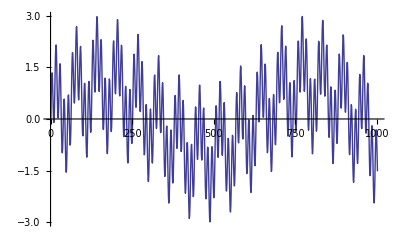

C:\Users\RHester-lab\Desktop\input.txt

```mathematica
input=Table[Sin[x]+Sin[x*10]+Sin[x*50],{x,0,10,0.01}];

ListPlot[input,Joined->True]
inputText=StringJoin[ToString[Length[input]],"\n",Riffle[ToString/@input,"\n"],(*dt*)"0.01",(*RC*)"0.3"]

inputFile=FileNameJoin[{targetDir,"input.txt"}];

Export[inputFile,inputText,"Text"]
```

```mathematica
ClearAll[ClassifyF]
<<CCompilerDriver`
<<SymbolicC`
<<CCodeGenerator`
```

```mathematica
ClassifyF=Compile[{{x1,_Real},{y1,_Real},{z1,_Real},{w1,_Real},{x2,_Real},{y2,_Real},{z2,_Real},{w2,_Real},{x3,_Real},{y3,_Real},{z3,_Real},{w3,_Real}},
Module[{Alphalist,SVlist,transdata},
Alphalist={-0.43085742229590096 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.3016447801277724 ,1.027395050120915 ,5.7067477760480445 ,1.5601288087202914 ,3.4097433513976725 ,0.5710887492916709 ,-0.5379046633072178 ,4.325606151426289 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.15421100605108648 ,4.571564062680221 ,-0.35761062840810687 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,6.800911132417174 ,-0.5379046633072178 ,2.283867190438977 ,-0.5379046633072178 ,5.245350224697719 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.10090100837200401 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,4.86214313530823 ,0.7338211857571351 ,16.839112502973204 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,14.112220891408302 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.5453178457826566 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.6198896893523238 ,5.346780942163542 ,4.944725751609696 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,4.161987834338847 ,-0.5379046633072178 ,-0.5379046633072178 ,0.6555802362420583 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,5.70828737270651 ,-0.5379046633072178 ,1.646356694272347 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.1527002977153402 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.9683952346914455 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,0.008561673940757035 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,4.305263956955241 ,0.6111866485978797 ,-0.5379046633072178 ,-0.5379046633072178 ,2.0643893873883385 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,12.558643334421307 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,0.42654476963840054 ,1.271502331204058 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.466630328075566 ,4.837088994041194 ,3.984610356065579 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.756472657027905 ,-0.5379046633072178 ,-0.15968159735996432 ,-0.5379046633072178 ,-0.05168229545567247 ,5.053954529118751 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.03906148545232593 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.671194622948311 ,-0.41658885250748684 ,-0.33581690449075563 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,2.4157523936247034 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.334007022670936 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,2.3155196364341406 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.101485653413442 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,2.1821589766428944 ,-0.5379046633072178 ,3.2038008510656297 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.0719715110042096 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.401793508564496 ,-0.030695786471042198 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.9617848730804934 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.2092969288417311 ,0.41605989209285066 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.32240475603916097 ,1.0769304809250455 ,1.6145735414130697 ,-0.5379046633072178 ,-0.04703824239709883 ,1.1167521236283915 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.4453846703380776 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.8919145404144007 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.14573857174325322 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5148412108591994 ,-0.3951030295466005 ,-0.18341910873753547 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.4200386553426636 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.1040954193813834 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,0.1865769177902623 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,0.7577476538755268 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.4124155290196273 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.2557975535034186 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,0.3750552802296926 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.2452609270069488 ,-0.5379046633072178 ,-0.10372187956859354 ,-0.04150517293159994 ,-0.33359713829891857 ,0.5464737918491299 ,-0.46569589164899755 ,-0.3183130820650332 ,-0.032071267587842116 ,-0.43216724909099685 ,-0.2979907699771092 ,-0.38590896180840595 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.42383122331324813 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.4555540240556437 ,-0.5379046633072178 ,-0.48431584366607305 ,-0.5379046633072178 ,-0.5023184823322752 ,-0.5379046633072178 ,-0.19867697111994456 ,-0.2773196482883349 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.11216877546143753 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.1522236774029435 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.41023405929777335 ,-0.5379046633072178 ,-0.03959870182512156 ,-0.22026418488220328 ,-0.3307678685711174 ,0.6512368243607087 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.23524658081222752 ,-0.3107734437065557 ,-0.5379046633072178 ,-0.2912891865583973 ,-0.5379046633072178 ,-0.2950281094401684 ,-0.0012821849065098867 ,-0.33571592276640444 ,-0.5379046633072178 ,0.6020390619444087 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.2843205912129128 ,-0.14942757903963058 ,-0.07611594432133384 ,-0.07566081367671433 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.34889654131019954 ,-0.31232602377287455 ,-0.22307647712560974 ,-0.3862071455580424 ,-0.06129309453582458 ,-0.22534947884093193 ,-0.5379046633072178 ,-0.16822009192133253 ,-0.5379046633072178 ,0.3622875016829147 ,-0.5379046633072178 ,-0.20061759004908392 ,-0.22835654974679984 ,-0.10081328682426494 ,-0.2789650741928603 ,-0.2767046731852717 ,-0.13231359154316147 ,-0.08027664214843716 ,-0.13610249122407306 ,-0.03400097158524288 ,-0.02333497849232087 ,-0.014598932608741233 ,-0.32289835758301827 ,-0.14296273753956587 ,-0.5048314338611173 ,-0.12503358934457526 ,-0.2411481807197275 };SVlist={{-0.36985099 ,-0.47094601 ,1.38186 ,1.3779401 ,-0.369133 ,-0.48860899 ,1.4661 ,1.44064 ,-0.38629001 ,-0.48287901 ,1.38705 ,1.40561 },{-0.177873 ,-0.394896 ,-0.47803801 ,-0.45220101 ,-0.25360599 ,-0.428004 ,-0.31457201 ,-0.28339201 ,-0.31650299 ,-0.44888401 ,-0.180271 ,-0.144438 },{2.8285899 ,2.68101 ,0.52291399 ,0.046072599 ,2.7675099 ,2.6682401 ,0.402695 ,-0.060671799 ,2.50811 ,2.4311399 ,0.097142898 ,-0.318028 },{-0.029093999 ,-0.35137701 ,-0.45861399 ,-0.40858299 ,-0.237912 ,-0.39833501 ,-0.45827001 ,-0.38496599 ,-0.30481401 ,-0.43470901 ,-0.310285 ,-0.242888 },{-0.55093902 ,-0.62343401 ,-1.92828 ,-1.88924 ,-0.66632998 ,-0.46401501 ,-1.8496 ,-1.7611099 ,-0.218769 ,-0.15476801 ,-0.56365001 ,-0.586178 },{-0.48603401 ,-0.34638801 ,-0.306642 ,-0.136455 ,-0.51413703 ,-0.38415599 ,0.042328801 ,0.247702 ,-0.54857498 ,-0.41379899 ,0.137383 ,0.37991199 },{-0.045498598 ,2.33251 ,-1.84644 ,-1.82302 ,-0.10785 ,2.02127 ,-1.8625799 ,-1.82938 ,-0.101597 ,0.43019199 ,-1.76975 ,-1.74149 },{-0.49438199 ,-0.47863701 ,-1.8417 ,-1.83038 ,-0.65317702 ,-0.133394 ,-1.80264 ,-1.72848 ,-0.23458 ,0.069907099 ,-0.44569701 ,-0.48564899 },{0.057422802 ,2.6027701 ,-1.63868 ,-1.66171 ,-0.0083404602 ,2.52545 ,-1.7916501 ,-1.77175 ,-0.081730299 ,1.92984 ,-1.78442 ,-1.7543499 },{-0.56117898 ,-0.59062999 ,-1.89653 ,-1.88256 ,-0.691392 ,-0.22092199 ,-1.85225 ,-1.78257 ,-0.35581401 ,-0.121371 ,-0.44856101 ,-0.51175702 },{2.7471099 ,2.58881 ,0.62853801 ,0.14115 ,2.83727 ,2.5825701 ,0.70750999 ,0.205385 ,2.93823 ,2.6643 ,0.69321603 ,0.192151 },{-0.55453002 ,-0.592623 ,-1.90089 ,-1.8696001 ,-0.69300997 ,-0.250532 ,-1.84958 ,-1.7625 ,-0.19205301 ,-0.0173099 ,-0.36778399 ,-0.42423299 },{-0.57738602 ,-0.624502 ,-1.9117399 ,-1.88808 ,-0.69974798 ,-0.389507 ,-1.83982 ,-1.7730401 ,-0.37062001 ,-0.136952 ,-0.43164301 ,-0.48230201 },{2.83727 ,2.5825701 ,0.70750999 ,0.205385 ,2.93823 ,2.6643 ,0.69321603 ,0.192151 ,2.9319401 ,2.6795299 ,0.59565699 ,0.10782 },{2.68627 ,2.55615 ,0.59492803 ,0.116207 ,2.78421 ,2.6715801 ,0.59870499 ,0.115857 ,2.83464 ,2.6900499 ,0.56009799 ,0.0792467 },{2.6994801 ,2.5634799 ,0.53814203 ,0.058436099 ,2.77755 ,2.61536 ,0.58149201 ,0.095268503 ,2.84776 ,2.7244799 ,0.57868701 ,0.096764401 },{2.17606 ,2.7997501 ,-0.83479702 ,-1.0946 ,-0.329317 ,-0.51785302 ,-1.91034 ,-1.88064 ,-0.60935599 ,-0.58062798 ,-1.94935 ,-1.86812 },{-0.55698198 ,-0.65123701 ,-1.92147 ,-1.87446 ,-0.70342201 ,-0.221581 ,-1.86523 ,-1.74959 ,-0.0039973701 ,-0.0184165 ,-0.108729 ,-0.205182 },{-0.45185801 ,0.61726302 ,-1.50764 ,-1.47261 ,-0.391655 ,-0.85407102 ,-1.15501 ,-1.1321599 ,2.1786399 ,2.52828 ,-0.060439199 ,-0.44830799 },{-0.61597002 ,-0.58215302 ,-1.93102 ,-1.87801 ,-0.75984597 ,-0.45197999 ,-1.86879 ,-1.75538 ,-0.043200999 ,-0.12942401 ,-0.345938 ,-0.40936601 },{-0.60935599 ,-0.58062798 ,-1.94935 ,-1.86812 ,-0.76930201 ,-0.401124 ,-1.90273 ,-1.76169 ,0.0121859 ,-0.120015 ,-0.53606701 ,-0.558321 },{-0.48992801 ,-0.53456402 ,-1.85604 ,-1.8329 ,-0.64348 ,-0.147938 ,-1.81754 ,-1.73448 ,-0.066743597 ,0.093681201 ,-0.238594 ,-0.311784 },{2.73823 ,2.6858101 ,0.5431 ,0.073890999 ,2.6673501 ,2.6368401 ,0.479137 ,0.020786401 ,2.68047 ,2.6264 ,0.49896199 ,0.0348715 },{-0.43985599 ,-0.36795199 ,-0.24956299 ,-0.098561801 ,-0.51246202 ,-0.387337 ,0.0104473 ,0.199754 ,-0.55708802 ,-0.43437201 ,0.19737799 ,0.42138699 },{-0.30294099 ,2.1609199 ,-1.49273 ,-1.53207 ,-0.27901199 ,1.0545 ,-1.42844 ,-1.4642 ,2.4244101 ,2.81229 ,-0.171983 ,-0.58504403 },{-0.069212899 ,2.4273 ,-1.74176 ,-1.7388999 ,-0.15291899 ,2.0741401 ,-1.77197 ,-1.7553 ,-0.16803201 ,0.57258499 ,-1.6824 ,-1.6709599 },{2.237 ,2.4198999 ,-0.32637399 ,-0.661322 ,1.2147599 ,1.5848 ,-1.00115 ,-1.1701601 ,-0.205908 ,0.038980301 ,-1.72165 ,-1.68753 },{0.0204395 ,2.3046701 ,-1.65773 ,-1.67388 ,-0.075582199 ,2.01719 ,-1.69653 ,-1.69666 ,-0.113265 ,0.63132203 ,-1.63789 ,-1.63495 },{-0.0083404602 ,2.52545 ,-1.7916501 ,-1.77175 ,-0.081730299 ,1.92984 ,-1.78442 ,-1.7543499 ,-0.050763201 ,0.14000399 ,-1.6423301 ,-1.62286 },{-0.226796 ,2.4669299 ,-1.66996 ,-1.64863 ,-0.230856 ,2.23013 ,-1.66851 ,-1.64934 ,-0.235108 ,2.0269799 ,-1.6638499 ,-1.6489201 },{1.7954299 ,1.93253 ,-0.54205 ,-0.82942599 ,0.25045401 ,0.44954899 ,-1.47501 ,-1.54229 ,-0.218813 ,-0.19314501 ,-1.6318901 ,-1.66422 },{-0.45433301 ,-0.35253599 ,-0.255889 ,-0.0944447 ,-0.52865797 ,-0.36388701 ,-0.107479 ,0.096469 ,-0.579849 ,-0.40415901 ,0.026384801 ,0.28035101 },{-0.15291899 ,2.0741401 ,-1.77197 ,-1.7553 ,-0.16803201 ,0.57258499 ,-1.6824 ,-1.6709599 ,1.6465501 ,2.16909 ,-1.06523 ,-1.2784801 },{2.2765901 ,2.30494 ,-0.16926201 ,-0.54150498 ,1.20191 ,1.48857 ,-0.997706 ,-1.17874 ,-0.193909 ,-0.034193899 ,-1.6511101 ,-1.63486 },{-0.47681299 ,-0.393226 ,-0.29125899 ,-0.117766 ,-0.47738901 ,-0.40435201 ,-0.034136999 ,0.13978299 ,-0.47990099 ,-0.41411701 ,0.0873385 ,0.290425 },{-0.461178 ,-0.32709301 ,-0.213617 ,-0.051886 ,-0.527982 ,-0.37231901 ,0.0131514 ,0.18657599 ,-0.56089503 ,-0.41217801 ,0.118575 ,0.34421501 },{-0.64174998 ,-0.42485499 ,-0.229037 ,0.037169602 ,-0.67896199 ,-0.43097201 ,-0.123056 ,0.175745 ,-0.71099901 ,-0.467742 ,-0.039832301 ,0.28405899 },{-0.64819801 ,-0.422346 ,-0.205533 ,0.054673899 ,-0.685027 ,-0.44229099 ,-0.111565 ,0.17514899 ,-0.71504802 ,-0.47668299 ,-0.030030901 ,0.29276001 },{-0.27397799 ,2.1131001 ,-1.62032 ,-1.6083 ,-0.266049 ,1.83109 ,-1.6420701 ,-1.62799 ,-0.271054 ,1.66913 ,-1.64862 ,-1.62779 },{-0.38162199 ,2.97119 ,-1.47177 ,-1.49371 ,-0.39051601 ,1.7999001 ,-1.57617 ,-1.5678101 ,-0.44754499 ,1.74252 ,-1.58883 ,-1.5558 },{-0.460715 ,-0.36855 ,-0.227332 ,-0.033380099 ,-0.530186 ,-0.39568999 ,-0.085761599 ,0.16253901 ,-0.59602797 ,-0.41197801 ,-0.0146496 ,0.26738301 },{-0.215011 ,2.1488099 ,-1.6680599 ,-1.64537 ,-0.217658 ,1.9351799 ,-1.68662 ,-1.66256 ,-0.227778 ,1.78416 ,-1.6907901 ,-1.66553 },{2.0148399 ,2.1691401 ,-0.35512501 ,-0.67272902 ,1.07245 ,1.3701299 ,-1.03626 ,-1.20781 ,-0.228002 ,0.0436919 ,-1.69059 ,-1.66395 },{2.2402201 ,2.3133399 ,-0.282731 ,-0.62810099 ,1.0343 ,1.26948 ,-1.0822099 ,-1.2395101 ,-0.281526 ,-0.13518301 ,-1.72653 ,-1.69677 },{2.1786399 ,2.52828 ,-0.060439199 ,-0.44830799 ,1.08571 ,1.5562299 ,-0.88032103 ,-1.07649 ,-0.318023 ,0.0762458 ,-1.61736 ,-1.60434 },{2.1815801 ,2.3522201 ,-0.30102301 ,-0.622024 ,1.42857 ,1.81375 ,-0.88925803 ,-1.09053 ,0.096813202 ,0.468463 ,-1.58759 ,-1.61891 },{-0.19932599 ,-0.35404 ,-0.380211 ,-0.314459 ,-0.39764401 ,-0.40700001 ,-0.274167 ,-0.177507 ,-0.48568401 ,-0.40620801 ,-0.13505299 ,0.026514901 },{-0.42692301 ,-0.405139 ,-0.41048801 ,-0.224141 ,-0.438247 ,-0.433898 ,-0.154075 ,0.0156123 ,-0.46546599 ,-0.42804101 ,-0.052073199 ,0.131062 },{-0.342922 ,-0.354581 ,-0.49551201 ,-0.40340701 ,-0.44109499 ,-0.36853001 ,-0.215343 ,-0.107095 ,-0.51639301 ,-0.37791201 ,-0.048984401 ,0.113382 },{-0.39764401 ,-0.40700001 ,-0.274167 ,-0.177507 ,-0.48568401 ,-0.40620801 ,-0.13505299 ,0.026514901 ,-0.555475 ,-0.392387 ,-0.00925982 ,0.197135 },{2.0264299 ,2.184 ,-0.351576 ,-0.68924397 ,0.61105198 ,0.79348201 ,-1.22425 ,-1.35356 ,-0.23898 ,-0.192543 ,-1.63196 ,-1.65258 },{-0.41498101 ,-0.29164001 ,-0.69196397 ,-0.480784 ,-0.449496 ,-0.40057799 ,-0.13112 ,0.071545899 ,-0.534181 ,-0.420827 ,-0.052162498 ,0.170489 },{-0.36166799 ,-0.325804 ,-0.578475 ,-0.42420799 ,-0.45433301 ,-0.35253599 ,-0.255889 ,-0.0944447 ,-0.52865797 ,-0.36388701 ,-0.107479 ,0.096469 },{-0.42260599 ,-0.37893 ,-0.47896799 ,-0.30290499 ,-0.47681299 ,-0.393226 ,-0.29125899 ,-0.117766 ,-0.47738901 ,-0.40435201 ,-0.034136999 ,0.13978299 },{1.8505501 ,2.2056799 ,-0.56082797 ,-0.83482999 ,0.63618201 ,0.95371199 ,-1.31619 ,-1.40729 ,-0.40667999 ,-0.30059701 ,-1.80239 ,-1.7618901 },{2.4203601 ,2.52352 ,0.0350057 ,-0.34858701 ,2.0148399 ,2.1691401 ,-0.35512501 ,-0.67272902 ,1.07245 ,1.3701299 ,-1.03626 ,-1.20781 },{1.14293 ,1.4872299 ,-1.0055 ,-1.19311 ,-0.23242199 ,-0.0187495 ,-1.6814899 ,-1.67468 ,-0.47695699 ,-0.29042301 ,-1.7695301 ,-1.7115901 },{-0.230856 ,2.23013 ,-1.66851 ,-1.64934 ,-0.235108 ,2.0269799 ,-1.6638499 ,-1.6489201 ,-0.249768 ,1.9430701 ,-1.66285 ,-1.6445301 },{1.88535 ,1.9822201 ,-0.45642999 ,-0.769804 ,0.60422403 ,0.74663401 ,-1.27729 ,-1.39176 ,-0.266231 ,-0.20969599 ,-1.67129 ,-1.67082 },{1.20191 ,1.48857 ,-0.997706 ,-1.17874 ,-0.193909 ,-0.034193899 ,-1.6511101 ,-1.63486 ,-0.44122401 ,-0.32428199 ,-1.73183 ,-1.6806901 },{2.0327401 ,2.2309401 ,-0.39886999 ,-0.72122902 ,0.71581697 ,1.04319 ,-1.2124799 ,-1.33518 ,-0.38325399 ,-0.27631301 ,-1.7532901 ,-1.72973 },{-0.39274499 ,-0.383578 ,-0.698865 ,-0.48252699 ,-0.42692301 ,-0.405139 ,-0.41048801 ,-0.224141 ,-0.438247 ,-0.433898 ,-0.154075 ,0.0156123 },{2.7315099 ,2.6323199 ,0.34645501 ,-0.113759 ,2.3008599 ,2.3132901 ,-0.091397204 ,-0.46981001 ,1.29282 ,1.46737 ,-0.86670202 ,-1.07897 },{-0.33874801 ,-0.34710601 ,-0.65330201 ,-0.46906999 ,-0.42260599 ,-0.37893 ,-0.47896799 ,-0.30290499 ,-0.47681299 ,-0.393226 ,-0.29125899 ,-0.117766 },{-0.22920799 ,1.77343 ,-1.5327801 ,-1.54125 ,-0.226796 ,2.4669299 ,-1.66996 ,-1.64863 ,-0.230856 ,2.23013 ,-1.66851 ,-1.64934 },{2.5269799 ,2.5046101 ,0.0085712103 ,-0.36640999 ,2.02191 ,2.16575 ,-0.420398 ,-0.71796399 ,0.947568 ,1.22241 ,-1.14038 ,-1.27665 },{-0.51639301 ,-0.37791201 ,-0.048984401 ,0.113382 ,-0.56310999 ,-0.40846899 ,0.107371 ,0.31235299 ,-0.59959 ,-0.42795101 ,0.181894 ,0.43457699 },{-0.30913901 ,1.90414 ,-1.6325099 ,-1.64193 ,-0.272302 ,0.670304 ,-1.5641 ,-1.57965 ,2.1380501 ,2.72721 ,-0.52232802 ,-0.85924399 },{-0.52393502 ,-0.454301 ,-1.80164 ,-1.7535501 ,-0.599666 ,-0.37612399 ,-1.74081 ,-1.65711 ,-0.29273 ,-0.081024401 ,-0.95623499 ,-0.94178802 },{-0.53039801 ,-0.43676901 ,-1.8092 ,-1.72837 ,-0.59672201 ,-0.47041699 ,-1.75416 ,-1.64485 ,-0.28703901 ,-0.186574 ,-0.93329197 ,-0.926772 },{-0.697577 ,-0.463673 ,-1.89389 ,-1.78495 ,-0.899472 ,-0.55027699 ,-1.90965 ,-1.70061 ,-0.140008 ,-0.30808899 ,-0.96523601 ,-0.90031397 },{-0.35853499 ,-0.38879699 ,-0.449527 ,-0.298924 ,-0.39839599 ,-0.415999 ,-0.229893 ,-0.091124304 ,-0.44555399 ,-0.41389301 ,-0.121824 ,0.0228751 },{-0.50111902 ,-0.67934799 ,-1.88108 ,-1.88151 ,-0.65262699 ,-0.387795 ,-1.86069 ,-1.80838 ,-0.47456801 ,0.14961 ,-0.85486102 ,-0.794568 },{-0.31248701 ,-0.38983101 ,-0.331063 ,-0.223719 ,-0.37138501 ,-0.41486201 ,-0.16463099 ,-0.053566702 ,-0.415544 ,-0.42418501 ,-0.046705801 ,0.074121296 },{-0.31362399 ,-0.428597 ,-0.32932499 ,-0.20869599 ,-0.377877 ,-0.455634 ,-0.212194 ,-0.082707599 ,-0.41604999 ,-0.456103 ,-0.116327 ,0.0303072 },{-0.394651 ,-0.39768001 ,-0.257173 ,-0.181097 ,-0.48228601 ,-0.38217801 ,-0.0554129 ,0.070101202 ,-0.541421 ,-0.38639599 ,0.133496 ,0.32137501 },{-0.390598 ,-0.59631097 ,-1.90371 ,-1.8784 ,-0.56021702 ,-0.49265301 ,-1.88173 ,-1.81292 ,-0.18957099 ,0.40740299 ,-0.92425603 ,-0.86726701 },{-0.59643799 ,-0.78276199 ,-1.98956 ,-1.93171 ,-0.76606601 ,-0.65218598 ,-1.94655 ,-1.83176 ,-0.173307 ,-0.095834501 ,-0.56457001 ,-0.57927603 },{-0.60509998 ,-0.69724798 ,-1.8616 ,-1.78995 ,-0.655168 ,-0.514817 ,-1.76569 ,-1.63758 ,-0.27448899 ,-0.238603 ,-0.94574302 ,-0.93617201 },{-0.56905299 ,-0.71612298 ,-1.94894 ,-1.91871 ,-0.68669701 ,-0.43660399 ,-1.89757 ,-1.81323 ,-0.35347 ,-0.150465 ,-0.64839703 ,-0.66091198 },{-0.40763 ,-0.70490003 ,-1.97332 ,-1.90819 ,-0.58071297 ,-0.74846298 ,-1.94643 ,-1.83617 ,-0.33059701 ,0.150481 ,-1.22298 ,-1.1399601 },{-1.07848 ,-0.71208799 ,-1.9371901 ,-1.7253 ,-0.97277999 ,-0.409704 ,-1.7665401 ,-1.58188 ,-0.00040752001 ,-0.26091999 ,-0.87029701 ,-0.82740599 },{-0.316912 ,1.67272 ,-1.44135 ,-1.4876 ,-0.26623201 ,0.31506899 ,-1.35312 ,-1.41237 ,1.63605 ,2.6740699 ,-0.667669 ,-0.94714898 },{-0.27388299 ,-0.34599799 ,-0.59898698 ,-0.456094 ,-0.35853499 ,-0.38879699 ,-0.449527 ,-0.298924 ,-0.39839599 ,-0.415999 ,-0.229893 ,-0.091124304 },{-0.227593 ,-0.39926901 ,-0.443203 ,-0.33223999 ,-0.31362399 ,-0.428597 ,-0.32932499 ,-0.20869599 ,-0.377877 ,-0.455634 ,-0.212194 ,-0.082707599 },{-0.18782701 ,-0.28569001 ,-0.84867603 ,-0.753968 ,-0.342922 ,-0.354581 ,-0.49551201 ,-0.40340701 ,-0.44109499 ,-0.36853001 ,-0.215343 ,-0.107095 },{-0.174539 ,-0.33394599 ,-0.70709002 ,-0.60405999 ,-0.249733 ,-0.364382 ,-0.54157197 ,-0.429979 ,-0.31248701 ,-0.38983101 ,-0.331063 ,-0.223719 },{-0.89346498 ,-0.98246402 ,-2.0870099 ,-1.88922 ,-1.1202199 ,-0.67637902 ,-2.0695801 ,-1.82213 ,-0.18782701 ,-0.28569001 ,-0.84867603 ,-0.753968 },{-0.52865797 ,-0.36388701 ,-0.107479 ,0.096469 ,-0.579849 ,-0.40415901 ,0.026384801 ,0.28035101 ,-0.602516 ,-0.433851 ,0.13807601 ,0.43681601 },{-0.28800899 ,2.1128099 ,-1.67734 ,-1.6521 ,-0.28866601 ,1.88073 ,-1.69707 ,-1.67037 ,-0.30568799 ,1.76563 ,-1.70219 ,-1.67032 },{-0.59213102 ,-0.643098 ,-1.94319 ,-1.85054 ,-0.70872599 ,-0.345698 ,-1.87154 ,-1.71683 ,0.21072499 ,0.155039 ,-0.41384199 ,-0.40710199 },{-0.596609 ,-0.74045902 ,-1.9688801 ,-1.92242 ,-0.73485601 ,-0.455897 ,-1.91758 ,-1.82127 ,-0.109012 ,-0.12784301 ,-0.26670101 ,-0.34254301 },{-0.59106898 ,-0.79260498 ,-1.99778 ,-1.89132 ,-0.73608702 ,-0.27653801 ,-1.90889 ,-1.72447 ,0.15775301 ,-0.031272698 ,-0.318771 ,-0.33191699 },{-0.117663 ,0.24482401 ,-0.77033198 ,-0.79293102 ,0.112241 ,0.000234835 ,-0.29035801 ,-0.316874 ,-0.190391 ,-0.18465599 ,0.0123837 ,0.0333279 },{-0.48361099 ,-0.27114201 ,-1.34988 ,-1.1418999 ,-0.42763999 ,-0.26891899 ,-0.72074699 ,-0.51858401 ,-0.44977099 ,-0.351504 ,-0.12202 ,0.057933901 },{-0.33357999 ,-0.31948099 ,-0.73286998 ,-0.56585401 ,-0.43985599 ,-0.36795199 ,-0.24956299 ,-0.098561801 ,-0.51246202 ,-0.387337 ,0.0104473 ,0.199754 },{-0.31650299 ,-0.44888401 ,-0.180271 ,-0.144438 ,-0.37883699 ,-0.46757299 ,-0.076062903 ,-0.028822601 ,-0.430089 ,-0.467219 ,0.0037596601 ,0.076342203 },{-0.64312202 ,-0.58669001 ,-1.97359 ,-1.84273 ,-0.80583501 ,-0.29121399 ,-1.89554 ,-1.67731 ,0.073818497 ,-0.14703199 ,-0.341409 ,-0.34113199 },{1.07245 ,1.3701299 ,-1.03626 ,-1.20781 ,-0.228002 ,0.0436919 ,-1.69059 ,-1.66395 ,-0.48329699 ,-0.229718 ,-1.77554 ,-1.70315 },{-1.02628 ,-1.08786 ,-2.0803499 ,-1.8026 ,-1.11033 ,-0.74712998 ,-2.0322499 ,-1.74186 ,-0.260851 ,-0.333318 ,-1.1055599 ,-0.98385602 },{-0.33059701 ,0.150481 ,-1.22298 ,-1.1399601 ,0.098122299 ,0.141008 ,-0.33658499 ,-0.28236499 ,-0.18668599 ,-0.210713 ,0.21953601 ,0.26765901 },{-0.42534199 ,-0.696652 ,-1.90222 ,-1.90774 ,-0.57738602 ,-0.624502 ,-1.9117399 ,-1.88808 ,-0.69974798 ,-0.389507 ,-1.83982 ,-1.7730401 },{-0.35040101 ,0.205406 ,-1.0217299 ,-0.99478698 ,0.20005199 ,-0.052912399 ,-0.20008101 ,-0.27470201 ,-0.084156401 ,-0.21088199 ,0.034771699 ,0.0165623 },{-0.45638499 ,2.7051301 ,-1.37955 ,-1.40801 ,-0.46164101 ,1.54837 ,-1.4547 ,-1.46539 ,-0.47658101 ,1.0601 ,-1.40227 ,-1.4008501 },{-0.381201 ,-0.27270699 ,-1.27098 ,-1.09038 ,-0.416787 ,-0.28633401 ,-0.74531901 ,-0.582461 ,-0.461178 ,-0.32709301 ,-0.213617 ,-0.051886 },{-0.552248 ,0.24568801 ,-1.61044 ,-1.5586801 ,-0.35040101 ,0.205406 ,-1.0217299 ,-0.99478698 ,0.20005199 ,-0.052912399 ,-0.20008101 ,-0.27470201 },{-0.60966599 ,-0.95726001 ,-2.0214 ,-1.95996 ,-0.74360299 ,-0.498043 ,-1.91611 ,-1.76781 ,0.15325999 ,-0.125135 ,-0.175677 ,-0.25490201 },{-0.56943798 ,-1.10096 ,-2.1450701 ,-2.00529 ,-1.03405 ,-1.12246 ,-2.1210201 ,-1.87085 ,-0.381201 ,-0.27270699 ,-1.27098 ,-1.09038 },{-1.09594 ,-1.09278 ,-2.11043 ,-1.79855 ,-1.09394 ,-0.66014397 ,-2.03917 ,-1.72756 ,-0.234246 ,-0.31863901 ,-1.183 ,-0.985093 },{0.947568 ,1.22241 ,-1.14038 ,-1.27665 ,-0.267371 ,-0.121279 ,-1.7586401 ,-1.73623 ,-0.43252099 ,-0.43623 ,-1.79849 ,-1.75033 },{-0.61097503 ,-0.85856402 ,-1.9920599 ,-1.94777 ,-0.72547501 ,-0.53105801 ,-1.90846 ,-1.80532 ,0.0149297 ,-0.11501 ,-0.17123599 ,-0.262481 },{-0.37233999 ,-0.72350901 ,-1.9612 ,-1.91631 ,-0.58605599 ,-0.67756999 ,-1.9614 ,-1.86496 ,-0.71985298 ,-0.32992399 ,-1.88525 ,-1.72531 },{-0.46123999 ,-0.63708198 ,-1.94048 ,-1.92442 ,-0.61597002 ,-0.58215302 ,-1.93102 ,-1.87801 ,-0.75984597 ,-0.45197999 ,-1.86879 ,-1.75538 },{-0.50999999 ,-0.33664101 ,-1.50528 ,-1.2549599 ,-0.41498101 ,-0.29164001 ,-0.69196397 ,-0.480784 ,-0.449496 ,-0.40057799 ,-0.13112 ,0.071545899 },{-0.557491 ,-0.0069551002 ,-1.3772 ,-1.3679301 ,-0.038481601 ,0.153539 ,-0.611696 ,-0.701231 ,0.27509999 ,0.0090545099 ,-0.14297 ,-0.31389999 },{1.1170599 ,1.34176 ,-1.03256 ,-1.21088 ,-0.206838 ,-0.103047 ,-1.69091 ,-1.69266 ,-0.41129401 ,-0.30436301 ,-1.74326 ,-1.71732 },{-0.54032701 ,-0.0466047 ,-1.38912 ,-1.3648 ,-0.20812 ,0.069494702 ,-0.811463 ,-0.85915202 ,0.330863 ,0.0118978 ,-0.086961903 ,-0.25956401 },{-0.273458 ,-0.37778899 ,-0.612625 ,-0.53161001 ,-0.394651 ,-0.39768001 ,-0.257173 ,-0.181097 ,-0.48228601 ,-0.38217801 ,-0.0554129 ,0.070101202 },{-0.22171301 ,-0.35278499 ,-0.43092501 ,-0.318324 ,-0.30489799 ,-0.387326 ,-0.284159 ,-0.16023 ,-0.36552599 ,-0.40630499 ,-0.11039 ,0.0010059 },{-0.44883201 ,2.6096799 ,-1.30976 ,-1.34489 ,-0.487544 ,1.52837 ,-1.35675 ,-1.36387 ,-0.491034 ,0.364553 ,-1.2338001 ,-1.24149 },{-0.038481601 ,0.153539 ,-0.611696 ,-0.701231 ,0.27509999 ,0.0090545099 ,-0.14297 ,-0.31389999 ,0.446426 ,-0.095721699 ,0.130188 ,-0.0651014 },{0.27850699 ,0.0531643 ,-0.40499401 ,-0.38160199 ,-0.052423399 ,-0.18294001 ,-0.0142248 ,0.0356111 ,-0.22328199 ,-0.33468899 ,0.50130099 ,0.51566201 },{-0.483401 ,-0.83171499 ,-2.01493 ,-1.99853 ,-0.61097503 ,-0.85856402 ,-1.9920599 ,-1.94777 ,-0.72547501 ,-0.53105801 ,-1.90846 ,-1.80532 },{-0.65653098 ,-0.208425 ,-1.84056 ,-1.72875 ,0.25268 ,-0.0014511599 ,0.16 ,0.0181814 ,0.072825298 ,-0.200028 ,0.80827701 ,0.61238098 },{0.222284 ,0.41230199 ,-1.45443 ,-1.53986 ,-0.248273 ,-0.27756801 ,-1.59865 ,-1.65596 ,-0.29929999 ,-0.22552601 ,-1.60335 ,-1.64922 },{0.25045401 ,0.44954899 ,-1.47501 ,-1.54229 ,-0.218813 ,-0.19314501 ,-1.6318901 ,-1.66422 ,-0.287332 ,-0.317148 ,-1.65742 ,-1.67574 },{0.278301 ,0.45989001 ,-1.4094501 ,-1.4821399 ,-0.168859 ,-0.18622901 ,-1.62625 ,-1.65168 ,-0.29394901 ,-0.328949 ,-1.68174 ,-1.67992 },{-0.292382 ,1.8774199 ,-1.6437 ,-1.62747 ,-0.293432 ,1.70039 ,-1.64961 ,-1.63378 ,-0.302829 ,1.58016 ,-1.64647 ,-1.62854 },{-0.261466 ,1.97118 ,-1.68595 ,-1.67021 ,-0.28136799 ,1.91458 ,-1.68397 ,-1.66247 ,-0.32726899 ,1.30214 ,-1.6086 ,-1.5585099 },{-0.266049 ,1.83109 ,-1.6420701 ,-1.62799 ,-0.271054 ,1.66913 ,-1.64862 ,-1.62779 ,-0.310761 ,1.3150899 ,-1.5914299 ,-1.55238 },{-0.28866601 ,1.88073 ,-1.69707 ,-1.67037 ,-0.30568799 ,1.76563 ,-1.70219 ,-1.67032 ,-0.34096101 ,1.5853 ,-1.69496 ,-1.65188 },{0.58343601 ,-0.19973999 ,0.41368499 ,0.183549 ,0.38066599 ,-0.217299 ,0.58206302 ,0.35658699 ,0.200611 ,-0.255595 ,0.727678 ,0.50977802 },{1.0343 ,1.26948 ,-1.0822099 ,-1.2395101 ,-0.281526 ,-0.13518301 ,-1.72653 ,-1.69677 ,-0.45365101 ,-0.33498001 ,-1.7570601 ,-1.7046601 },{-0.415025 ,-0.71856898 ,-1.98667 ,-1.96371 ,-0.59643799 ,-0.78276199 ,-1.98956 ,-1.93171 ,-0.76606601 ,-0.65218598 ,-1.94655 ,-1.83176 },{-0.329317 ,-0.51785302 ,-1.91034 ,-1.88064 ,-0.60935599 ,-0.58062798 ,-1.94935 ,-1.86812 ,-0.76930201 ,-0.401124 ,-1.90273 ,-1.76169 },{-0.45114401 ,-0.36812001 ,-1.84728 ,-1.80352 ,-0.54554898 ,-0.56312698 ,-1.87058 ,-1.80952 ,-0.60509998 ,-0.69724798 ,-1.8616 ,-1.78995 },{-0.305307 ,1.88313 ,-1.5114 ,-1.56151 ,-0.30913901 ,1.90414 ,-1.6325099 ,-1.64193 ,-0.272302 ,0.670304 ,-1.5641 ,-1.57965 },{-0.302829 ,1.58016 ,-1.64647 ,-1.62854 ,-0.32880199 ,1.05744 ,-1.57275 ,-1.53975 ,-0.29021299 ,-0.162082 ,-1.40701 ,-1.37928 },{-0.27901199 ,1.0545 ,-1.42844 ,-1.4642 ,2.4244101 ,2.81229 ,-0.171983 ,-0.58504403 ,-0.144006 ,0.193735 ,-1.60719 ,-1.64597 },{-0.235108 ,2.0269799 ,-1.6638499 ,-1.6489201 ,-0.249768 ,1.9430701 ,-1.66285 ,-1.6445301 ,-0.288138 ,1.26907 ,-1.56783 ,-1.53677 },{-0.227778 ,1.78416 ,-1.6907901 ,-1.66553 ,-0.25332299 ,1.71808 ,-1.68938 ,-1.65481 ,-0.28068501 ,0.538661 ,-1.60519 ,-1.55756 },{-0.255768 ,2.17133 ,-1.68695 ,-1.6704299 ,-0.261466 ,1.97118 ,-1.68595 ,-1.67021 ,-0.28136799 ,1.91458 ,-1.68397 ,-1.66247 },{-0.30568799 ,1.76563 ,-1.70219 ,-1.67032 ,-0.34096101 ,1.5853 ,-1.69496 ,-1.65188 ,-0.35520101 ,0.370644 ,-1.5739599 ,-1.5237401 },{-0.39051601 ,1.7999001 ,-1.57617 ,-1.5678101 ,-0.44754499 ,1.74252 ,-1.58883 ,-1.5558 ,-0.45185801 ,0.61726302 ,-1.50764 ,-1.47261 },{-0.28136799 ,1.91458 ,-1.68397 ,-1.66247 ,-0.32726899 ,1.30214 ,-1.6086 ,-1.5585099 ,-0.29861599 ,0.216557 ,-1.4396 ,-1.3978601 },{-0.426092 ,-0.66667801 ,-1.91127 ,-1.91181 ,-0.57902598 ,-0.62337101 ,-1.91623 ,-1.89103 ,-0.70945501 ,-0.26904601 ,-1.8497 ,-1.76817 },{-0.35921201 ,-0.73114598 ,-1.98753 ,-1.93555 ,-0.59106898 ,-0.79260498 ,-1.99778 ,-1.89132 ,-0.73608702 ,-0.27653801 ,-1.90889 ,-1.72447 },{-0.401389 ,-0.67085499 ,-1.91403 ,-1.91008 ,-0.55135602 ,-0.58671403 ,-1.90797 ,-1.875 ,-0.68329197 ,-0.294249 ,-1.8539799 ,-1.75875 },{-0.302802 ,1.92207 ,-1.9032201 ,-1.8601 ,-0.31812301 ,1.30375 ,-1.88774 ,-1.84433 ,-0.23278201 ,-0.54916298 ,-1.59009 ,-1.64127 },{1.08571 ,1.5562299 ,-0.88032103 ,-1.07649 ,-0.318023 ,0.0762458 ,-1.61736 ,-1.60434 ,-0.51517397 ,-0.21170001 ,-1.66732 ,-1.6246099 },{1.2147599 ,1.5848 ,-1.00115 ,-1.1701601 ,-0.205908 ,0.038980301 ,-1.72165 ,-1.68753 ,-0.49786499 ,-0.40402499 ,-1.81119 ,-1.74436 },{1.29282 ,1.46737 ,-0.86670202 ,-1.07897 ,-0.14063001 ,0.042593502 ,-1.64247 ,-1.63065 ,-0.43763599 ,-0.246023 ,-1.7162499 ,-1.67068 },{-0.416787 ,-0.28633401 ,-0.74531901 ,-0.582461 ,-0.461178 ,-0.32709301 ,-0.213617 ,-0.051886 ,-0.527982 ,-0.37231901 ,0.0131514 ,0.18657599 },{-0.249733 ,-0.364382 ,-0.54157197 ,-0.429979 ,-0.31248701 ,-0.38983101 ,-0.331063 ,-0.223719 ,-0.37138501 ,-0.41486201 ,-0.16463099 ,-0.053566702 },{-0.54046297 ,-0.374199 ,-1.72049 ,-1.63889 ,-0.59934998 ,-0.44697401 ,-1.67969 ,-1.57284 ,0.087430298 ,-0.15827601 ,-0.57584602 ,-0.63434398 },{-0.219465 ,-0.27156401 ,-0.99928099 ,-0.83456701 ,-0.36166799 ,-0.325804 ,-0.578475 ,-0.42420799 ,-0.45433301 ,-0.35253599 ,-0.255889 ,-0.0944447 },{-0.28258899 ,-0.29877701 ,-1.25328 ,-1.08382 ,-0.33357999 ,-0.31948099 ,-0.73286998 ,-0.56585401 ,-0.43985599 ,-0.36795199 ,-0.24956299 ,-0.098561801 },{-0.42763999 ,-0.26891899 ,-0.72074699 ,-0.51858401 ,-0.44977099 ,-0.351504 ,-0.12202 ,0.057933901 ,-0.50565797 ,-0.39833501 ,-0.00245355 ,0.214081 },{-0.54554898 ,-0.56312698 ,-1.87058 ,-1.80952 ,-0.60509998 ,-0.69724798 ,-1.8616 ,-1.78995 ,-0.655168 ,-0.514817 ,-1.76569 ,-1.63758 },{0.89439499 ,1.18435 ,-1.09489 ,-1.25629 ,-0.19742399 ,0.00237087 ,-1.65213 ,-1.67256 ,-0.31438801 ,-0.33366799 ,-1.70279 ,-1.70495 },{-0.217658 ,1.9351799 ,-1.68662 ,-1.66256 ,-0.227778 ,1.78416 ,-1.6907901 ,-1.66553 ,-0.25332299 ,1.71808 ,-1.68938 ,-1.65481 },{0.037941098 ,2.2666299 ,-1.70268 ,-1.69552 ,-0.022184899 ,1.83841 ,-1.71022 ,-1.69393 ,-0.0075340802 ,-0.058193799 ,-1.5604 ,-1.5483299 },{-0.53280801 ,-0.68751699 ,-1.92743 ,-1.87822 ,-0.65653098 ,-0.208425 ,-1.84056 ,-1.72875 ,0.25268 ,-0.0014511599 ,0.16 ,0.0181814 },{-0.76930201 ,-0.401124 ,-1.90273 ,-1.76169 ,0.0121859 ,-0.120015 ,-0.53606701 ,-0.558321 ,-0.14772201 ,-0.192082 ,0.066454001 ,0.044500101 },{-0.58605599 ,-0.67756999 ,-1.9614 ,-1.86496 ,-0.71985298 ,-0.32992399 ,-1.88525 ,-1.72531 ,0.18474001 ,0.0021174001 ,-0.26304901 ,-0.29161799 },{-0.58328003 ,-0.73671299 ,-2.0755401 ,-1.9257801 ,-0.65653503 ,-0.86034799 ,-2.04563 ,-1.87462 ,-0.80658901 ,-0.94208598 ,-2.04054 ,-1.81955 },{-0.44109499 ,-0.36853001 ,-0.215343 ,-0.107095 ,-0.51639301 ,-0.37791201 ,-0.048984401 ,0.113382 ,-0.56310999 ,-0.40846899 ,0.107371 ,0.31235299 },{-0.39839599 ,-0.415999 ,-0.229893 ,-0.091124304 ,-0.44555399 ,-0.41389301 ,-0.121824 ,0.0228751 ,-0.458738 ,-0.42136201 ,0.00497565 ,0.179819 },{-0.30489799 ,-0.387326 ,-0.284159 ,-0.16023 ,-0.36552599 ,-0.40630499 ,-0.11039 ,0.0010059 ,-0.41433701 ,-0.42915601 ,-0.026577299 ,0.108331 },{-0.583152 ,-0.642546 ,-1.94929 ,-1.83689 ,-0.68905401 ,-0.42405599 ,-1.87185 ,-1.70621 ,0.27850699 ,0.0531643 ,-0.40499401 ,-0.38160199 },{-0.55135602 ,-0.58671403 ,-1.90797 ,-1.875 ,-0.68329197 ,-0.294249 ,-1.8539799 ,-1.75875 ,0.0049949498 ,-0.0618365 ,-0.14106899 ,-0.239099 },{0.055121999 ,0.35144401 ,-1.5454 ,-1.58768 ,-0.35277599 ,-0.324718 ,-1.71365 ,-1.7185 ,-0.44203201 ,-0.446419 ,-1.7484601 ,-1.74006 },{-0.57902598 ,-0.62337101 ,-1.91623 ,-1.89103 ,-0.70945501 ,-0.26904601 ,-1.8497 ,-1.76817 ,-0.15712 ,-0.121978 ,-0.116578 ,-0.22608 },{-0.53092498 ,-0.45814601 ,-2.0729301 ,-1.89045 ,-0.67381001 ,-0.73983502 ,-2.06949 ,-1.84721 ,-0.76274401 ,-0.90220201 ,-2.0404 ,-1.7874 },{-0.57990497 ,-0.43437701 ,-1.78736 ,-1.6867501 ,-0.62503898 ,-0.45861301 ,-1.74411 ,-1.62117 ,0.212975 ,-0.182842 ,-0.54355502 ,-0.61381 },{-0.58572298 ,-0.41341099 ,-1.75337 ,-1.67119 ,-0.63789701 ,-0.37706599 ,-1.69613 ,-1.58208 ,0.057782602 ,-0.176612 ,-0.55039299 ,-0.61827499 },{-0.40384001 ,-0.63535601 ,-1.90292 ,-1.9015599 ,-0.55453002 ,-0.592623 ,-1.90089 ,-1.8696001 ,-0.69300997 ,-0.250532 ,-1.84958 ,-1.7625 },{-0.425446 ,-0.64754802 ,-1.89623 ,-1.9062001 ,-0.56117898 ,-0.59062999 ,-1.89653 ,-1.88256 ,-0.691392 ,-0.22092199 ,-1.85225 ,-1.78257 },{-0.36031201 ,-0.73400301 ,-1.93297 ,-1.91631 ,-0.53280801 ,-0.68751699 ,-1.92743 ,-1.87822 ,-0.65653098 ,-0.208425 ,-1.84056 ,-1.72875 },{-0.445429 ,-0.71449202 ,-1.97004 ,-1.92989 ,-0.59063601 ,-0.59089398 ,-1.93952 ,-1.85461 ,-0.71430999 ,-0.162992 ,-1.82214 ,-1.66357 },{-0.67381001 ,-0.73983502 ,-2.06949 ,-1.84721 ,-0.76274401 ,-0.90220201 ,-2.0404 ,-1.7874 ,-0.93987501 ,-0.98800403 ,-2.0643699 ,-1.7615401 },{-0.58563 ,-0.46136701 ,-1.78663 ,-1.69265 ,-0.63578802 ,-0.390008 ,-1.72241 ,-1.58988 ,0.195995 ,-0.191974 ,-0.427818 ,-0.51540899 },{0.60422403 ,0.74663401 ,-1.27729 ,-1.39176 ,-0.266231 ,-0.20969599 ,-1.67129 ,-1.67082 ,-0.40661201 ,-0.28951001 ,-1.72384 ,-1.69979 },{-0.59063601 ,-0.59089398 ,-1.93952 ,-1.85461 ,-0.71430999 ,-0.162992 ,-1.82214 ,-1.66357 ,0.25319001 ,-0.114575 ,0.094636299 ,-0.0202851 },{-0.554748 ,-0.29188299 ,-1.80804 ,-1.76104 ,-0.73724699 ,0.129265 ,-1.77458 ,-1.64775 ,0.062535301 ,0.124801 ,-0.18222301 ,-0.23253199 },{-0.53177798 ,-0.36663601 ,-1.69864 ,-1.66535 ,-0.60286498 ,-0.226964 ,-1.59297 ,-1.5270801 ,-0.174945 ,-0.087338999 ,-0.38539401 ,-0.476466 },{-1.01248 ,-0.538086 ,-1.9813499 ,-1.7856801 ,-1.07848 ,-0.71208799 ,-1.9371901 ,-1.7253 ,-0.97277999 ,-0.409704 ,-1.7665401 ,-1.58188 },{-0.97558701 ,-0.58211601 ,-1.95951 ,-1.74638 ,-1.0404201 ,-0.65415102 ,-1.90021 ,-1.6745501 ,-1.03642 ,-0.37711301 ,-1.76103 ,-1.54303 },{-0.476441 ,-0.016365699 ,-1.40806 ,-1.39194 ,-0.59250301 ,0.35330299 ,-1.39413 ,-1.32656 ,0.056211501 ,0.042607199 ,-0.501086 ,-0.59375602 },{-0.43252099 ,-0.43623 ,-1.79849 ,-1.75033 ,-0.53039801 ,-0.43676901 ,-1.8092 ,-1.72837 ,-0.59672201 ,-0.47041699 ,-1.75416 ,-1.64485 },{-0.409134 ,-0.442884 ,-1.77859 ,-1.7527601 ,-0.52393502 ,-0.454301 ,-1.80164 ,-1.7535501 ,-0.599666 ,-0.37612399 ,-1.74081 ,-1.65711 },{-0.49786499 ,-0.40402499 ,-1.81119 ,-1.74436 ,-0.57990497 ,-0.43437701 ,-1.78736 ,-1.6867501 ,-0.62503898 ,-0.45861301 ,-1.74411 ,-1.62117 },{-0.50416303 ,0.0230914 ,-1.35966 ,-1.35095 ,-0.46694499 ,0.035902899 ,-1.0112799 ,-1.00991 ,0.27870101 ,-0.0858294 ,-0.21884701 ,-0.37742099 },{0.61105198 ,0.79348201 ,-1.22425 ,-1.35356 ,-0.23898 ,-0.192543 ,-1.63196 ,-1.65258 ,-0.358069 ,-0.25948101 ,-1.66855 ,-1.65931 },{-0.51644897 ,-0.040374901 ,-1.3321 ,-1.33241 ,-0.33598799 ,0.070206799 ,-0.86713201 ,-0.90319598 ,0.119314 ,-0.00275097 ,-0.29413 ,-0.41566399 },{-0.57010102 ,0.029876299 ,-1.4235899 ,-1.40127 ,-0.31446901 ,-0.052091099 ,-0.903736 ,-0.93401003 ,0.28553301 ,-0.124227 ,-0.201812 ,-0.37457699 },{-0.66495502 ,-0.15887401 ,-1.90596 ,-1.7347701 ,-0.97558701 ,-0.58211601 ,-1.95951 ,-1.74638 ,-1.0404201 ,-0.65415102 ,-1.90021 ,-1.6745501 },{0.531793 ,-0.169937 ,0.157317 ,-0.075913101 ,0.720451 ,-0.265163 ,0.33871701 ,0.071177997 ,0.64801198 ,-0.300704 ,0.260232 ,0.039958101 },{-0.83453798 ,-0.90331101 ,-2.04392 ,-1.77104 ,-1.09594 ,-1.09278 ,-2.11043 ,-1.79855 ,-1.09394 ,-0.66014397 ,-2.03917 ,-1.72756 },{-0.240475 ,-0.53166699 ,-1.82933 ,-1.84714 ,-0.48992801 ,-0.53456402 ,-1.85604 ,-1.8329 ,-0.64348 ,-0.147938 ,-1.81754 ,-1.73448 },{-0.93987501 ,-0.98800403 ,-2.0643699 ,-1.7615401 ,-1.14197 ,-1.06453 ,-2.1018 ,-1.77364 ,-0.62905198 ,-0.42179501 ,-1.57851 ,-1.34089 },{-0.67896199 ,-0.43097201 ,-0.123056 ,0.175745 ,-0.71099901 ,-0.467742 ,-0.039832301 ,0.28405899 ,-0.72749698 ,-0.490807 ,0.0452727 ,0.40292901 },{-0.340352 ,0.25058001 ,-1.52196 ,-1.50454 ,-0.50708801 ,-0.092026301 ,-1.53114 ,-1.48708 ,-0.553204 ,-0.149464 ,-1.5105 ,-1.43101 },{-0.56923401 ,0.134518 ,-1.16772 ,-1.1816601 ,-0.082200497 ,-0.015649199 ,-0.47821999 ,-0.61785698 ,0.2225 ,-0.148334 ,-0.0936848 ,-0.30739501 },{-0.168613 ,0.53954899 ,-1.2151 ,-1.25959 ,-0.54032701 ,-0.0466047 ,-1.38912 ,-1.3648 ,-0.20812 ,0.069494702 ,-0.811463 ,-0.85915202 },{0.50032502 ,1.3320301 ,-1.1469899 ,-1.27236 ,-0.552248 ,0.24568801 ,-1.61044 ,-1.5586801 ,-0.35040101 ,0.205406 ,-1.0217299 ,-0.99478698 },{2.64798 ,2.5556099 ,0.203594 ,-0.23642799 ,2.09145 ,2.1859901 ,-0.35010201 ,-0.68408501 ,0.89439499 ,1.18435 ,-1.09489 ,-1.25629 },{2.5934999 ,2.5499301 ,0.063844502 ,-0.33935499 ,2.0334301 ,2.1533401 ,-0.403328 ,-0.715608 ,0.881661 ,1.16229 ,-1.1536601 ,-1.29799 },{2.6612301 ,2.60672 ,0.235304 ,-0.190323 ,2.2765901 ,2.30494 ,-0.16926201 ,-0.54150498 ,1.20191 ,1.48857 ,-0.997706 ,-1.17874 },{2.51139 ,2.61713 ,0.0056698401 ,-0.368559 ,2.1815801 ,2.3522201 ,-0.30102301 ,-0.622024 ,1.42857 ,1.81375 ,-0.88925803 ,-1.09053 },{-0.144006 ,0.193735 ,-1.60719 ,-1.64597 ,-0.53603101 ,-0.065915003 ,-1.72637 ,-1.69879 ,-0.71122003 ,0.147808 ,-1.71667 ,-1.6133 },{-0.260851 ,-0.333318 ,-1.1055599 ,-0.98385602 ,-0.234937 ,-0.33256 ,-0.76404703 ,-0.65580201 ,-0.28547299 ,-0.36379999 ,-0.48844901 ,-0.39825499 },{0.0636613 ,0.79024899 ,-1.00458 ,-1.12104 ,-0.51644897 ,-0.040374901 ,-1.3321 ,-1.33241 ,-0.33598799 ,0.070206799 ,-0.86713201 ,-0.90319598 },{-0.36977601 ,-0.42090499 ,-0.101911 ,-0.0272756 ,-0.411484 ,-0.42969 ,-0.094998002 ,0.0278462 ,-0.48141301 ,-0.43358201 ,-0.050834101 ,0.081939697 },{-0.449496 ,-0.40057799 ,-0.13112 ,0.071545899 ,-0.534181 ,-0.420827 ,-0.052162498 ,0.170489 ,-0.604684 ,-0.42689601 ,-0.0534808 ,0.211099 },{0.97185498 ,1.07645 ,-1.10259 ,-1.26372 ,-0.187682 ,-0.121648 ,-1.66705 ,-1.67339 ,-0.347262 ,-0.35438201 ,-1.72083 ,-1.70523 },{0.881661 ,1.16229 ,-1.1536601 ,-1.29799 ,-0.168154 ,-0.029639199 ,-1.6914999 ,-1.7045799 ,-0.28432399 ,-0.322182 ,-1.73373 ,-1.72936 },{1.23627 ,1.51458 ,-1.26176 ,-1.41549 ,-0.402475 ,-0.63964701 ,-1.9075201 ,-1.86601 ,-0.57605302 ,-0.57340902 ,-1.89174 ,-1.8127199 },{0.99979001 ,1.52704 ,-0.62121099 ,-0.86761498 ,-0.39247799 ,-0.0033599799 ,-1.51035 ,-1.51533 ,-0.52005702 ,-0.174762 ,-1.52926 ,-1.5043 },{-0.488152 ,-0.048914399 ,-1.3638 ,-1.35144 ,-0.558707 ,-0.046757799 ,-1.19779 ,-1.17436 ,0.27026001 ,0.0042587901 ,-0.168109 ,-0.319846 },{-0.50708801 ,-0.092026301 ,-1.53114 ,-1.48708 ,-0.553204 ,-0.149464 ,-1.5105 ,-1.43101 ,0.170178 ,-0.16896901 ,-0.62042701 ,-0.71680802 },{-0.28163099 ,0.281656 ,-1.5661 ,-1.56422 ,-0.28800899 ,2.1128099 ,-1.67734 ,-1.6521 ,-0.28866601 ,1.88073 ,-1.69707 ,-1.67037 },{-0.29961699 ,1.6534801 ,-1.37745 ,-1.42224 ,-0.22183301 ,-0.37417501 ,-1.19363 ,-1.2646 ,0.50032502 ,1.3320301 ,-1.1469899 ,-1.27236 },{-0.022184899 ,1.83841 ,-1.71022 ,-1.69393 ,-0.0075340802 ,-0.058193799 ,-1.5604 ,-1.5483299 ,1.23627 ,1.51458 ,-1.26176 ,-1.41549 },{-0.081730299 ,1.92984 ,-1.78442 ,-1.7543499 ,-0.050763201 ,0.14000399 ,-1.6423301 ,-1.62286 ,1.38528 ,1.7555701 ,-1.22858 ,-1.40248 },{0.54685301 ,1.23452 ,-0.82395899 ,-0.99843401 ,-0.454779 ,-0.126523 ,-1.3668 ,-1.36264 ,-0.53365302 ,-0.103371 ,-1.34118 ,-1.30591 },{-0.48568401 ,-0.40620801 ,-0.13505299 ,0.026514901 ,-0.555475 ,-0.392387 ,-0.00925982 ,0.197135 ,-0.59036702 ,-0.43817899 ,0.17399199 ,0.438889 },{-0.44977099 ,-0.351504 ,-0.12202 ,0.057933901 ,-0.50565797 ,-0.39833501 ,-0.00245355 ,0.214081 ,-0.568551 ,-0.41115099 ,0.0486564 ,0.28699899 },{2.02191 ,2.16575 ,-0.420398 ,-0.71796399 ,0.947568 ,1.22241 ,-1.14038 ,-1.27665 ,-0.267371 ,-0.121279 ,-1.7586401 ,-1.73623 },{-0.067678802 ,2.39886 ,-1.75605 ,-1.74633 ,-0.139705 ,1.64821 ,-1.75275 ,-1.73931 ,2.7118101 ,2.96313 ,-0.45691699 ,-0.81745303 },{-0.491034 ,0.364553 ,-1.2338001 ,-1.24149 ,2.2792799 ,2.5727501 ,0.65552402 ,0.142839 ,1.54822 ,2.1022699 ,-0.114099 ,-0.47800499 },{2.6661899 ,2.5510001 ,0.57019299 ,0.096926004 ,2.68627 ,2.55615 ,0.59492803 ,0.116207 ,2.78421 ,2.6715801 ,0.59870499 ,0.115857 },{2.6772499 ,2.56127 ,0.55166799 ,0.0736738 ,2.7413199 ,2.59987 ,0.575625 ,0.092210002 ,2.8127699 ,2.6637299 ,0.59552097 ,0.110458 },{2.6673501 ,2.6368401 ,0.479137 ,0.020786401 ,2.68047 ,2.6264 ,0.49896199 ,0.0348715 ,2.74576 ,2.6529901 ,0.532058 ,0.062124599 },{2.68047 ,2.6264 ,0.49896199 ,0.0348715 ,2.74576 ,2.6529901 ,0.532058 ,0.062124599 ,2.77316 ,2.68748 ,0.50479901 ,0.043357801 },{2.7413199 ,2.59987 ,0.575625 ,0.092210002 ,2.8127699 ,2.6637299 ,0.59552097 ,0.110458 ,2.8285899 ,2.68101 ,0.52291399 ,0.046072599 },{2.77755 ,2.61536 ,0.58149201 ,0.095268503 ,2.84776 ,2.7244799 ,0.57868701 ,0.096764401 ,2.84635 ,2.7106299 ,0.54503602 ,0.058325302 },{-0.28547299 ,-0.36379999 ,-0.48844901 ,-0.39825499 ,-0.31753999 ,-0.39627701 ,-0.236729 ,-0.16867 ,-0.36977601 ,-0.42090499 ,-0.101911 ,-0.0272756 },{-0.237912 ,-0.39833501 ,-0.45827001 ,-0.38496599 ,-0.30481401 ,-0.43470901 ,-0.310285 ,-0.242888 ,-0.36091 ,-0.452407 ,-0.205162 ,-0.115842 },{2.0334301 ,2.1533401 ,-0.403328 ,-0.715608 ,0.881661 ,1.16229 ,-1.1536601 ,-1.29799 ,-0.168154 ,-0.029639199 ,-1.6914999 ,-1.7045799 },{2.09145 ,2.1859901 ,-0.35010201 ,-0.68408501 ,0.89439499 ,1.18435 ,-1.09489 ,-1.25629 ,-0.19742399 ,0.00237087 ,-1.65213 ,-1.67256 },{2.1247399 ,2.1552401 ,-0.262344 ,-0.60716099 ,0.97185498 ,1.07645 ,-1.10259 ,-1.26372 ,-0.187682 ,-0.121648 ,-1.66705 ,-1.67339 },{2.74576 ,2.6529901 ,0.532058 ,0.062124599 ,2.77316 ,2.68748 ,0.50479901 ,0.043357801 ,2.7526 ,2.6724701 ,0.427248 ,-0.0232228 },{2.6904399 ,2.5281999 ,0.489494 ,0.046366401 ,2.77742 ,2.5962999 ,0.49691501 ,0.0498951 ,2.8318501 ,2.68466 ,0.45539999 ,0.0133607 },{2.77316 ,2.68748 ,0.50479901 ,0.043357801 ,2.7526 ,2.6724701 ,0.427248 ,-0.0232228 ,2.6612301 ,2.60672 ,0.235304 ,-0.190323 },{2.53053 ,2.5892401 ,0.28508401 ,-0.123406 ,2.59112 ,2.6229801 ,0.306256 ,-0.105434 ,2.64167 ,2.6802101 ,0.28306299 ,-0.124422 },{2.6728699 ,2.58371 ,0.44872701 ,-0.0015814099 ,2.7848599 ,2.6463101 ,0.50715101 ,0.0457961 ,2.84462 ,2.6979599 ,0.46033099 ,0.0021752799 },{-0.25246701 ,-0.41274899 ,-0.39368501 ,-0.291913 ,-0.32653201 ,-0.44070199 ,-0.23593 ,-0.13239799 ,-0.388533 ,-0.47236401 ,-0.103611 ,0.0083012599 },{2.3008599 ,2.3132901 ,-0.091397204 ,-0.46981001 ,1.29282 ,1.46737 ,-0.86670202 ,-1.07897 ,-0.14063001 ,0.042593502 ,-1.64247 ,-1.63065 },{2.4725399 ,2.59673 ,-0.087210998 ,-0.48811901 ,1.51702 ,1.8325 ,-0.77180803 ,-1.00708 ,0.055121999 ,0.35144401 ,-1.5454 ,-1.58768 },{2.4479101 ,2.47139 ,0.021948799 ,-0.389732 ,1.41986 ,1.6603301 ,-0.75072098 ,-0.99114799 ,-0.137033 ,0.18850601 ,-1.59043 ,-1.59605 },{2.6149499 ,2.9791501 ,-0.476477 ,-0.83446699 ,0.32605499 ,0.54926503 ,-1.60681 ,-1.6888601 ,-0.425446 ,-0.64754802 ,-1.89623 ,-1.9062001 },{2.5785201 ,2.68257 ,0.28330901 ,-0.13229699 ,2.53053 ,2.5892401 ,0.28508401 ,-0.123406 ,2.59112 ,2.6229801 ,0.306256 ,-0.105434 },{-0.36091 ,-0.452407 ,-0.205162 ,-0.115842 ,-0.39345801 ,-0.450066 ,-0.12973 ,-0.020785701 ,-0.44760001 ,-0.46188101 ,-0.094852701 ,0.051766001 },{2.59112 ,2.6229801 ,0.306256 ,-0.105434 ,2.64167 ,2.6802101 ,0.28306299 ,-0.124422 ,2.6180899 ,2.73599 ,0.20759401 ,-0.19416399 },{2.84776 ,2.7244799 ,0.57868701 ,0.096764401 ,2.84635 ,2.7106299 ,0.54503602 ,0.058325302 ,2.8287301 ,2.68608 ,0.44713101 ,-0.0177394 },{2.78421 ,2.6715801 ,0.59870499 ,0.115857 ,2.83464 ,2.6900499 ,0.56009799 ,0.0792467 ,2.8178101 ,2.67665 ,0.46235701 ,-0.00754409 },{-0.71099901 ,-0.467742 ,-0.039832301 ,0.28405899 ,-0.72749698 ,-0.490807 ,0.0452727 ,0.40292901 ,-0.732274 ,-0.531515 ,0.068043701 ,0.446006 },{-0.377877 ,-0.455634 ,-0.212194 ,-0.082707599 ,-0.41604999 ,-0.456103 ,-0.116327 ,0.0303072 ,-0.464477 ,-0.44834501 ,-0.067286998 ,0.10717 },{-0.30481401 ,-0.43470901 ,-0.310285 ,-0.242888 ,-0.36091 ,-0.452407 ,-0.205162 ,-0.115842 ,-0.39345801 ,-0.450066 ,-0.12973 ,-0.020785701 },{-0.59250301 ,0.35330299 ,-1.39413 ,-1.32656 ,0.056211501 ,0.042607199 ,-0.501086 ,-0.59375602 ,0.41241699 ,-0.077164702 ,0.0727247 ,-0.098531701 },{1.42857 ,1.81375 ,-0.88925803 ,-1.09053 ,0.096813202 ,0.468463 ,-1.58759 ,-1.61891 ,-0.45114401 ,-0.36812001 ,-1.84728 ,-1.80352 },{1.65942 ,1.75237 ,-0.60687399 ,-0.87715501 ,0.278301 ,0.45989001 ,-1.4094501 ,-1.4821399 ,-0.168859 ,-0.18622901 ,-1.62625 ,-1.65168 },{1.41986 ,1.6603301 ,-0.75072098 ,-0.99114799 ,-0.137033 ,0.18850601 ,-1.59043 ,-1.59605 ,-0.46967 ,-0.281434 ,-1.70735 ,-1.66255 },{2.8127699 ,2.6637299 ,0.59552097 ,0.110458 ,2.8285899 ,2.68101 ,0.52291399 ,0.046072599 ,2.7675099 ,2.6682401 ,0.402695 ,-0.060671799 },{-0.438247 ,-0.433898 ,-0.154075 ,0.0156123 ,-0.46546599 ,-0.42804101 ,-0.052073199 ,0.131062 ,-0.49107999 ,-0.423581 ,0.020844599 ,0.242035 },{-0.32653201 ,-0.44070199 ,-0.23593 ,-0.13239799 ,-0.388533 ,-0.47236401 ,-0.103611 ,0.0083012599 ,-0.43264699 ,-0.46790799 ,-0.0250961 ,0.104143 },{-0.31753999 ,-0.39627701 ,-0.236729 ,-0.16867 ,-0.36977601 ,-0.42090499 ,-0.101911 ,-0.0272756 ,-0.411484 ,-0.42969 ,-0.094998002 ,0.0278462 },{-0.553204 ,-0.149464 ,-1.5105 ,-1.43101 ,0.170178 ,-0.16896901 ,-0.62042701 ,-0.71680802 ,0.57332301 ,-0.226611 ,-0.15935101 ,-0.34018299 },{0.71581697 ,1.04319 ,-1.2124799 ,-1.33518 ,-0.38325399 ,-0.27631301 ,-1.7532901 ,-1.72973 ,-0.50163001 ,-0.40118 ,-1.77637 ,-1.72621 },{1.52858 ,2.0661299 ,-1.14114 ,-1.33925 ,-0.401389 ,-0.67085499 ,-1.91403 ,-1.91008 ,-0.55135602 ,-0.58671403 ,-1.90797 ,-1.875 },{1.28491 ,1.77145 ,-1.26887 ,-1.42483 ,-0.445429 ,-0.71449202 ,-1.97004 ,-1.92989 ,-0.59063601 ,-0.59089398 ,-1.93952 ,-1.85461 },{1.38528 ,1.7555701 ,-1.22858 ,-1.40248 ,-0.36031201 ,-0.73400301 ,-1.93297 ,-1.91631 ,-0.53280801 ,-0.68751699 ,-1.92743 ,-1.87822 },{-0.454779 ,-0.126523 ,-1.3668 ,-1.36264 ,-0.53365302 ,-0.103371 ,-1.34118 ,-1.30591 ,0.12574001 ,0.14194299 ,-0.467179 ,-0.55853403 },{-0.162582 ,-0.38118899 ,-0.52416301 ,-0.44249001 ,-0.25246701 ,-0.41274899 ,-0.39368501 ,-0.291913 ,-0.32653201 ,-0.44070199 ,-0.23593 ,-0.13239799 },{-0.685027 ,-0.44229099 ,-0.111565 ,0.17514899 ,-0.71504802 ,-0.47668299 ,-0.030030901 ,0.29276001 ,-0.73223603 ,-0.50203198 ,0.044413999 ,0.38780099 },{-0.122367 ,-0.31121001 ,-0.56275398 ,-0.468321 ,-0.22171301 ,-0.35278499 ,-0.43092501 ,-0.318324 ,-0.30489799 ,-0.387326 ,-0.284159 ,-0.16023 },{-0.234937 ,-0.33256 ,-0.76404703 ,-0.65580201 ,-0.28547299 ,-0.36379999 ,-0.48844901 ,-0.39825499 ,-0.31753999 ,-0.39627701 ,-0.236729 ,-0.16867 },{-0.530186 ,-0.39568999 ,-0.085761599 ,0.16253901 ,-0.59602797 ,-0.41197801 ,-0.0146496 ,0.26738301 ,-0.61129898 ,-0.443149 ,0.120621 ,0.44452599 },{-0.52005702 ,-0.174762 ,-1.52926 ,-1.5043 ,-0.613419 ,0.092412397 ,-1.52136 ,-1.45416 ,0.040071901 ,0.0107922 ,-0.470254 ,-0.550973 },{-0.44203201 ,-0.446419 ,-1.7484601 ,-1.74006 ,-0.54418403 ,-0.420021 ,-1.75946 ,-1.72473 ,-0.60905701 ,-0.46899301 ,-1.70927 ,-1.63889 },{-0.47695699 ,-0.29042301 ,-1.7695301 ,-1.7115901 ,-0.56605101 ,-0.43922299 ,-1.75893 ,-1.6712199 ,-0.62308401 ,-0.51028103 ,-1.73364 ,-1.63016 },{-0.48329699 ,-0.229718 ,-1.77554 ,-1.70315 ,-0.571688 ,-0.435132 ,-1.75937 ,-1.65764 ,-0.62917298 ,-0.50149602 ,-1.73943 ,-1.6164401 },{-0.37138501 ,-0.41486201 ,-0.16463099 ,-0.053566702 ,-0.415544 ,-0.42418501 ,-0.046705801 ,0.074121296 ,-0.46354699 ,-0.42425099 ,-0.036097199 ,0.12764101 },{0.112241 ,0.000234835 ,-0.29035801 ,-0.316874 ,-0.190391 ,-0.18465599 ,0.0123837 ,0.0333279 ,-0.355544 ,-0.34289199 ,0.46074799 ,0.464398 },{-0.39345801 ,-0.450066 ,-0.12973 ,-0.020785701 ,-0.44760001 ,-0.46188101 ,-0.094852701 ,0.051766001 ,-0.48719901 ,-0.44082701 ,-0.052123599 ,0.12842 },{-0.41604999 ,-0.456103 ,-0.116327 ,0.0303072 ,-0.464477 ,-0.44834501 ,-0.067286998 ,0.10717 ,-0.50787199 ,-0.43440199 ,-0.0147436 ,0.194315 },{-0.0258995 ,0.26545599 ,-1.90461 ,-1.83376 ,-0.58328003 ,-0.73671299 ,-2.0755401 ,-1.9257801 ,-0.65653503 ,-0.86034799 ,-2.04563 ,-1.87462 },{-0.75037497 ,-0.77051598 ,-2.0669899 ,-1.83366 ,-0.83453798 ,-0.90331101 ,-2.04392 ,-1.77104 ,-1.09594 ,-1.09278 ,-2.11043 ,-1.79855 },{-0.65653503 ,-0.86034799 ,-2.04563 ,-1.87462 ,-0.80658901 ,-0.94208598 ,-2.04054 ,-1.81955 ,-1.02628 ,-1.08786 ,-2.0803499 ,-1.8026 },{-0.39247799 ,-0.0033599799 ,-1.51035 ,-1.51533 ,-0.52005702 ,-0.174762 ,-1.52926 ,-1.5043 ,-0.613419 ,0.092412397 ,-1.52136 ,-1.45416 },{-0.437572 ,-0.00968224 ,-1.5263 ,-1.51572 ,-0.525585 ,-0.1558 ,-1.546 ,-1.51169 ,-0.61639899 ,-0.0073370798 ,-1.5255001 ,-1.44638 },{0.189868 ,0.168304 ,-1.72558 ,-1.76221 ,-0.429649 ,-0.63661098 ,-1.92709 ,-1.90438 ,-0.58057398 ,-0.499475 ,-1.90058 ,-1.83241 },{-0.25360599 ,-0.428004 ,-0.31457201 ,-0.28339201 ,-0.31650299 ,-0.44888401 ,-0.180271 ,-0.144438 ,-0.37883699 ,-0.46757299 ,-0.076062903 ,-0.028822601 },{-0.44555399 ,-0.41389301 ,-0.121824 ,0.0228751 ,-0.458738 ,-0.42136201 ,0.00497565 ,0.179819 ,-0.48731199 ,-0.41607201 ,0.0573311 ,0.26092499 },{-0.28340101 ,-0.43608999 ,-0.22220699 ,-0.140257 ,-0.34995499 ,-0.45453501 ,-0.13646901 ,-0.029963201 ,-0.39449599 ,-0.47226799 ,-0.061888002 ,0.053153198 },{-0.137033 ,0.18850601 ,-1.59043 ,-1.59605 ,-0.46967 ,-0.281434 ,-1.70735 ,-1.66255 ,-0.561149 ,-0.35425699 ,-1.70249 ,-1.6345299 },{-0.31812301 ,1.30375 ,-1.88774 ,-1.84433 ,-0.23278201 ,-0.54916298 ,-1.59009 ,-1.64127 ,0.319289 ,0.33783299 ,-1.65844 ,-1.68812 },{0.63618201 ,0.95371199 ,-1.31619 ,-1.40729 ,-0.40667999 ,-0.30059701 ,-1.80239 ,-1.7618901 ,-0.51746798 ,-0.36562601 ,-1.8128 ,-1.74312 },{-0.53603101 ,-0.065915003 ,-1.72637 ,-1.69879 ,-0.71122003 ,0.147808 ,-1.71667 ,-1.6133 ,-0.019429401 ,-0.0728034 ,-0.329961 ,-0.39650699 },{-0.13780899 ,0.47548899 ,-1.47956 ,-1.49418 ,-0.53100401 ,-0.174977 ,-1.63183 ,-1.58724 ,-0.59403801 ,-0.28427401 ,-1.6278 ,-1.55889 },{-0.534181 ,-0.420827 ,-0.052162498 ,0.170489 ,-0.604684 ,-0.42689601 ,-0.0534808 ,0.211099 ,-0.64628899 ,-0.44086599 ,0.0548064 ,0.349475 },{-0.193234 ,-0.378813 ,-0.37157199 ,-0.30989501 ,-0.267694 ,-0.42056 ,-0.225105 ,-0.160762 ,-0.321646 ,-0.43732801 ,-0.13767 ,-0.060113899 },{-0.44760001 ,-0.46188101 ,-0.094852701 ,0.051766001 ,-0.48719901 ,-0.44082701 ,-0.052123599 ,0.12842 ,-0.52971298 ,-0.427607 ,0.038198501 ,0.22990499 },{1.51702 ,1.8325 ,-0.77180803 ,-1.00708 ,0.055121999 ,0.35144401 ,-1.5454 ,-1.58768 ,-0.35277599 ,-0.324718 ,-1.71365 ,-1.7185 },{-1.0404201 ,-0.65415102 ,-1.90021 ,-1.6745501 ,-1.03642 ,-0.37711301 ,-1.76103 ,-1.54303 ,0.073750697 ,-0.276932 ,-0.70215499 ,-0.67131698 },{-0.429649 ,-0.63661098 ,-1.92709 ,-1.90438 ,-0.58057398 ,-0.499475 ,-1.90058 ,-1.83241 ,-0.56290299 ,0.111542 ,-1.3688999 ,-1.25494 },{-0.34096101 ,1.5853 ,-1.69496 ,-1.65188 ,-0.35520101 ,0.370644 ,-1.5739599 ,-1.5237401 ,2.70943 ,2.65312 ,0.32641599 ,-0.114866 },{-0.119025 ,2.33902 ,-1.8569 ,-1.8200001 ,-0.172023 ,1.98103 ,-1.8634599 ,-1.81856 ,-0.15869799 ,0.26809001 ,-1.74342 ,-1.70489 },{-0.293432 ,1.70039 ,-1.64961 ,-1.63378 ,-0.302829 ,1.58016 ,-1.64647 ,-1.62854 ,-0.32880199 ,1.05744 ,-1.57275 ,-1.53975 },{-0.57986897 ,0.045539901 ,-1.2108001 ,-1.19098 ,0.115686 ,0.115549 ,-0.34560701 ,-0.476349 ,0.44345501 ,0.036944401 ,0.111838 ,-0.076875597 },{-0.44754499 ,1.74252 ,-1.58883 ,-1.5558 ,-0.45185801 ,0.61726302 ,-1.50764 ,-1.47261 ,-0.391655 ,-0.85407102 ,-1.15501 ,-1.1321599 },{-0.53489703 ,-0.35825899 ,-1.73311 ,-1.67487 ,-0.60336602 ,-0.41812301 ,-1.69277 ,-1.60393 ,-0.21834099 ,-0.125229 ,-0.85875702 ,-0.868177 },{-0.49555099 ,-0.31160799 ,-1.70184 ,-1.66415 ,-0.57352298 ,-0.366005 ,-1.6698101 ,-1.6094 ,-0.31694299 ,-0.054770902 ,-0.89760798 ,-0.90527701 },{-0.56605101 ,-0.43922299 ,-1.75893 ,-1.6712199 ,-0.62308401 ,-0.51028103 ,-1.73364 ,-1.63016 ,-0.39979199 ,-0.219253 ,-1.0386 ,-1.02126 },{-0.39652601 ,1.04731 ,-1.42188 ,-1.4382499 ,-0.45638499 ,2.7051301 ,-1.37955 ,-1.40801 ,-0.46164101 ,1.54837 ,-1.4547 ,-1.46539 },{2.64167 ,2.6802101 ,0.28306299 ,-0.124422 ,2.6180899 ,2.73599 ,0.20759401 ,-0.19416399 ,2.51139 ,2.61713 ,0.0056698401 ,-0.368559 },{-0.140008 ,-0.30808899 ,-0.96523601 ,-0.90031397 ,-0.273458 ,-0.37778899 ,-0.612625 ,-0.53161001 ,-0.394651 ,-0.39768001 ,-0.257173 ,-0.181097 },{-0.262346 ,-0.31237599 ,-0.85929 ,-0.666354 ,-0.33874801 ,-0.34710601 ,-0.65330201 ,-0.46906999 ,-0.42260599 ,-0.37893 ,-0.47896799 ,-0.30290499 },{-0.525585 ,-0.1558 ,-1.546 ,-1.51169 ,-0.61639899 ,-0.0073370798 ,-1.5255001 ,-1.44638 ,0.045709401 ,-0.112259 ,-0.48855099 ,-0.57054198 },{-0.58071297 ,-0.74846298 ,-1.94643 ,-1.83617 ,-0.33059701 ,0.150481 ,-1.22298 ,-1.1399601 ,0.098122299 ,0.141008 ,-0.33658499 ,-0.28236499 },{-0.53031498 ,0.045323901 ,-1.68001 ,-1.65517 ,-0.66673201 ,-0.0151639 ,-1.67414 ,-1.6005501 ,-0.053218499 ,-0.0383774 ,-0.54246902 ,-0.58259797 },{-0.57352298 ,-0.366005 ,-1.6698101 ,-1.6094 ,-0.31694299 ,-0.054770902 ,-0.89760798 ,-0.90527701 ,0.169293 ,-0.142076 ,0.143787 ,-0.052310999 },{2.7848599 ,2.6463101 ,0.50715101 ,0.0457961 ,2.84462 ,2.6979599 ,0.46033099 ,0.0021752799 ,2.7999201 ,2.73441 ,0.35178 ,-0.0965477 },{2.93823 ,2.6643 ,0.69321603 ,0.192151 ,2.9319401 ,2.6795299 ,0.59565699 ,0.10782 ,2.83461 ,2.6612301 ,0.387793 ,-0.069457598 },{2.77742 ,2.5962999 ,0.49691501 ,0.0498951 ,2.8318501 ,2.68466 ,0.45539999 ,0.0133607 ,2.7420001 ,2.6524 ,0.28040001 ,-0.13631301 },{0.0121859 ,-0.120015 ,-0.53606701 ,-0.558321 ,-0.14772201 ,-0.192082 ,0.066454001 ,0.044500101 ,-0.28747299 ,-0.32997501 ,0.52234602 ,0.49339801 },{-0.22183301 ,-0.37417501 ,-1.19363 ,-1.2646 ,0.50032502 ,1.3320301 ,-1.1469899 ,-1.27236 ,-0.552248 ,0.24568801 ,-1.61044 ,-1.5586801 },{-0.244848 ,0.357651 ,-1.79752 ,-1.7505701 ,0.89945501 ,1.38353 ,-1.45021 ,-1.56411 ,-0.483401 ,-0.83171499 ,-2.01493 ,-1.99853 },{-0.80658901 ,-0.94208598 ,-2.04054 ,-1.81955 ,-1.02628 ,-1.08786 ,-2.0803499 ,-1.8026 ,-1.11033 ,-0.74712998 ,-2.0322499 ,-1.74186 },{-0.075582199 ,2.01719 ,-1.69653 ,-1.69666 ,-0.113265 ,0.63132203 ,-1.63789 ,-1.63495 ,2.23998 ,2.5367899 ,-0.67792302 ,-0.98617399 },{-0.60861897 ,-0.19549499 ,-1.56216 ,-1.5264699 ,-0.38040599 ,-0.113158 ,-0.73818702 ,-0.78317899 ,-0.0042288499 ,-0.176054 ,0.45245701 ,0.185368 },{-0.27427101 ,1.92119 ,-1.8687 ,-1.82706 ,-0.29098001 ,0.79364902 ,-1.82037 ,-1.78232 ,2.17606 ,2.7997501 ,-0.83479702 ,-1.0946 },{2.83464 ,2.6900499 ,0.56009799 ,0.0792467 ,2.8178101 ,2.67665 ,0.46235701 ,-0.00754409 ,2.64798 ,2.5556099 ,0.203594 ,-0.23642799 },{2.84635 ,2.7106299 ,0.54503602 ,0.058325302 ,2.8287301 ,2.68608 ,0.44713101 ,-0.0177394 ,2.6493399 ,2.52613 ,0.19321001 ,-0.23936801 },{-0.51746798 ,-0.36562601 ,-1.8128 ,-1.74312 ,-0.58563 ,-0.46136701 ,-1.78663 ,-1.69265 ,-0.63578802 ,-0.390008 ,-1.72241 ,-1.58988 },{0.096813202 ,0.468463 ,-1.58759 ,-1.61891 ,-0.45114401 ,-0.36812001 ,-1.84728 ,-1.80352 ,-0.54554898 ,-0.56312698 ,-1.87058 ,-1.80952 },{-0.318023 ,0.0762458 ,-1.61736 ,-1.60434 ,-0.51517397 ,-0.21170001 ,-1.66732 ,-1.6246099 ,-0.58913499 ,-0.29006901 ,-1.65264 ,-1.57671 },{-0.0104852 ,2.9921 ,-1.65503 ,-1.69045 ,-0.12633 ,2.4444699 ,-1.79457 ,-1.77987 ,-0.205778 ,1.7577 ,-1.7856899 ,-1.7598701 },{2.6493399 ,2.52613 ,0.19321001 ,-0.23936801 ,2.1247399 ,2.1552401 ,-0.262344 ,-0.60716099 ,0.97185498 ,1.07645 ,-1.10259 ,-1.26372 },{2.7409599 ,2.65521 ,0.18866301 ,-0.235162 ,2.2402201 ,2.3133399 ,-0.282731 ,-0.62810099 ,1.0343 ,1.26948 ,-1.0822099 ,-1.2395101 },{2.6110799 ,2.62412 ,0.12198 ,-0.297822 ,2.0327401 ,2.2309401 ,-0.39886999 ,-0.72122902 ,0.71581697 ,1.04319 ,-1.2124799 ,-1.33518 },{-0.14063001 ,0.042593502 ,-1.64247 ,-1.63065 ,-0.43763599 ,-0.246023 ,-1.7162499 ,-1.67068 ,-0.54273802 ,-0.384938 ,-1.7217 ,-1.65195 },{-0.205908 ,0.038980301 ,-1.72165 ,-1.68753 ,-0.49786499 ,-0.40402499 ,-1.81119 ,-1.74436 ,-0.57990497 ,-0.43437701 ,-1.78736 ,-1.6867501 },{-0.40667999 ,-0.30059701 ,-1.80239 ,-1.7618901 ,-0.51746798 ,-0.36562601 ,-1.8128 ,-1.74312 ,-0.58563 ,-0.46136701 ,-1.78663 ,-1.69265 },{-0.35520101 ,0.370644 ,-1.5739599 ,-1.5237401 ,2.70943 ,2.65312 ,0.32641599 ,-0.114866 ,2.6110799 ,2.62412 ,0.12198 ,-0.297822 },{2.6180899 ,2.73599 ,0.20759401 ,-0.19416399 ,2.51139 ,2.61713 ,0.0056698401 ,-0.368559 ,2.1815801 ,2.3522201 ,-0.30102301 ,-0.622024 },{-0.69974798 ,-0.389507 ,-1.83982 ,-1.7730401 ,-0.37062001 ,-0.136952 ,-0.43164301 ,-0.48230201 ,0.030017801 ,-0.18425199 ,0.97801298 ,0.70501298 },{-0.113265 ,0.63132203 ,-1.63789 ,-1.63495 ,2.23998 ,2.5367899 ,-0.67792302 ,-0.98617399 ,-0.240475 ,-0.53166699 ,-1.82933 ,-1.84714 },{-0.28068501 ,0.538661 ,-1.60519 ,-1.55756 ,-0.194242 ,-0.89711797 ,-0.967852 ,-0.978827 ,2.7409599 ,2.65521 ,0.18866301 ,-0.235162 },{-0.036316998 ,1.30152 ,-1.60066 ,-1.64 ,-0.069212899 ,2.4273 ,-1.74176 ,-1.7388999 ,-0.15291899 ,2.0741401 ,-1.77197 ,-1.7553 },{-0.205778 ,1.7577 ,-1.7856899 ,-1.7598701 ,2.6149499 ,2.9791501 ,-0.476477 ,-0.83446699 ,0.32605499 ,0.54926503 ,-1.60681 ,-1.6888601 },{-0.12633 ,2.4444699 ,-1.79457 ,-1.77987 ,-0.205778 ,1.7577 ,-1.7856899 ,-1.7598701 ,2.6149499 ,2.9791501 ,-0.476477 ,-0.83446699 },{-0.17942201 ,1.50631 ,-1.81863 ,-1.78372 ,2.6007299 ,2.9064801 ,-0.55331701 ,-0.87976003 ,0.189868 ,0.168304 ,-1.72558 ,-1.76221 },{-0.391655 ,-0.85407102 ,-1.15501 ,-1.1321599 ,2.1786399 ,2.52828 ,-0.060439199 ,-0.44830799 ,1.08571 ,1.5562299 ,-0.88032103 ,-1.07649 },{-0.45427099 ,-0.17526799 ,-1.27595 ,-1.27639 ,2.1821301 ,2.56078 ,0.25963399 ,-0.178114 ,0.99979001 ,1.52704 ,-0.62121099 ,-0.86761498 },{-0.26623201 ,0.31506899 ,-1.35312 ,-1.41237 ,1.63605 ,2.6740699 ,-0.667669 ,-0.94714898 ,-0.53031498 ,0.045323901 ,-1.68001 ,-1.65517 },{-0.411484 ,-0.42969 ,-0.094998002 ,0.0278462 ,-0.48141301 ,-0.43358201 ,-0.050834101 ,0.081939697 ,-0.49933401 ,-0.43046799 ,0.029866001 ,0.18899199 },{-0.61639899 ,-0.0073370798 ,-1.5255001 ,-1.44638 ,0.045709401 ,-0.112259 ,-0.48855099 ,-0.57054198 ,0.34587699 ,-0.17170601 ,-0.038836099 ,-0.196826 },{-0.249768 ,1.9430701 ,-1.66285 ,-1.6445301 ,-0.288138 ,1.26907 ,-1.56783 ,-1.53677 ,-0.251798 ,0.203236 ,-1.4058501 ,-1.3836401 },{-0.271054 ,1.66913 ,-1.64862 ,-1.62779 ,-0.310761 ,1.3150899 ,-1.5914299 ,-1.55238 ,-0.29444501 ,0.036896002 ,-1.46684 ,-1.43363 },{2.4244101 ,2.81229 ,-0.171983 ,-0.58504403 ,-0.144006 ,0.193735 ,-1.60719 ,-1.64597 ,-0.53603101 ,-0.065915003 ,-1.72637 ,-1.69879 },{1.54822 ,2.1022699 ,-0.114099 ,-0.47800499 ,-0.168613 ,0.53954899 ,-1.2151 ,-1.25959 ,-0.54032701 ,-0.0466047 ,-1.38912 ,-1.3648 },{-0.62905198 ,-0.42179501 ,-1.57851 ,-1.34089 ,-0.242599 ,-0.32728699 ,-0.91474301 ,-0.74994898 ,-0.27388299 ,-0.34599799 ,-0.59898698 ,-0.456094 },{-0.267694 ,-0.42056 ,-0.225105 ,-0.160762 ,-0.321646 ,-0.43732801 ,-0.13767 ,-0.060113899 ,-0.37438899 ,-0.45292899 ,-0.100355 ,0.0166534 },{0.33455399 ,0.42895001 ,-1.64193 ,-1.71311 ,-0.426092 ,-0.66667801 ,-1.91127 ,-1.91181 ,-0.57902598 ,-0.62337101 ,-1.91623 ,-1.89103 },{-0.464477 ,-0.44834501 ,-0.067286998 ,0.10717 ,-0.50787199 ,-0.43440199 ,-0.0147436 ,0.194315 ,-0.54075402 ,-0.41278899 ,0.0705157 ,0.30300099 },{-0.53365302 ,-0.103371 ,-1.34118 ,-1.30591 ,0.12574001 ,0.14194299 ,-0.467179 ,-0.55853403 ,0.55121201 ,0.027062099 ,0.159034 ,-0.0355036 },{-0.33598799 ,0.070206799 ,-0.86713201 ,-0.90319598 ,0.119314 ,-0.00275097 ,-0.29413 ,-0.41566399 ,0.40118399 ,-0.110227 ,0.22329301 ,0.0213563 },{-0.36552599 ,-0.40630499 ,-0.11039 ,0.0010059 ,-0.41433701 ,-0.42915601 ,-0.026577299 ,0.108331 ,-0.464735 ,-0.423011 ,0.0131854 ,0.174576 },{-0.48228601 ,-0.38217801 ,-0.0554129 ,0.070101202 ,-0.541421 ,-0.38639599 ,0.133496 ,0.32137501 ,-0.57148898 ,-0.423204 ,0.29069501 ,0.52389097 },{-0.487544 ,1.52837 ,-1.35675 ,-1.36387 ,-0.491034 ,0.364553 ,-1.2338001 ,-1.24149 ,2.2792799 ,2.5727501 ,0.65552402 ,0.142839 },{-0.402475 ,-0.63964701 ,-1.9075201 ,-1.86601 ,-0.57605302 ,-0.57340902 ,-1.89174 ,-1.8127199 ,-0.649652 ,0.098063603 ,-1.48628 ,-1.35176 },{-1.03642 ,-0.37711301 ,-1.76103 ,-1.54303 ,0.073750697 ,-0.276932 ,-0.70215499 ,-0.67131698 ,-0.0287764 ,-0.291325 ,-0.661327 ,-0.59787399 },{-0.415544 ,-0.42418501 ,-0.046705801 ,0.074121296 ,-0.46354699 ,-0.42425099 ,-0.036097199 ,0.12764101 ,-0.53599602 ,-0.42259899 ,-0.0198304 ,0.16234501 },{-0.194242 ,-0.89711797 ,-0.967852 ,-0.978827 ,2.7409599 ,2.65521 ,0.18866301 ,-0.235162 ,2.2402201 ,2.3133399 ,-0.282731 ,-0.62810099 },{-0.024503 ,-0.357535 ,-0.3114 ,-0.273413 ,-0.227593 ,-0.39926901 ,-0.443203 ,-0.33223999 ,-0.31362399 ,-0.428597 ,-0.32932499 ,-0.20869599 },{-0.47456801 ,0.14961 ,-0.85486102 ,-0.794568 ,-0.042364601 ,-0.15352 ,0.73945701 ,0.55528301 ,-0.173702 ,-0.268235 ,1.03442 ,0.84338498 },{-0.37062001 ,-0.136952 ,-0.43164301 ,-0.48230201 ,0.030017801 ,-0.18425199 ,0.97801298 ,0.70501298 ,-0.097043097 ,-0.26431999 ,1.14223 ,0.913252 },{-0.48141301 ,-0.43358201 ,-0.050834101 ,0.081939697 ,-0.49933401 ,-0.43046799 ,0.029866001 ,0.18899199 ,-0.54630202 ,-0.42509699 ,0.046282899 ,0.234217 },{-0.48719901 ,-0.44082701 ,-0.052123599 ,0.12842 ,-0.52971298 ,-0.427607 ,0.038198501 ,0.22990499 ,-0.56703699 ,-0.42444599 ,0.107314 ,0.32969299 },{-0.19024201 ,0.476616 ,-1.8094 ,-1.75577 ,1.89449 ,2.51669 ,-1.0986201 ,-1.29486 ,-0.35921201 ,-0.73114598 ,-1.98753 ,-1.93555 },{0.21072499 ,0.155039 ,-0.41384199 ,-0.40710199 ,-0.104755 ,-0.164829 ,0.045977499 ,0.0725917 ,-0.278943 ,-0.34366 ,0.53752702 ,0.54760599 },{-0.088220403 ,-0.35458899 ,-0.504004 ,-0.44688001 ,-0.193234 ,-0.378813 ,-0.37157199 ,-0.30989501 ,-0.267694 ,-0.42056 ,-0.225105 ,-0.160762 },{-0.71122003 ,0.147808 ,-1.71667 ,-1.6133 ,-0.019429401 ,-0.0728034 ,-0.329961 ,-0.39650699 ,-0.087210298 ,-0.224251 ,0.225307 ,0.14181399 },{0.319289 ,0.33783299 ,-1.65844 ,-1.68812 ,-0.59213102 ,-0.643098 ,-1.94319 ,-1.85054 ,-0.70872599 ,-0.345698 ,-1.87154 ,-1.71683 },{-0.321646 ,-0.43732801 ,-0.13767 ,-0.060113899 ,-0.37438899 ,-0.45292899 ,-0.100355 ,0.0166534 ,-0.417362 ,-0.45004699 ,-0.042197399 ,0.097483203 },{0.32605499 ,0.54926503 ,-1.60681 ,-1.6888601 ,-0.425446 ,-0.64754802 ,-1.89623 ,-1.9062001 ,-0.56117898 ,-0.59062999 ,-1.89653 ,-1.88256 },{2.1821301 ,2.56078 ,0.25963399 ,-0.178114 ,0.99979001 ,1.52704 ,-0.62121099 ,-0.86761498 ,-0.39247799 ,-0.0033599799 ,-1.51035 ,-1.51533 },{-0.54953003 ,-0.14319301 ,-1.4849 ,-1.43721 ,-0.61838102 ,-0.131209 ,-1.46425 ,-1.39245 ,0.193203 ,-0.068512402 ,-0.39612901 ,-0.49483299 },{-0.12664101 ,0.352786 ,-1.78545 ,-1.74928 ,1.87459 ,2.48646 ,-1.0957201 ,-1.29711 ,-0.40763 ,-0.70490003 ,-1.97332 ,-1.90819 },{0.357582 ,-0.177306 ,0.75575602 ,0.45220399 ,0.17842001 ,-0.233628 ,1.01139 ,0.70686799 ,0.079180397 ,-0.28649899 ,1.18057 ,0.88379401 },{-0.25332299 ,1.71808 ,-1.68938 ,-1.65481 ,-0.28068501 ,0.538661 ,-1.60519 ,-1.55756 ,-0.194242 ,-0.89711797 ,-0.967852 ,-0.978827 },{-0.39611501 ,0.253218 ,-1.38184 ,-1.38778 ,-0.57010102 ,0.029876299 ,-1.4235899 ,-1.40127 ,-0.31446901 ,-0.052091099 ,-0.903736 ,-0.93401003 },{-0.54140598 ,-0.33250201 ,-1.6445 ,-1.6356601 ,-0.60861897 ,-0.19549499 ,-1.56216 ,-1.5264699 ,-0.38040599 ,-0.113158 ,-0.73818702 ,-0.78317899 },{-0.54273802 ,-0.384938 ,-1.7217 ,-1.65195 ,-0.60004598 ,-0.40689099 ,-1.67654 ,-1.5716701 ,0.151122 ,-0.175368 ,-0.49466801 ,-0.57538402 },{2.2792799 ,2.5727501 ,0.65552402 ,0.142839 ,1.54822 ,2.1022699 ,-0.114099 ,-0.47800499 ,-0.168613 ,0.53954899 ,-1.2151 ,-1.25959 },{0.720451 ,-0.265163 ,0.33871701 ,0.071177997 ,0.64801198 ,-0.300704 ,0.260232 ,0.039958101 ,0.41282001 ,-0.30069399 ,-0.176008 ,-0.25171 },{-0.571688 ,-0.435132 ,-1.75937 ,-1.65764 ,-0.62917298 ,-0.50149602 ,-1.73943 ,-1.6164401 ,-0.365628 ,-0.25203201 ,-1.06692 ,-1.03582 },{-1.14197 ,-1.06453 ,-2.1018 ,-1.77364 ,-0.62905198 ,-0.42179501 ,-1.57851 ,-1.34089 ,-0.242599 ,-0.32728699 ,-0.91474301 ,-0.74994898 },{-0.57605302 ,-0.57340902 ,-1.89174 ,-1.8127199 ,-0.649652 ,0.098063603 ,-1.48628 ,-1.35176 ,0.184338 ,-0.052119698 ,0.26596299 ,0.17417599 },{-0.604684 ,-0.42689601 ,-0.0534808 ,0.211099 ,-0.64628899 ,-0.44086599 ,0.0548064 ,0.349475 ,-0.6516 ,-0.481585 ,0.25347999 ,0.56543499 },{-0.242599 ,-0.32728699 ,-0.91474301 ,-0.74994898 ,-0.27388299 ,-0.34599799 ,-0.59898698 ,-0.456094 ,-0.35853499 ,-0.38879699 ,-0.449527 ,-0.298924 },{-0.70872599 ,-0.345698 ,-1.87154 ,-1.71683 ,0.21072499 ,0.155039 ,-0.41384199 ,-0.40710199 ,-0.104755 ,-0.164829 ,0.045977499 ,0.0725917 },{-0.20812 ,0.069494702 ,-0.811463 ,-0.85915202 ,0.330863 ,0.0118978 ,-0.086961903 ,-0.25956401 ,0.359817 ,0.00607211 ,0.110614 ,-0.045245301 },{-0.199604 ,2.78267 ,-1.83925 ,-1.80169 ,-0.23218299 ,2.0448799 ,-1.9226 ,-1.86125 ,-0.19024201 ,0.476616 ,-1.8094 ,-1.75577 },{-0.34995499 ,-0.45453501 ,-0.13646901 ,-0.029963201 ,-0.39449599 ,-0.47226799 ,-0.061888002 ,0.053153198 ,-0.44146401 ,-0.47625601 ,-0.034844998 ,0.119326 },{-0.207274 ,1.90624 ,-1.8185101 ,-1.79461 ,-0.221303 ,0.53909898 ,-1.74243 ,-1.72506 ,1.71524 ,2.5051 ,-1.0707099 ,-1.28921 },{-0.76274401 ,-0.90220201 ,-2.0404 ,-1.7874 ,-0.93987501 ,-0.98800403 ,-2.0643699 ,-1.7615401 ,-1.14197 ,-1.06453 ,-2.1018 ,-1.77364 },{-0.23278201 ,-0.54916298 ,-1.59009 ,-1.64127 ,0.319289 ,0.33783299 ,-1.65844 ,-1.68812 ,-0.59213102 ,-0.643098 ,-1.94319 ,-1.85054 },{0.239977 ,-0.177007 ,0.70316303 ,0.404618 ,0.22381499 ,-0.218187 ,1.06178 ,0.73278201 ,0.122471 ,-0.26016 ,1.21754 ,0.883452 },{-0.0042288499 ,-0.176054 ,0.45245701 ,0.185368 ,0.203054 ,-0.22859199 ,1.0498101 ,0.67754102 ,0.10417 ,-0.26397401 ,1.16844 ,0.79847503 },{-0.228002 ,0.0436919 ,-1.69059 ,-1.66395 ,-0.48329699 ,-0.229718 ,-1.77554 ,-1.70315 ,-0.571688 ,-0.435132 ,-1.75937 ,-1.65764 },{-0.42680001 ,-0.435904 ,-1.74598 ,-1.73327 ,-0.52774602 ,-0.45236099 ,-1.76229 ,-1.7295001 ,-0.59611702 ,-0.42211199 ,-1.67988 ,-1.61545 },{2.50811 ,2.4311399 ,0.097142898 ,-0.318028 ,1.88535 ,1.9822201 ,-0.45642999 ,-0.769804 ,0.60422403 ,0.74663401 ,-1.27729 ,-1.39176 },{-0.52050298 ,-0.47504699 ,0.895733 ,1.01065 ,-0.49572301 ,-0.49260399 ,0.96483201 ,1.0572 ,-0.52396798 ,-0.49290001 ,0.78853703 ,0.953062 },{1.63605 ,2.6740699 ,-0.667669 ,-0.94714898 ,-0.53031498 ,0.045323901 ,-1.68001 ,-1.65517 ,-0.66673201 ,-0.0151639 ,-1.67414 ,-1.6005501 },{-0.26168099 ,2.0513201 ,-1.91766 ,-1.86033 ,-0.244848 ,0.357651 ,-1.79752 ,-1.7505701 ,0.89945501 ,1.38353 ,-1.45021 ,-1.56411 },{-0.19742399 ,0.00237087 ,-1.65213 ,-1.67256 ,-0.31438801 ,-0.33366799 ,-1.70279 ,-1.70495 ,-0.42680001 ,-0.435904 ,-1.74598 ,-1.73327 },{2.7118101 ,2.96313 ,-0.45691699 ,-0.81745303 ,0.33455399 ,0.42895001 ,-1.64193 ,-1.71311 ,-0.426092 ,-0.66667801 ,-1.91127 ,-1.91181 },{-0.46354699 ,-0.42425099 ,-0.036097199 ,0.12764101 ,-0.53599602 ,-0.42259899 ,-0.0198304 ,0.16234501 ,-0.56 ,-0.43959001 ,0.121046 ,0.32328799 },{-0.47658101 ,1.0601 ,-1.40227 ,-1.4008501 ,-0.45427099 ,-0.17526799 ,-1.27595 ,-1.27639 ,2.1821301 ,2.56078 ,0.25963399 ,-0.178114 },{-0.388533 ,-0.47236401 ,-0.103611 ,0.0083012599 ,-0.43264699 ,-0.46790799 ,-0.0250961 ,0.104143 ,-0.48269501 ,-0.46765101 ,0.0057019601 ,0.170571 },{0.0373757 ,2.85499 ,-1.58296 ,-1.6344 ,0.0204395 ,2.3046701 ,-1.65773 ,-1.67388 ,-0.075582199 ,2.01719 ,-1.69653 ,-1.69666 },{-0.66673201 ,-0.0151639 ,-1.67414 ,-1.6005501 ,-0.053218499 ,-0.0383774 ,-0.54246902 ,-0.58259797 ,0.076864898 ,-0.27530101 ,0.20134 ,0.107082 },{-0.0075340802 ,-0.058193799 ,-1.5604 ,-1.5483299 ,1.23627 ,1.51458 ,-1.26176 ,-1.41549 ,-0.402475 ,-0.63964701 ,-1.9075201 ,-1.86601 },{-0.29098001 ,0.79364902 ,-1.82037 ,-1.78232 ,2.17606 ,2.7997501 ,-0.83479702 ,-1.0946 ,-0.329317 ,-0.51785302 ,-1.91034 ,-1.88064 },{2.74898 ,2.6768601 ,0.29275301 ,-0.161652 ,2.4725399 ,2.59673 ,-0.087210998 ,-0.48811901 ,1.51702 ,1.8325 ,-0.77180803 ,-1.00708 },{-0.60905701 ,-0.46899301 ,-1.70927 ,-1.63889 ,-0.67594701 ,-0.249073 ,-1.52776 ,-1.42603 ,0.021326 ,-0.15220401 ,-0.023679299 ,-0.169834 },{-0.136306 ,2.2353401 ,-1.84443 ,-1.81207 ,-0.17942201 ,1.50631 ,-1.81863 ,-1.78372 ,2.6007299 ,2.9064801 ,-0.55331701 ,-0.87976003 },{0.12574001 ,0.14194299 ,-0.467179 ,-0.55853403 ,0.55121201 ,0.027062099 ,0.159034 ,-0.0355036 ,0.367587 ,0.0053375298 ,0.140847 ,0.000743435 },{-0.32726899 ,1.30214 ,-1.6086 ,-1.5585099 ,-0.29861599 ,0.216557 ,-1.4396 ,-1.3978601 ,2.74898 ,2.6768601 ,0.29275301 ,-0.161652 },{-0.213429 ,0.46707299 ,-1.81181 ,-1.77801 ,1.64235 ,2.31282 ,-1.18235 ,-1.37207 ,-0.415025 ,-0.71856898 ,-1.98667 ,-1.96371 },{-0.29861599 ,0.216557 ,-1.4396 ,-1.3978601 ,2.74898 ,2.6768601 ,0.29275301 ,-0.161652 ,2.4725399 ,2.59673 ,-0.087210998 ,-0.48811901 },{-0.334878 ,-0.43988201 ,1.3858 ,1.3456 ,-0.36985099 ,-0.47094601 ,1.38186 ,1.3779401 ,-0.369133 ,-0.48860899 ,1.4661 ,1.44064 },{-0.46164101 ,1.54837 ,-1.4547 ,-1.46539 ,-0.47658101 ,1.0601 ,-1.40227 ,-1.4008501 ,-0.45427099 ,-0.17526799 ,-1.27595 ,-1.27639 },{-0.29444501 ,0.036896002 ,-1.46684 ,-1.43363 ,2.7936399 ,2.6582601 ,0.50866401 ,0.027801801 ,2.7315099 ,2.6323199 ,0.34645501 ,-0.113759 },{-0.56290299 ,0.111542 ,-1.3688999 ,-1.25494 ,0.14132001 ,-0.075947098 ,0.38075501 ,0.25940701 ,-0.058392599 ,-0.21257401 ,0.86372 ,0.69297898 },{-0.37438899 ,-0.45292899 ,-0.100355 ,0.0166534 ,-0.417362 ,-0.45004699 ,-0.042197399 ,0.097483203 ,-0.46170101 ,-0.442184 ,0.00220261 ,0.161816 },{-0.50163001 ,-0.40118 ,-1.77637 ,-1.72621 ,-0.58572298 ,-0.41341099 ,-1.75337 ,-1.67119 ,-0.63789701 ,-0.37706599 ,-1.69613 ,-1.58208 },{0.122471 ,-0.26016 ,1.21754 ,0.883452 ,0.054715801 ,-0.29457599 ,1.27215 ,0.96039999 ,0.00058028899 ,-0.30974001 ,1.29177 ,1.00922 }};
transdata={(w3-87.9305)/25.4255,(z3-14.8213)/6.39947,(y3-67.346)/23.5666,(x3-95.8133)/28.2414,(w2-87.9305)/25.4255,(z2-14.8213)/6.39947,(y2-67.346)/23.5666,(x2-95.8133)/28.2414,(w1-87.9305)/25.4255,(z1-14.8213)/6.39947,(y1-67.346)/23.5666,(x1-95.8133)/28.2414};
Apply[Plus,Table[Alphalist[[l]]*Dot[SVlist[[l]],transdata],{l,1,Length[Alphalist]}]]
]];
```

```mathematica
targetDir="C:Users\RHester-lab\Desktop";
fnSource=FileNameJoin[{targetDir,"Classify.c"}]

(*CCodeGenerate[ClassifyF,"fnSource"]*)
Export[fnsource,ClassifyF]
```

Syntax::stresc: Unknown string escape \"R".

Syntax::stresc: Unknown string escape \"D".

C:Users\RHester-lab\Desktop\Classify.c

C:\Users\RHester-lab\Desktop\Classify.c

```mathematica
ClassifyF[90,15,70,91,67,14,88,105,60,15,90,110]
```

449.251

```mathematica
Export[path<>"supportvectors.txt",SVlist,"CSV"]
Export[path<>"weights.txt",Alphalist,"CSV"]
```

C:\Users\RHester-lab\Desktop\Population\supportvectors.txt

C:\Users\RHester-lab\Desktop\Population\weights.txt

```mathematica
Alphalist={-0.43085742229590096 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.3016447801277724 ,1.027395050120915 ,5.7067477760480445 ,1.5601288087202914 ,3.4097433513976725 ,0.5710887492916709 ,-0.5379046633072178 ,4.325606151426289 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.15421100605108648 ,4.571564062680221 ,-0.35761062840810687 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,6.800911132417174 ,-0.5379046633072178 ,2.283867190438977 ,-0.5379046633072178 ,5.245350224697719 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.10090100837200401 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,4.86214313530823 ,0.7338211857571351 ,16.839112502973204 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,14.112220891408302 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.5453178457826566 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.6198896893523238 ,5.346780942163542 ,4.944725751609696 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,4.161987834338847 ,-0.5379046633072178 ,-0.5379046633072178 ,0.6555802362420583 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,5.70828737270651 ,-0.5379046633072178 ,1.646356694272347 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.1527002977153402 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.9683952346914455 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,0.008561673940757035 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,4.305263956955241 ,0.6111866485978797 ,-0.5379046633072178 ,-0.5379046633072178 ,2.0643893873883385 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,12.558643334421307 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,0.42654476963840054 ,1.271502331204058 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.466630328075566 ,4.837088994041194 ,3.984610356065579 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.756472657027905 ,-0.5379046633072178 ,-0.15968159735996432 ,-0.5379046633072178 ,-0.05168229545567247 ,5.053954529118751 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.03906148545232593 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.671194622948311 ,-0.41658885250748684 ,-0.33581690449075563 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,2.4157523936247034 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.334007022670936 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,2.3155196364341406 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.101485653413442 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,2.1821589766428944 ,-0.5379046633072178 ,3.2038008510656297 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.0719715110042096 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.401793508564496 ,-0.030695786471042198 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.9617848730804934 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.2092969288417311 ,0.41605989209285066 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.32240475603916097 ,1.0769304809250455 ,1.6145735414130697 ,-0.5379046633072178 ,-0.04703824239709883 ,1.1167521236283915 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.4453846703380776 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.8919145404144007 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.14573857174325322 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5148412108591994 ,-0.3951030295466005 ,-0.18341910873753547 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,3.4200386553426636 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,1.1040954193813834 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,0.1865769177902623 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,0.7577476538755268 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.4124155290196273 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.2557975535034186 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,0.3750552802296926 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.2452609270069488 ,-0.5379046633072178 ,-0.10372187956859354 ,-0.04150517293159994 ,-0.33359713829891857 ,0.5464737918491299 ,-0.46569589164899755 ,-0.3183130820650332 ,-0.032071267587842116 ,-0.43216724909099685 ,-0.2979907699771092 ,-0.38590896180840595 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.42383122331324813 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.4555540240556437 ,-0.5379046633072178 ,-0.48431584366607305 ,-0.5379046633072178 ,-0.5023184823322752 ,-0.5379046633072178 ,-0.19867697111994456 ,-0.2773196482883349 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.11216877546143753 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.1522236774029435 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.41023405929777335 ,-0.5379046633072178 ,-0.03959870182512156 ,-0.22026418488220328 ,-0.3307678685711174 ,0.6512368243607087 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.23524658081222752 ,-0.3107734437065557 ,-0.5379046633072178 ,-0.2912891865583973 ,-0.5379046633072178 ,-0.2950281094401684 ,-0.0012821849065098867 ,-0.33571592276640444 ,-0.5379046633072178 ,0.6020390619444087 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.2843205912129128 ,-0.14942757903963058 ,-0.07611594432133384 ,-0.07566081367671433 ,-0.5379046633072178 ,-0.5379046633072178 ,-0.34889654131019954 ,-0.31232602377287455 ,-0.22307647712560974 ,-0.3862071455580424 ,-0.06129309453582458 ,-0.22534947884093193 ,-0.5379046633072178 ,-0.16822009192133253 ,-0.5379046633072178 ,0.3622875016829147 ,-0.5379046633072178 ,-0.20061759004908392 ,-0.22835654974679984 ,-0.10081328682426494 ,-0.2789650741928603 ,-0.2767046731852717 ,-0.13231359154316147 ,-0.08027664214843716 ,-0.13610249122407306 ,-0.03400097158524288 ,-0.02333497849232087 ,-0.014598932608741233 ,-0.32289835758301827 ,-0.14296273753956587 ,-0.5048314338611173 ,-0.12503358934457526 ,-0.2411481807197275 };
SVlist={{-0.36985099 ,-0.47094601 ,1.38186 ,1.3779401 ,-0.369133 ,-0.48860899 ,1.4661 ,1.44064 ,-0.38629001 ,-0.48287901 ,1.38705 ,1.40561 },{-0.177873 ,-0.394896 ,-0.47803801 ,-0.45220101 ,-0.25360599 ,-0.428004 ,-0.31457201 ,-0.28339201 ,-0.31650299 ,-0.44888401 ,-0.180271 ,-0.144438 },{2.8285899 ,2.68101 ,0.52291399 ,0.046072599 ,2.7675099 ,2.6682401 ,0.402695 ,-0.060671799 ,2.50811 ,2.4311399 ,0.097142898 ,-0.318028 },{-0.029093999 ,-0.35137701 ,-0.45861399 ,-0.40858299 ,-0.237912 ,-0.39833501 ,-0.45827001 ,-0.38496599 ,-0.30481401 ,-0.43470901 ,-0.310285 ,-0.242888 },{-0.55093902 ,-0.62343401 ,-1.92828 ,-1.88924 ,-0.66632998 ,-0.46401501 ,-1.8496 ,-1.7611099 ,-0.218769 ,-0.15476801 ,-0.56365001 ,-0.586178 },{-0.48603401 ,-0.34638801 ,-0.306642 ,-0.136455 ,-0.51413703 ,-0.38415599 ,0.042328801 ,0.247702 ,-0.54857498 ,-0.41379899 ,0.137383 ,0.37991199 },{-0.045498598 ,2.33251 ,-1.84644 ,-1.82302 ,-0.10785 ,2.02127 ,-1.8625799 ,-1.82938 ,-0.101597 ,0.43019199 ,-1.76975 ,-1.74149 },{-0.49438199 ,-0.47863701 ,-1.8417 ,-1.83038 ,-0.65317702 ,-0.133394 ,-1.80264 ,-1.72848 ,-0.23458 ,0.069907099 ,-0.44569701 ,-0.48564899 },{0.057422802 ,2.6027701 ,-1.63868 ,-1.66171 ,-0.0083404602 ,2.52545 ,-1.7916501 ,-1.77175 ,-0.081730299 ,1.92984 ,-1.78442 ,-1.7543499 },{-0.56117898 ,-0.59062999 ,-1.89653 ,-1.88256 ,-0.691392 ,-0.22092199 ,-1.85225 ,-1.78257 ,-0.35581401 ,-0.121371 ,-0.44856101 ,-0.51175702 },{2.7471099 ,2.58881 ,0.62853801 ,0.14115 ,2.83727 ,2.5825701 ,0.70750999 ,0.205385 ,2.93823 ,2.6643 ,0.69321603 ,0.192151 },{-0.55453002 ,-0.592623 ,-1.90089 ,-1.8696001 ,-0.69300997 ,-0.250532 ,-1.84958 ,-1.7625 ,-0.19205301 ,-0.0173099 ,-0.36778399 ,-0.42423299 },{-0.57738602 ,-0.624502 ,-1.9117399 ,-1.88808 ,-0.69974798 ,-0.389507 ,-1.83982 ,-1.7730401 ,-0.37062001 ,-0.136952 ,-0.43164301 ,-0.48230201 },{2.83727 ,2.5825701 ,0.70750999 ,0.205385 ,2.93823 ,2.6643 ,0.69321603 ,0.192151 ,2.9319401 ,2.6795299 ,0.59565699 ,0.10782 },{2.68627 ,2.55615 ,0.59492803 ,0.116207 ,2.78421 ,2.6715801 ,0.59870499 ,0.115857 ,2.83464 ,2.6900499 ,0.56009799 ,0.0792467 },{2.6994801 ,2.5634799 ,0.53814203 ,0.058436099 ,2.77755 ,2.61536 ,0.58149201 ,0.095268503 ,2.84776 ,2.7244799 ,0.57868701 ,0.096764401 },{2.17606 ,2.7997501 ,-0.83479702 ,-1.0946 ,-0.329317 ,-0.51785302 ,-1.91034 ,-1.88064 ,-0.60935599 ,-0.58062798 ,-1.94935 ,-1.86812 },{-0.55698198 ,-0.65123701 ,-1.92147 ,-1.87446 ,-0.70342201 ,-0.221581 ,-1.86523 ,-1.74959 ,-0.0039973701 ,-0.0184165 ,-0.108729 ,-0.205182 },{-0.45185801 ,0.61726302 ,-1.50764 ,-1.47261 ,-0.391655 ,-0.85407102 ,-1.15501 ,-1.1321599 ,2.1786399 ,2.52828 ,-0.060439199 ,-0.44830799 },{-0.61597002 ,-0.58215302 ,-1.93102 ,-1.87801 ,-0.75984597 ,-0.45197999 ,-1.86879 ,-1.75538 ,-0.043200999 ,-0.12942401 ,-0.345938 ,-0.40936601 },{-0.60935599 ,-0.58062798 ,-1.94935 ,-1.86812 ,-0.76930201 ,-0.401124 ,-1.90273 ,-1.76169 ,0.0121859 ,-0.120015 ,-0.53606701 ,-0.558321 },{-0.48992801 ,-0.53456402 ,-1.85604 ,-1.8329 ,-0.64348 ,-0.147938 ,-1.81754 ,-1.73448 ,-0.066743597 ,0.093681201 ,-0.238594 ,-0.311784 },{2.73823 ,2.6858101 ,0.5431 ,0.073890999 ,2.6673501 ,2.6368401 ,0.479137 ,0.020786401 ,2.68047 ,2.6264 ,0.49896199 ,0.0348715 },{-0.43985599 ,-0.36795199 ,-0.24956299 ,-0.098561801 ,-0.51246202 ,-0.387337 ,0.0104473 ,0.199754 ,-0.55708802 ,-0.43437201 ,0.19737799 ,0.42138699 },{-0.30294099 ,2.1609199 ,-1.49273 ,-1.53207 ,-0.27901199 ,1.0545 ,-1.42844 ,-1.4642 ,2.4244101 ,2.81229 ,-0.171983 ,-0.58504403 },{-0.069212899 ,2.4273 ,-1.74176 ,-1.7388999 ,-0.15291899 ,2.0741401 ,-1.77197 ,-1.7553 ,-0.16803201 ,0.57258499 ,-1.6824 ,-1.6709599 },{2.237 ,2.4198999 ,-0.32637399 ,-0.661322 ,1.2147599 ,1.5848 ,-1.00115 ,-1.1701601 ,-0.205908 ,0.038980301 ,-1.72165 ,-1.68753 },{0.0204395 ,2.3046701 ,-1.65773 ,-1.67388 ,-0.075582199 ,2.01719 ,-1.69653 ,-1.69666 ,-0.113265 ,0.63132203 ,-1.63789 ,-1.63495 },{-0.0083404602 ,2.52545 ,-1.7916501 ,-1.77175 ,-0.081730299 ,1.92984 ,-1.78442 ,-1.7543499 ,-0.050763201 ,0.14000399 ,-1.6423301 ,-1.62286 },{-0.226796 ,2.4669299 ,-1.66996 ,-1.64863 ,-0.230856 ,2.23013 ,-1.66851 ,-1.64934 ,-0.235108 ,2.0269799 ,-1.6638499 ,-1.6489201 },{1.7954299 ,1.93253 ,-0.54205 ,-0.82942599 ,0.25045401 ,0.44954899 ,-1.47501 ,-1.54229 ,-0.218813 ,-0.19314501 ,-1.6318901 ,-1.66422 },{-0.45433301 ,-0.35253599 ,-0.255889 ,-0.0944447 ,-0.52865797 ,-0.36388701 ,-0.107479 ,0.096469 ,-0.579849 ,-0.40415901 ,0.026384801 ,0.28035101 },{-0.15291899 ,2.0741401 ,-1.77197 ,-1.7553 ,-0.16803201 ,0.57258499 ,-1.6824 ,-1.6709599 ,1.6465501 ,2.16909 ,-1.06523 ,-1.2784801 },{2.2765901 ,2.30494 ,-0.16926201 ,-0.54150498 ,1.20191 ,1.48857 ,-0.997706 ,-1.17874 ,-0.193909 ,-0.034193899 ,-1.6511101 ,-1.63486 },{-0.47681299 ,-0.393226 ,-0.29125899 ,-0.117766 ,-0.47738901 ,-0.40435201 ,-0.034136999 ,0.13978299 ,-0.47990099 ,-0.41411701 ,0.0873385 ,0.290425 },{-0.461178 ,-0.32709301 ,-0.213617 ,-0.051886 ,-0.527982 ,-0.37231901 ,0.0131514 ,0.18657599 ,-0.56089503 ,-0.41217801 ,0.118575 ,0.34421501 },{-0.64174998 ,-0.42485499 ,-0.229037 ,0.037169602 ,-0.67896199 ,-0.43097201 ,-0.123056 ,0.175745 ,-0.71099901 ,-0.467742 ,-0.039832301 ,0.28405899 },{-0.64819801 ,-0.422346 ,-0.205533 ,0.054673899 ,-0.685027 ,-0.44229099 ,-0.111565 ,0.17514899 ,-0.71504802 ,-0.47668299 ,-0.030030901 ,0.29276001 },{-0.27397799 ,2.1131001 ,-1.62032 ,-1.6083 ,-0.266049 ,1.83109 ,-1.6420701 ,-1.62799 ,-0.271054 ,1.66913 ,-1.64862 ,-1.62779 },{-0.38162199 ,2.97119 ,-1.47177 ,-1.49371 ,-0.39051601 ,1.7999001 ,-1.57617 ,-1.5678101 ,-0.44754499 ,1.74252 ,-1.58883 ,-1.5558 },{-0.460715 ,-0.36855 ,-0.227332 ,-0.033380099 ,-0.530186 ,-0.39568999 ,-0.085761599 ,0.16253901 ,-0.59602797 ,-0.41197801 ,-0.0146496 ,0.26738301 },{-0.215011 ,2.1488099 ,-1.6680599 ,-1.64537 ,-0.217658 ,1.9351799 ,-1.68662 ,-1.66256 ,-0.227778 ,1.78416 ,-1.6907901 ,-1.66553 },{2.0148399 ,2.1691401 ,-0.35512501 ,-0.67272902 ,1.07245 ,1.3701299 ,-1.03626 ,-1.20781 ,-0.228002 ,0.0436919 ,-1.69059 ,-1.66395 },{2.2402201 ,2.3133399 ,-0.282731 ,-0.62810099 ,1.0343 ,1.26948 ,-1.0822099 ,-1.2395101 ,-0.281526 ,-0.13518301 ,-1.72653 ,-1.69677 },{2.1786399 ,2.52828 ,-0.060439199 ,-0.44830799 ,1.08571 ,1.5562299 ,-0.88032103 ,-1.07649 ,-0.318023 ,0.0762458 ,-1.61736 ,-1.60434 },{2.1815801 ,2.3522201 ,-0.30102301 ,-0.622024 ,1.42857 ,1.81375 ,-0.88925803 ,-1.09053 ,0.096813202 ,0.468463 ,-1.58759 ,-1.61891 },{-0.19932599 ,-0.35404 ,-0.380211 ,-0.314459 ,-0.39764401 ,-0.40700001 ,-0.274167 ,-0.177507 ,-0.48568401 ,-0.40620801 ,-0.13505299 ,0.026514901 },{-0.42692301 ,-0.405139 ,-0.41048801 ,-0.224141 ,-0.438247 ,-0.433898 ,-0.154075 ,0.0156123 ,-0.46546599 ,-0.42804101 ,-0.052073199 ,0.131062 },{-0.342922 ,-0.354581 ,-0.49551201 ,-0.40340701 ,-0.44109499 ,-0.36853001 ,-0.215343 ,-0.107095 ,-0.51639301 ,-0.37791201 ,-0.048984401 ,0.113382 },{-0.39764401 ,-0.40700001 ,-0.274167 ,-0.177507 ,-0.48568401 ,-0.40620801 ,-0.13505299 ,0.026514901 ,-0.555475 ,-0.392387 ,-0.00925982 ,0.197135 },{2.0264299 ,2.184 ,-0.351576 ,-0.68924397 ,0.61105198 ,0.79348201 ,-1.22425 ,-1.35356 ,-0.23898 ,-0.192543 ,-1.63196 ,-1.65258 },{-0.41498101 ,-0.29164001 ,-0.69196397 ,-0.480784 ,-0.449496 ,-0.40057799 ,-0.13112 ,0.071545899 ,-0.534181 ,-0.420827 ,-0.052162498 ,0.170489 },{-0.36166799 ,-0.325804 ,-0.578475 ,-0.42420799 ,-0.45433301 ,-0.35253599 ,-0.255889 ,-0.0944447 ,-0.52865797 ,-0.36388701 ,-0.107479 ,0.096469 },{-0.42260599 ,-0.37893 ,-0.47896799 ,-0.30290499 ,-0.47681299 ,-0.393226 ,-0.29125899 ,-0.117766 ,-0.47738901 ,-0.40435201 ,-0.034136999 ,0.13978299 },{1.8505501 ,2.2056799 ,-0.56082797 ,-0.83482999 ,0.63618201 ,0.95371199 ,-1.31619 ,-1.40729 ,-0.40667999 ,-0.30059701 ,-1.80239 ,-1.7618901 },{2.4203601 ,2.52352 ,0.0350057 ,-0.34858701 ,2.0148399 ,2.1691401 ,-0.35512501 ,-0.67272902 ,1.07245 ,1.3701299 ,-1.03626 ,-1.20781 },{1.14293 ,1.4872299 ,-1.0055 ,-1.19311 ,-0.23242199 ,-0.0187495 ,-1.6814899 ,-1.67468 ,-0.47695699 ,-0.29042301 ,-1.7695301 ,-1.7115901 },{-0.230856 ,2.23013 ,-1.66851 ,-1.64934 ,-0.235108 ,2.0269799 ,-1.6638499 ,-1.6489201 ,-0.249768 ,1.9430701 ,-1.66285 ,-1.6445301 },{1.88535 ,1.9822201 ,-0.45642999 ,-0.769804 ,0.60422403 ,0.74663401 ,-1.27729 ,-1.39176 ,-0.266231 ,-0.20969599 ,-1.67129 ,-1.67082 },{1.20191 ,1.48857 ,-0.997706 ,-1.17874 ,-0.193909 ,-0.034193899 ,-1.6511101 ,-1.63486 ,-0.44122401 ,-0.32428199 ,-1.73183 ,-1.6806901 },{2.0327401 ,2.2309401 ,-0.39886999 ,-0.72122902 ,0.71581697 ,1.04319 ,-1.2124799 ,-1.33518 ,-0.38325399 ,-0.27631301 ,-1.7532901 ,-1.72973 },{-0.39274499 ,-0.383578 ,-0.698865 ,-0.48252699 ,-0.42692301 ,-0.405139 ,-0.41048801 ,-0.224141 ,-0.438247 ,-0.433898 ,-0.154075 ,0.0156123 },{2.7315099 ,2.6323199 ,0.34645501 ,-0.113759 ,2.3008599 ,2.3132901 ,-0.091397204 ,-0.46981001 ,1.29282 ,1.46737 ,-0.86670202 ,-1.07897 },{-0.33874801 ,-0.34710601 ,-0.65330201 ,-0.46906999 ,-0.42260599 ,-0.37893 ,-0.47896799 ,-0.30290499 ,-0.47681299 ,-0.393226 ,-0.29125899 ,-0.117766 },{-0.22920799 ,1.77343 ,-1.5327801 ,-1.54125 ,-0.226796 ,2.4669299 ,-1.66996 ,-1.64863 ,-0.230856 ,2.23013 ,-1.66851 ,-1.64934 },{2.5269799 ,2.5046101 ,0.0085712103 ,-0.36640999 ,2.02191 ,2.16575 ,-0.420398 ,-0.71796399 ,0.947568 ,1.22241 ,-1.14038 ,-1.27665 },{-0.51639301 ,-0.37791201 ,-0.048984401 ,0.113382 ,-0.56310999 ,-0.40846899 ,0.107371 ,0.31235299 ,-0.59959 ,-0.42795101 ,0.181894 ,0.43457699 },{-0.30913901 ,1.90414 ,-1.6325099 ,-1.64193 ,-0.272302 ,0.670304 ,-1.5641 ,-1.57965 ,2.1380501 ,2.72721 ,-0.52232802 ,-0.85924399 },{-0.52393502 ,-0.454301 ,-1.80164 ,-1.7535501 ,-0.599666 ,-0.37612399 ,-1.74081 ,-1.65711 ,-0.29273 ,-0.081024401 ,-0.95623499 ,-0.94178802 },{-0.53039801 ,-0.43676901 ,-1.8092 ,-1.72837 ,-0.59672201 ,-0.47041699 ,-1.75416 ,-1.64485 ,-0.28703901 ,-0.186574 ,-0.93329197 ,-0.926772 },{-0.697577 ,-0.463673 ,-1.89389 ,-1.78495 ,-0.899472 ,-0.55027699 ,-1.90965 ,-1.70061 ,-0.140008 ,-0.30808899 ,-0.96523601 ,-0.90031397 },{-0.35853499 ,-0.38879699 ,-0.449527 ,-0.298924 ,-0.39839599 ,-0.415999 ,-0.229893 ,-0.091124304 ,-0.44555399 ,-0.41389301 ,-0.121824 ,0.0228751 },{-0.50111902 ,-0.67934799 ,-1.88108 ,-1.88151 ,-0.65262699 ,-0.387795 ,-1.86069 ,-1.80838 ,-0.47456801 ,0.14961 ,-0.85486102 ,-0.794568 },{-0.31248701 ,-0.38983101 ,-0.331063 ,-0.223719 ,-0.37138501 ,-0.41486201 ,-0.16463099 ,-0.053566702 ,-0.415544 ,-0.42418501 ,-0.046705801 ,0.074121296 },{-0.31362399 ,-0.428597 ,-0.32932499 ,-0.20869599 ,-0.377877 ,-0.455634 ,-0.212194 ,-0.082707599 ,-0.41604999 ,-0.456103 ,-0.116327 ,0.0303072 },{-0.394651 ,-0.39768001 ,-0.257173 ,-0.181097 ,-0.48228601 ,-0.38217801 ,-0.0554129 ,0.070101202 ,-0.541421 ,-0.38639599 ,0.133496 ,0.32137501 },{-0.390598 ,-0.59631097 ,-1.90371 ,-1.8784 ,-0.56021702 ,-0.49265301 ,-1.88173 ,-1.81292 ,-0.18957099 ,0.40740299 ,-0.92425603 ,-0.86726701 },{-0.59643799 ,-0.78276199 ,-1.98956 ,-1.93171 ,-0.76606601 ,-0.65218598 ,-1.94655 ,-1.83176 ,-0.173307 ,-0.095834501 ,-0.56457001 ,-0.57927603 },{-0.60509998 ,-0.69724798 ,-1.8616 ,-1.78995 ,-0.655168 ,-0.514817 ,-1.76569 ,-1.63758 ,-0.27448899 ,-0.238603 ,-0.94574302 ,-0.93617201 },{-0.56905299 ,-0.71612298 ,-1.94894 ,-1.91871 ,-0.68669701 ,-0.43660399 ,-1.89757 ,-1.81323 ,-0.35347 ,-0.150465 ,-0.64839703 ,-0.66091198 },{-0.40763 ,-0.70490003 ,-1.97332 ,-1.90819 ,-0.58071297 ,-0.74846298 ,-1.94643 ,-1.83617 ,-0.33059701 ,0.150481 ,-1.22298 ,-1.1399601 },{-1.07848 ,-0.71208799 ,-1.9371901 ,-1.7253 ,-0.97277999 ,-0.409704 ,-1.7665401 ,-1.58188 ,-0.00040752001 ,-0.26091999 ,-0.87029701 ,-0.82740599 },{-0.316912 ,1.67272 ,-1.44135 ,-1.4876 ,-0.26623201 ,0.31506899 ,-1.35312 ,-1.41237 ,1.63605 ,2.6740699 ,-0.667669 ,-0.94714898 },{-0.27388299 ,-0.34599799 ,-0.59898698 ,-0.456094 ,-0.35853499 ,-0.38879699 ,-0.449527 ,-0.298924 ,-0.39839599 ,-0.415999 ,-0.229893 ,-0.091124304 },{-0.227593 ,-0.39926901 ,-0.443203 ,-0.33223999 ,-0.31362399 ,-0.428597 ,-0.32932499 ,-0.20869599 ,-0.377877 ,-0.455634 ,-0.212194 ,-0.082707599 },{-0.18782701 ,-0.28569001 ,-0.84867603 ,-0.753968 ,-0.342922 ,-0.354581 ,-0.49551201 ,-0.40340701 ,-0.44109499 ,-0.36853001 ,-0.215343 ,-0.107095 },{-0.174539 ,-0.33394599 ,-0.70709002 ,-0.60405999 ,-0.249733 ,-0.364382 ,-0.54157197 ,-0.429979 ,-0.31248701 ,-0.38983101 ,-0.331063 ,-0.223719 },{-0.89346498 ,-0.98246402 ,-2.0870099 ,-1.88922 ,-1.1202199 ,-0.67637902 ,-2.0695801 ,-1.82213 ,-0.18782701 ,-0.28569001 ,-0.84867603 ,-0.753968 },{-0.52865797 ,-0.36388701 ,-0.107479 ,0.096469 ,-0.579849 ,-0.40415901 ,0.026384801 ,0.28035101 ,-0.602516 ,-0.433851 ,0.13807601 ,0.43681601 },{-0.28800899 ,2.1128099 ,-1.67734 ,-1.6521 ,-0.28866601 ,1.88073 ,-1.69707 ,-1.67037 ,-0.30568799 ,1.76563 ,-1.70219 ,-1.67032 },{-0.59213102 ,-0.643098 ,-1.94319 ,-1.85054 ,-0.70872599 ,-0.345698 ,-1.87154 ,-1.71683 ,0.21072499 ,0.155039 ,-0.41384199 ,-0.40710199 },{-0.596609 ,-0.74045902 ,-1.9688801 ,-1.92242 ,-0.73485601 ,-0.455897 ,-1.91758 ,-1.82127 ,-0.109012 ,-0.12784301 ,-0.26670101 ,-0.34254301 },{-0.59106898 ,-0.79260498 ,-1.99778 ,-1.89132 ,-0.73608702 ,-0.27653801 ,-1.90889 ,-1.72447 ,0.15775301 ,-0.031272698 ,-0.318771 ,-0.33191699 },{-0.117663 ,0.24482401 ,-0.77033198 ,-0.79293102 ,0.112241 ,0.000234835 ,-0.29035801 ,-0.316874 ,-0.190391 ,-0.18465599 ,0.0123837 ,0.0333279 },{-0.48361099 ,-0.27114201 ,-1.34988 ,-1.1418999 ,-0.42763999 ,-0.26891899 ,-0.72074699 ,-0.51858401 ,-0.44977099 ,-0.351504 ,-0.12202 ,0.057933901 },{-0.33357999 ,-0.31948099 ,-0.73286998 ,-0.56585401 ,-0.43985599 ,-0.36795199 ,-0.24956299 ,-0.098561801 ,-0.51246202 ,-0.387337 ,0.0104473 ,0.199754 },{-0.31650299 ,-0.44888401 ,-0.180271 ,-0.144438 ,-0.37883699 ,-0.46757299 ,-0.076062903 ,-0.028822601 ,-0.430089 ,-0.467219 ,0.0037596601 ,0.076342203 },{-0.64312202 ,-0.58669001 ,-1.97359 ,-1.84273 ,-0.80583501 ,-0.29121399 ,-1.89554 ,-1.67731 ,0.073818497 ,-0.14703199 ,-0.341409 ,-0.34113199 },{1.07245 ,1.3701299 ,-1.03626 ,-1.20781 ,-0.228002 ,0.0436919 ,-1.69059 ,-1.66395 ,-0.48329699 ,-0.229718 ,-1.77554 ,-1.70315 },{-1.02628 ,-1.08786 ,-2.0803499 ,-1.8026 ,-1.11033 ,-0.74712998 ,-2.0322499 ,-1.74186 ,-0.260851 ,-0.333318 ,-1.1055599 ,-0.98385602 },{-0.33059701 ,0.150481 ,-1.22298 ,-1.1399601 ,0.098122299 ,0.141008 ,-0.33658499 ,-0.28236499 ,-0.18668599 ,-0.210713 ,0.21953601 ,0.26765901 },{-0.42534199 ,-0.696652 ,-1.90222 ,-1.90774 ,-0.57738602 ,-0.624502 ,-1.9117399 ,-1.88808 ,-0.69974798 ,-0.389507 ,-1.83982 ,-1.7730401 },{-0.35040101 ,0.205406 ,-1.0217299 ,-0.99478698 ,0.20005199 ,-0.052912399 ,-0.20008101 ,-0.27470201 ,-0.084156401 ,-0.21088199 ,0.034771699 ,0.0165623 },{-0.45638499 ,2.7051301 ,-1.37955 ,-1.40801 ,-0.46164101 ,1.54837 ,-1.4547 ,-1.46539 ,-0.47658101 ,1.0601 ,-1.40227 ,-1.4008501 },{-0.381201 ,-0.27270699 ,-1.27098 ,-1.09038 ,-0.416787 ,-0.28633401 ,-0.74531901 ,-0.582461 ,-0.461178 ,-0.32709301 ,-0.213617 ,-0.051886 },{-0.552248 ,0.24568801 ,-1.61044 ,-1.5586801 ,-0.35040101 ,0.205406 ,-1.0217299 ,-0.99478698 ,0.20005199 ,-0.052912399 ,-0.20008101 ,-0.27470201 },{-0.60966599 ,-0.95726001 ,-2.0214 ,-1.95996 ,-0.74360299 ,-0.498043 ,-1.91611 ,-1.76781 ,0.15325999 ,-0.125135 ,-0.175677 ,-0.25490201 },{-0.56943798 ,-1.10096 ,-2.1450701 ,-2.00529 ,-1.03405 ,-1.12246 ,-2.1210201 ,-1.87085 ,-0.381201 ,-0.27270699 ,-1.27098 ,-1.09038 },{-1.09594 ,-1.09278 ,-2.11043 ,-1.79855 ,-1.09394 ,-0.66014397 ,-2.03917 ,-1.72756 ,-0.234246 ,-0.31863901 ,-1.183 ,-0.985093 },{0.947568 ,1.22241 ,-1.14038 ,-1.27665 ,-0.267371 ,-0.121279 ,-1.7586401 ,-1.73623 ,-0.43252099 ,-0.43623 ,-1.79849 ,-1.75033 },{-0.61097503 ,-0.85856402 ,-1.9920599 ,-1.94777 ,-0.72547501 ,-0.53105801 ,-1.90846 ,-1.80532 ,0.0149297 ,-0.11501 ,-0.17123599 ,-0.262481 },{-0.37233999 ,-0.72350901 ,-1.9612 ,-1.91631 ,-0.58605599 ,-0.67756999 ,-1.9614 ,-1.86496 ,-0.71985298 ,-0.32992399 ,-1.88525 ,-1.72531 },{-0.46123999 ,-0.63708198 ,-1.94048 ,-1.92442 ,-0.61597002 ,-0.58215302 ,-1.93102 ,-1.87801 ,-0.75984597 ,-0.45197999 ,-1.86879 ,-1.75538 },{-0.50999999 ,-0.33664101 ,-1.50528 ,-1.2549599 ,-0.41498101 ,-0.29164001 ,-0.69196397 ,-0.480784 ,-0.449496 ,-0.40057799 ,-0.13112 ,0.071545899 },{-0.557491 ,-0.0069551002 ,-1.3772 ,-1.3679301 ,-0.038481601 ,0.153539 ,-0.611696 ,-0.701231 ,0.27509999 ,0.0090545099 ,-0.14297 ,-0.31389999 },{1.1170599 ,1.34176 ,-1.03256 ,-1.21088 ,-0.206838 ,-0.103047 ,-1.69091 ,-1.69266 ,-0.41129401 ,-0.30436301 ,-1.74326 ,-1.71732 },{-0.54032701 ,-0.0466047 ,-1.38912 ,-1.3648 ,-0.20812 ,0.069494702 ,-0.811463 ,-0.85915202 ,0.330863 ,0.0118978 ,-0.086961903 ,-0.25956401 },{-0.273458 ,-0.37778899 ,-0.612625 ,-0.53161001 ,-0.394651 ,-0.39768001 ,-0.257173 ,-0.181097 ,-0.48228601 ,-0.38217801 ,-0.0554129 ,0.070101202 },{-0.22171301 ,-0.35278499 ,-0.43092501 ,-0.318324 ,-0.30489799 ,-0.387326 ,-0.284159 ,-0.16023 ,-0.36552599 ,-0.40630499 ,-0.11039 ,0.0010059 },{-0.44883201 ,2.6096799 ,-1.30976 ,-1.34489 ,-0.487544 ,1.52837 ,-1.35675 ,-1.36387 ,-0.491034 ,0.364553 ,-1.2338001 ,-1.24149 },{-0.038481601 ,0.153539 ,-0.611696 ,-0.701231 ,0.27509999 ,0.0090545099 ,-0.14297 ,-0.31389999 ,0.446426 ,-0.095721699 ,0.130188 ,-0.0651014 },{0.27850699 ,0.0531643 ,-0.40499401 ,-0.38160199 ,-0.052423399 ,-0.18294001 ,-0.0142248 ,0.0356111 ,-0.22328199 ,-0.33468899 ,0.50130099 ,0.51566201 },{-0.483401 ,-0.83171499 ,-2.01493 ,-1.99853 ,-0.61097503 ,-0.85856402 ,-1.9920599 ,-1.94777 ,-0.72547501 ,-0.53105801 ,-1.90846 ,-1.80532 },{-0.65653098 ,-0.208425 ,-1.84056 ,-1.72875 ,0.25268 ,-0.0014511599 ,0.16 ,0.0181814 ,0.072825298 ,-0.200028 ,0.80827701 ,0.61238098 },{0.222284 ,0.41230199 ,-1.45443 ,-1.53986 ,-0.248273 ,-0.27756801 ,-1.59865 ,-1.65596 ,-0.29929999 ,-0.22552601 ,-1.60335 ,-1.64922 },{0.25045401 ,0.44954899 ,-1.47501 ,-1.54229 ,-0.218813 ,-0.19314501 ,-1.6318901 ,-1.66422 ,-0.287332 ,-0.317148 ,-1.65742 ,-1.67574 },{0.278301 ,0.45989001 ,-1.4094501 ,-1.4821399 ,-0.168859 ,-0.18622901 ,-1.62625 ,-1.65168 ,-0.29394901 ,-0.328949 ,-1.68174 ,-1.67992 },{-0.292382 ,1.8774199 ,-1.6437 ,-1.62747 ,-0.293432 ,1.70039 ,-1.64961 ,-1.63378 ,-0.302829 ,1.58016 ,-1.64647 ,-1.62854 },{-0.261466 ,1.97118 ,-1.68595 ,-1.67021 ,-0.28136799 ,1.91458 ,-1.68397 ,-1.66247 ,-0.32726899 ,1.30214 ,-1.6086 ,-1.5585099 },{-0.266049 ,1.83109 ,-1.6420701 ,-1.62799 ,-0.271054 ,1.66913 ,-1.64862 ,-1.62779 ,-0.310761 ,1.3150899 ,-1.5914299 ,-1.55238 },{-0.28866601 ,1.88073 ,-1.69707 ,-1.67037 ,-0.30568799 ,1.76563 ,-1.70219 ,-1.67032 ,-0.34096101 ,1.5853 ,-1.69496 ,-1.65188 },{0.58343601 ,-0.19973999 ,0.41368499 ,0.183549 ,0.38066599 ,-0.217299 ,0.58206302 ,0.35658699 ,0.200611 ,-0.255595 ,0.727678 ,0.50977802 },{1.0343 ,1.26948 ,-1.0822099 ,-1.2395101 ,-0.281526 ,-0.13518301 ,-1.72653 ,-1.69677 ,-0.45365101 ,-0.33498001 ,-1.7570601 ,-1.7046601 },{-0.415025 ,-0.71856898 ,-1.98667 ,-1.96371 ,-0.59643799 ,-0.78276199 ,-1.98956 ,-1.93171 ,-0.76606601 ,-0.65218598 ,-1.94655 ,-1.83176 },{-0.329317 ,-0.51785302 ,-1.91034 ,-1.88064 ,-0.60935599 ,-0.58062798 ,-1.94935 ,-1.86812 ,-0.76930201 ,-0.401124 ,-1.90273 ,-1.76169 },{-0.45114401 ,-0.36812001 ,-1.84728 ,-1.80352 ,-0.54554898 ,-0.56312698 ,-1.87058 ,-1.80952 ,-0.60509998 ,-0.69724798 ,-1.8616 ,-1.78995 },{-0.305307 ,1.88313 ,-1.5114 ,-1.56151 ,-0.30913901 ,1.90414 ,-1.6325099 ,-1.64193 ,-0.272302 ,0.670304 ,-1.5641 ,-1.57965 },{-0.302829 ,1.58016 ,-1.64647 ,-1.62854 ,-0.32880199 ,1.05744 ,-1.57275 ,-1.53975 ,-0.29021299 ,-0.162082 ,-1.40701 ,-1.37928 },{-0.27901199 ,1.0545 ,-1.42844 ,-1.4642 ,2.4244101 ,2.81229 ,-0.171983 ,-0.58504403 ,-0.144006 ,0.193735 ,-1.60719 ,-1.64597 },{-0.235108 ,2.0269799 ,-1.6638499 ,-1.6489201 ,-0.249768 ,1.9430701 ,-1.66285 ,-1.6445301 ,-0.288138 ,1.26907 ,-1.56783 ,-1.53677 },{-0.227778 ,1.78416 ,-1.6907901 ,-1.66553 ,-0.25332299 ,1.71808 ,-1.68938 ,-1.65481 ,-0.28068501 ,0.538661 ,-1.60519 ,-1.55756 },{-0.255768 ,2.17133 ,-1.68695 ,-1.6704299 ,-0.261466 ,1.97118 ,-1.68595 ,-1.67021 ,-0.28136799 ,1.91458 ,-1.68397 ,-1.66247 },{-0.30568799 ,1.76563 ,-1.70219 ,-1.67032 ,-0.34096101 ,1.5853 ,-1.69496 ,-1.65188 ,-0.35520101 ,0.370644 ,-1.5739599 ,-1.5237401 },{-0.39051601 ,1.7999001 ,-1.57617 ,-1.5678101 ,-0.44754499 ,1.74252 ,-1.58883 ,-1.5558 ,-0.45185801 ,0.61726302 ,-1.50764 ,-1.47261 },{-0.28136799 ,1.91458 ,-1.68397 ,-1.66247 ,-0.32726899 ,1.30214 ,-1.6086 ,-1.5585099 ,-0.29861599 ,0.216557 ,-1.4396 ,-1.3978601 },{-0.426092 ,-0.66667801 ,-1.91127 ,-1.91181 ,-0.57902598 ,-0.62337101 ,-1.91623 ,-1.89103 ,-0.70945501 ,-0.26904601 ,-1.8497 ,-1.76817 },{-0.35921201 ,-0.73114598 ,-1.98753 ,-1.93555 ,-0.59106898 ,-0.79260498 ,-1.99778 ,-1.89132 ,-0.73608702 ,-0.27653801 ,-1.90889 ,-1.72447 },{-0.401389 ,-0.67085499 ,-1.91403 ,-1.91008 ,-0.55135602 ,-0.58671403 ,-1.90797 ,-1.875 ,-0.68329197 ,-0.294249 ,-1.8539799 ,-1.75875 },{-0.302802 ,1.92207 ,-1.9032201 ,-1.8601 ,-0.31812301 ,1.30375 ,-1.88774 ,-1.84433 ,-0.23278201 ,-0.54916298 ,-1.59009 ,-1.64127 },{1.08571 ,1.5562299 ,-0.88032103 ,-1.07649 ,-0.318023 ,0.0762458 ,-1.61736 ,-1.60434 ,-0.51517397 ,-0.21170001 ,-1.66732 ,-1.6246099 },{1.2147599 ,1.5848 ,-1.00115 ,-1.1701601 ,-0.205908 ,0.038980301 ,-1.72165 ,-1.68753 ,-0.49786499 ,-0.40402499 ,-1.81119 ,-1.74436 },{1.29282 ,1.46737 ,-0.86670202 ,-1.07897 ,-0.14063001 ,0.042593502 ,-1.64247 ,-1.63065 ,-0.43763599 ,-0.246023 ,-1.7162499 ,-1.67068 },{-0.416787 ,-0.28633401 ,-0.74531901 ,-0.582461 ,-0.461178 ,-0.32709301 ,-0.213617 ,-0.051886 ,-0.527982 ,-0.37231901 ,0.0131514 ,0.18657599 },{-0.249733 ,-0.364382 ,-0.54157197 ,-0.429979 ,-0.31248701 ,-0.38983101 ,-0.331063 ,-0.223719 ,-0.37138501 ,-0.41486201 ,-0.16463099 ,-0.053566702 },{-0.54046297 ,-0.374199 ,-1.72049 ,-1.63889 ,-0.59934998 ,-0.44697401 ,-1.67969 ,-1.57284 ,0.087430298 ,-0.15827601 ,-0.57584602 ,-0.63434398 },{-0.219465 ,-0.27156401 ,-0.99928099 ,-0.83456701 ,-0.36166799 ,-0.325804 ,-0.578475 ,-0.42420799 ,-0.45433301 ,-0.35253599 ,-0.255889 ,-0.0944447 },{-0.28258899 ,-0.29877701 ,-1.25328 ,-1.08382 ,-0.33357999 ,-0.31948099 ,-0.73286998 ,-0.56585401 ,-0.43985599 ,-0.36795199 ,-0.24956299 ,-0.098561801 },{-0.42763999 ,-0.26891899 ,-0.72074699 ,-0.51858401 ,-0.44977099 ,-0.351504 ,-0.12202 ,0.057933901 ,-0.50565797 ,-0.39833501 ,-0.00245355 ,0.214081 },{-0.54554898 ,-0.56312698 ,-1.87058 ,-1.80952 ,-0.60509998 ,-0.69724798 ,-1.8616 ,-1.78995 ,-0.655168 ,-0.514817 ,-1.76569 ,-1.63758 },{0.89439499 ,1.18435 ,-1.09489 ,-1.25629 ,-0.19742399 ,0.00237087 ,-1.65213 ,-1.67256 ,-0.31438801 ,-0.33366799 ,-1.70279 ,-1.70495 },{-0.217658 ,1.9351799 ,-1.68662 ,-1.66256 ,-0.227778 ,1.78416 ,-1.6907901 ,-1.66553 ,-0.25332299 ,1.71808 ,-1.68938 ,-1.65481 },{0.037941098 ,2.2666299 ,-1.70268 ,-1.69552 ,-0.022184899 ,1.83841 ,-1.71022 ,-1.69393 ,-0.0075340802 ,-0.058193799 ,-1.5604 ,-1.5483299 },{-0.53280801 ,-0.68751699 ,-1.92743 ,-1.87822 ,-0.65653098 ,-0.208425 ,-1.84056 ,-1.72875 ,0.25268 ,-0.0014511599 ,0.16 ,0.0181814 },{-0.76930201 ,-0.401124 ,-1.90273 ,-1.76169 ,0.0121859 ,-0.120015 ,-0.53606701 ,-0.558321 ,-0.14772201 ,-0.192082 ,0.066454001 ,0.044500101 },{-0.58605599 ,-0.67756999 ,-1.9614 ,-1.86496 ,-0.71985298 ,-0.32992399 ,-1.88525 ,-1.72531 ,0.18474001 ,0.0021174001 ,-0.26304901 ,-0.29161799 },{-0.58328003 ,-0.73671299 ,-2.0755401 ,-1.9257801 ,-0.65653503 ,-0.86034799 ,-2.04563 ,-1.87462 ,-0.80658901 ,-0.94208598 ,-2.04054 ,-1.81955 },{-0.44109499 ,-0.36853001 ,-0.215343 ,-0.107095 ,-0.51639301 ,-0.37791201 ,-0.048984401 ,0.113382 ,-0.56310999 ,-0.40846899 ,0.107371 ,0.31235299 },{-0.39839599 ,-0.415999 ,-0.229893 ,-0.091124304 ,-0.44555399 ,-0.41389301 ,-0.121824 ,0.0228751 ,-0.458738 ,-0.42136201 ,0.00497565 ,0.179819 },{-0.30489799 ,-0.387326 ,-0.284159 ,-0.16023 ,-0.36552599 ,-0.40630499 ,-0.11039 ,0.0010059 ,-0.41433701 ,-0.42915601 ,-0.026577299 ,0.108331 },{-0.583152 ,-0.642546 ,-1.94929 ,-1.83689 ,-0.68905401 ,-0.42405599 ,-1.87185 ,-1.70621 ,0.27850699 ,0.0531643 ,-0.40499401 ,-0.38160199 },{-0.55135602 ,-0.58671403 ,-1.90797 ,-1.875 ,-0.68329197 ,-0.294249 ,-1.8539799 ,-1.75875 ,0.0049949498 ,-0.0618365 ,-0.14106899 ,-0.239099 },{0.055121999 ,0.35144401 ,-1.5454 ,-1.58768 ,-0.35277599 ,-0.324718 ,-1.71365 ,-1.7185 ,-0.44203201 ,-0.446419 ,-1.7484601 ,-1.74006 },{-0.57902598 ,-0.62337101 ,-1.91623 ,-1.89103 ,-0.70945501 ,-0.26904601 ,-1.8497 ,-1.76817 ,-0.15712 ,-0.121978 ,-0.116578 ,-0.22608 },{-0.53092498 ,-0.45814601 ,-2.0729301 ,-1.89045 ,-0.67381001 ,-0.73983502 ,-2.06949 ,-1.84721 ,-0.76274401 ,-0.90220201 ,-2.0404 ,-1.7874 },{-0.57990497 ,-0.43437701 ,-1.78736 ,-1.6867501 ,-0.62503898 ,-0.45861301 ,-1.74411 ,-1.62117 ,0.212975 ,-0.182842 ,-0.54355502 ,-0.61381 },{-0.58572298 ,-0.41341099 ,-1.75337 ,-1.67119 ,-0.63789701 ,-0.37706599 ,-1.69613 ,-1.58208 ,0.057782602 ,-0.176612 ,-0.55039299 ,-0.61827499 },{-0.40384001 ,-0.63535601 ,-1.90292 ,-1.9015599 ,-0.55453002 ,-0.592623 ,-1.90089 ,-1.8696001 ,-0.69300997 ,-0.250532 ,-1.84958 ,-1.7625 },{-0.425446 ,-0.64754802 ,-1.89623 ,-1.9062001 ,-0.56117898 ,-0.59062999 ,-1.89653 ,-1.88256 ,-0.691392 ,-0.22092199 ,-1.85225 ,-1.78257 },{-0.36031201 ,-0.73400301 ,-1.93297 ,-1.91631 ,-0.53280801 ,-0.68751699 ,-1.92743 ,-1.87822 ,-0.65653098 ,-0.208425 ,-1.84056 ,-1.72875 },{-0.445429 ,-0.71449202 ,-1.97004 ,-1.92989 ,-0.59063601 ,-0.59089398 ,-1.93952 ,-1.85461 ,-0.71430999 ,-0.162992 ,-1.82214 ,-1.66357 },{-0.67381001 ,-0.73983502 ,-2.06949 ,-1.84721 ,-0.76274401 ,-0.90220201 ,-2.0404 ,-1.7874 ,-0.93987501 ,-0.98800403 ,-2.0643699 ,-1.7615401 },{-0.58563 ,-0.46136701 ,-1.78663 ,-1.69265 ,-0.63578802 ,-0.390008 ,-1.72241 ,-1.58988 ,0.195995 ,-0.191974 ,-0.427818 ,-0.51540899 },{0.60422403 ,0.74663401 ,-1.27729 ,-1.39176 ,-0.266231 ,-0.20969599 ,-1.67129 ,-1.67082 ,-0.40661201 ,-0.28951001 ,-1.72384 ,-1.69979 },{-0.59063601 ,-0.59089398 ,-1.93952 ,-1.85461 ,-0.71430999 ,-0.162992 ,-1.82214 ,-1.66357 ,0.25319001 ,-0.114575 ,0.094636299 ,-0.0202851 },{-0.554748 ,-0.29188299 ,-1.80804 ,-1.76104 ,-0.73724699 ,0.129265 ,-1.77458 ,-1.64775 ,0.062535301 ,0.124801 ,-0.18222301 ,-0.23253199 },{-0.53177798 ,-0.36663601 ,-1.69864 ,-1.66535 ,-0.60286498 ,-0.226964 ,-1.59297 ,-1.5270801 ,-0.174945 ,-0.087338999 ,-0.38539401 ,-0.476466 },{-1.01248 ,-0.538086 ,-1.9813499 ,-1.7856801 ,-1.07848 ,-0.71208799 ,-1.9371901 ,-1.7253 ,-0.97277999 ,-0.409704 ,-1.7665401 ,-1.58188 },{-0.97558701 ,-0.58211601 ,-1.95951 ,-1.74638 ,-1.0404201 ,-0.65415102 ,-1.90021 ,-1.6745501 ,-1.03642 ,-0.37711301 ,-1.76103 ,-1.54303 },{-0.476441 ,-0.016365699 ,-1.40806 ,-1.39194 ,-0.59250301 ,0.35330299 ,-1.39413 ,-1.32656 ,0.056211501 ,0.042607199 ,-0.501086 ,-0.59375602 },{-0.43252099 ,-0.43623 ,-1.79849 ,-1.75033 ,-0.53039801 ,-0.43676901 ,-1.8092 ,-1.72837 ,-0.59672201 ,-0.47041699 ,-1.75416 ,-1.64485 },{-0.409134 ,-0.442884 ,-1.77859 ,-1.7527601 ,-0.52393502 ,-0.454301 ,-1.80164 ,-1.7535501 ,-0.599666 ,-0.37612399 ,-1.74081 ,-1.65711 },{-0.49786499 ,-0.40402499 ,-1.81119 ,-1.74436 ,-0.57990497 ,-0.43437701 ,-1.78736 ,-1.6867501 ,-0.62503898 ,-0.45861301 ,-1.74411 ,-1.62117 },{-0.50416303 ,0.0230914 ,-1.35966 ,-1.35095 ,-0.46694499 ,0.035902899 ,-1.0112799 ,-1.00991 ,0.27870101 ,-0.0858294 ,-0.21884701 ,-0.37742099 },{0.61105198 ,0.79348201 ,-1.22425 ,-1.35356 ,-0.23898 ,-0.192543 ,-1.63196 ,-1.65258 ,-0.358069 ,-0.25948101 ,-1.66855 ,-1.65931 },{-0.51644897 ,-0.040374901 ,-1.3321 ,-1.33241 ,-0.33598799 ,0.070206799 ,-0.86713201 ,-0.90319598 ,0.119314 ,-0.00275097 ,-0.29413 ,-0.41566399 },{-0.57010102 ,0.029876299 ,-1.4235899 ,-1.40127 ,-0.31446901 ,-0.052091099 ,-0.903736 ,-0.93401003 ,0.28553301 ,-0.124227 ,-0.201812 ,-0.37457699 },{-0.66495502 ,-0.15887401 ,-1.90596 ,-1.7347701 ,-0.97558701 ,-0.58211601 ,-1.95951 ,-1.74638 ,-1.0404201 ,-0.65415102 ,-1.90021 ,-1.6745501 },{0.531793 ,-0.169937 ,0.157317 ,-0.075913101 ,0.720451 ,-0.265163 ,0.33871701 ,0.071177997 ,0.64801198 ,-0.300704 ,0.260232 ,0.039958101 },{-0.83453798 ,-0.90331101 ,-2.04392 ,-1.77104 ,-1.09594 ,-1.09278 ,-2.11043 ,-1.79855 ,-1.09394 ,-0.66014397 ,-2.03917 ,-1.72756 },{-0.240475 ,-0.53166699 ,-1.82933 ,-1.84714 ,-0.48992801 ,-0.53456402 ,-1.85604 ,-1.8329 ,-0.64348 ,-0.147938 ,-1.81754 ,-1.73448 },{-0.93987501 ,-0.98800403 ,-2.0643699 ,-1.7615401 ,-1.14197 ,-1.06453 ,-2.1018 ,-1.77364 ,-0.62905198 ,-0.42179501 ,-1.57851 ,-1.34089 },{-0.67896199 ,-0.43097201 ,-0.123056 ,0.175745 ,-0.71099901 ,-0.467742 ,-0.039832301 ,0.28405899 ,-0.72749698 ,-0.490807 ,0.0452727 ,0.40292901 },{-0.340352 ,0.25058001 ,-1.52196 ,-1.50454 ,-0.50708801 ,-0.092026301 ,-1.53114 ,-1.48708 ,-0.553204 ,-0.149464 ,-1.5105 ,-1.43101 },{-0.56923401 ,0.134518 ,-1.16772 ,-1.1816601 ,-0.082200497 ,-0.015649199 ,-0.47821999 ,-0.61785698 ,0.2225 ,-0.148334 ,-0.0936848 ,-0.30739501 },{-0.168613 ,0.53954899 ,-1.2151 ,-1.25959 ,-0.54032701 ,-0.0466047 ,-1.38912 ,-1.3648 ,-0.20812 ,0.069494702 ,-0.811463 ,-0.85915202 },{0.50032502 ,1.3320301 ,-1.1469899 ,-1.27236 ,-0.552248 ,0.24568801 ,-1.61044 ,-1.5586801 ,-0.35040101 ,0.205406 ,-1.0217299 ,-0.99478698 },{2.64798 ,2.5556099 ,0.203594 ,-0.23642799 ,2.09145 ,2.1859901 ,-0.35010201 ,-0.68408501 ,0.89439499 ,1.18435 ,-1.09489 ,-1.25629 },{2.5934999 ,2.5499301 ,0.063844502 ,-0.33935499 ,2.0334301 ,2.1533401 ,-0.403328 ,-0.715608 ,0.881661 ,1.16229 ,-1.1536601 ,-1.29799 },{2.6612301 ,2.60672 ,0.235304 ,-0.190323 ,2.2765901 ,2.30494 ,-0.16926201 ,-0.54150498 ,1.20191 ,1.48857 ,-0.997706 ,-1.17874 },{2.51139 ,2.61713 ,0.0056698401 ,-0.368559 ,2.1815801 ,2.3522201 ,-0.30102301 ,-0.622024 ,1.42857 ,1.81375 ,-0.88925803 ,-1.09053 },{-0.144006 ,0.193735 ,-1.60719 ,-1.64597 ,-0.53603101 ,-0.065915003 ,-1.72637 ,-1.69879 ,-0.71122003 ,0.147808 ,-1.71667 ,-1.6133 },{-0.260851 ,-0.333318 ,-1.1055599 ,-0.98385602 ,-0.234937 ,-0.33256 ,-0.76404703 ,-0.65580201 ,-0.28547299 ,-0.36379999 ,-0.48844901 ,-0.39825499 },{0.0636613 ,0.79024899 ,-1.00458 ,-1.12104 ,-0.51644897 ,-0.040374901 ,-1.3321 ,-1.33241 ,-0.33598799 ,0.070206799 ,-0.86713201 ,-0.90319598 },{-0.36977601 ,-0.42090499 ,-0.101911 ,-0.0272756 ,-0.411484 ,-0.42969 ,-0.094998002 ,0.0278462 ,-0.48141301 ,-0.43358201 ,-0.050834101 ,0.081939697 },{-0.449496 ,-0.40057799 ,-0.13112 ,0.071545899 ,-0.534181 ,-0.420827 ,-0.052162498 ,0.170489 ,-0.604684 ,-0.42689601 ,-0.0534808 ,0.211099 },{0.97185498 ,1.07645 ,-1.10259 ,-1.26372 ,-0.187682 ,-0.121648 ,-1.66705 ,-1.67339 ,-0.347262 ,-0.35438201 ,-1.72083 ,-1.70523 },{0.881661 ,1.16229 ,-1.1536601 ,-1.29799 ,-0.168154 ,-0.029639199 ,-1.6914999 ,-1.7045799 ,-0.28432399 ,-0.322182 ,-1.73373 ,-1.72936 },{1.23627 ,1.51458 ,-1.26176 ,-1.41549 ,-0.402475 ,-0.63964701 ,-1.9075201 ,-1.86601 ,-0.57605302 ,-0.57340902 ,-1.89174 ,-1.8127199 },{0.99979001 ,1.52704 ,-0.62121099 ,-0.86761498 ,-0.39247799 ,-0.0033599799 ,-1.51035 ,-1.51533 ,-0.52005702 ,-0.174762 ,-1.52926 ,-1.5043 },{-0.488152 ,-0.048914399 ,-1.3638 ,-1.35144 ,-0.558707 ,-0.046757799 ,-1.19779 ,-1.17436 ,0.27026001 ,0.0042587901 ,-0.168109 ,-0.319846 },{-0.50708801 ,-0.092026301 ,-1.53114 ,-1.48708 ,-0.553204 ,-0.149464 ,-1.5105 ,-1.43101 ,0.170178 ,-0.16896901 ,-0.62042701 ,-0.71680802 },{-0.28163099 ,0.281656 ,-1.5661 ,-1.56422 ,-0.28800899 ,2.1128099 ,-1.67734 ,-1.6521 ,-0.28866601 ,1.88073 ,-1.69707 ,-1.67037 },{-0.29961699 ,1.6534801 ,-1.37745 ,-1.42224 ,-0.22183301 ,-0.37417501 ,-1.19363 ,-1.2646 ,0.50032502 ,1.3320301 ,-1.1469899 ,-1.27236 },{-0.022184899 ,1.83841 ,-1.71022 ,-1.69393 ,-0.0075340802 ,-0.058193799 ,-1.5604 ,-1.5483299 ,1.23627 ,1.51458 ,-1.26176 ,-1.41549 },{-0.081730299 ,1.92984 ,-1.78442 ,-1.7543499 ,-0.050763201 ,0.14000399 ,-1.6423301 ,-1.62286 ,1.38528 ,1.7555701 ,-1.22858 ,-1.40248 },{0.54685301 ,1.23452 ,-0.82395899 ,-0.99843401 ,-0.454779 ,-0.126523 ,-1.3668 ,-1.36264 ,-0.53365302 ,-0.103371 ,-1.34118 ,-1.30591 },{-0.48568401 ,-0.40620801 ,-0.13505299 ,0.026514901 ,-0.555475 ,-0.392387 ,-0.00925982 ,0.197135 ,-0.59036702 ,-0.43817899 ,0.17399199 ,0.438889 },{-0.44977099 ,-0.351504 ,-0.12202 ,0.057933901 ,-0.50565797 ,-0.39833501 ,-0.00245355 ,0.214081 ,-0.568551 ,-0.41115099 ,0.0486564 ,0.28699899 },{2.02191 ,2.16575 ,-0.420398 ,-0.71796399 ,0.947568 ,1.22241 ,-1.14038 ,-1.27665 ,-0.267371 ,-0.121279 ,-1.7586401 ,-1.73623 },{-0.067678802 ,2.39886 ,-1.75605 ,-1.74633 ,-0.139705 ,1.64821 ,-1.75275 ,-1.73931 ,2.7118101 ,2.96313 ,-0.45691699 ,-0.81745303 },{-0.491034 ,0.364553 ,-1.2338001 ,-1.24149 ,2.2792799 ,2.5727501 ,0.65552402 ,0.142839 ,1.54822 ,2.1022699 ,-0.114099 ,-0.47800499 },{2.6661899 ,2.5510001 ,0.57019299 ,0.096926004 ,2.68627 ,2.55615 ,0.59492803 ,0.116207 ,2.78421 ,2.6715801 ,0.59870499 ,0.115857 },{2.6772499 ,2.56127 ,0.55166799 ,0.0736738 ,2.7413199 ,2.59987 ,0.575625 ,0.092210002 ,2.8127699 ,2.6637299 ,0.59552097 ,0.110458 },{2.6673501 ,2.6368401 ,0.479137 ,0.020786401 ,2.68047 ,2.6264 ,0.49896199 ,0.0348715 ,2.74576 ,2.6529901 ,0.532058 ,0.062124599 },{2.68047 ,2.6264 ,0.49896199 ,0.0348715 ,2.74576 ,2.6529901 ,0.532058 ,0.062124599 ,2.77316 ,2.68748 ,0.50479901 ,0.043357801 },{2.7413199 ,2.59987 ,0.575625 ,0.092210002 ,2.8127699 ,2.6637299 ,0.59552097 ,0.110458 ,2.8285899 ,2.68101 ,0.52291399 ,0.046072599 },{2.77755 ,2.61536 ,0.58149201 ,0.095268503 ,2.84776 ,2.7244799 ,0.57868701 ,0.096764401 ,2.84635 ,2.7106299 ,0.54503602 ,0.058325302 },{-0.28547299 ,-0.36379999 ,-0.48844901 ,-0.39825499 ,-0.31753999 ,-0.39627701 ,-0.236729 ,-0.16867 ,-0.36977601 ,-0.42090499 ,-0.101911 ,-0.0272756 },{-0.237912 ,-0.39833501 ,-0.45827001 ,-0.38496599 ,-0.30481401 ,-0.43470901 ,-0.310285 ,-0.242888 ,-0.36091 ,-0.452407 ,-0.205162 ,-0.115842 },{2.0334301 ,2.1533401 ,-0.403328 ,-0.715608 ,0.881661 ,1.16229 ,-1.1536601 ,-1.29799 ,-0.168154 ,-0.029639199 ,-1.6914999 ,-1.7045799 },{2.09145 ,2.1859901 ,-0.35010201 ,-0.68408501 ,0.89439499 ,1.18435 ,-1.09489 ,-1.25629 ,-0.19742399 ,0.00237087 ,-1.65213 ,-1.67256 },{2.1247399 ,2.1552401 ,-0.262344 ,-0.60716099 ,0.97185498 ,1.07645 ,-1.10259 ,-1.26372 ,-0.187682 ,-0.121648 ,-1.66705 ,-1.67339 },{2.74576 ,2.6529901 ,0.532058 ,0.062124599 ,2.77316 ,2.68748 ,0.50479901 ,0.043357801 ,2.7526 ,2.6724701 ,0.427248 ,-0.0232228 },{2.6904399 ,2.5281999 ,0.489494 ,0.046366401 ,2.77742 ,2.5962999 ,0.49691501 ,0.0498951 ,2.8318501 ,2.68466 ,0.45539999 ,0.0133607 },{2.77316 ,2.68748 ,0.50479901 ,0.043357801 ,2.7526 ,2.6724701 ,0.427248 ,-0.0232228 ,2.6612301 ,2.60672 ,0.235304 ,-0.190323 },{2.53053 ,2.5892401 ,0.28508401 ,-0.123406 ,2.59112 ,2.6229801 ,0.306256 ,-0.105434 ,2.64167 ,2.6802101 ,0.28306299 ,-0.124422 },{2.6728699 ,2.58371 ,0.44872701 ,-0.0015814099 ,2.7848599 ,2.6463101 ,0.50715101 ,0.0457961 ,2.84462 ,2.6979599 ,0.46033099 ,0.0021752799 },{-0.25246701 ,-0.41274899 ,-0.39368501 ,-0.291913 ,-0.32653201 ,-0.44070199 ,-0.23593 ,-0.13239799 ,-0.388533 ,-0.47236401 ,-0.103611 ,0.0083012599 },{2.3008599 ,2.3132901 ,-0.091397204 ,-0.46981001 ,1.29282 ,1.46737 ,-0.86670202 ,-1.07897 ,-0.14063001 ,0.042593502 ,-1.64247 ,-1.63065 },{2.4725399 ,2.59673 ,-0.087210998 ,-0.48811901 ,1.51702 ,1.8325 ,-0.77180803 ,-1.00708 ,0.055121999 ,0.35144401 ,-1.5454 ,-1.58768 },{2.4479101 ,2.47139 ,0.021948799 ,-0.389732 ,1.41986 ,1.6603301 ,-0.75072098 ,-0.99114799 ,-0.137033 ,0.18850601 ,-1.59043 ,-1.59605 },{2.6149499 ,2.9791501 ,-0.476477 ,-0.83446699 ,0.32605499 ,0.54926503 ,-1.60681 ,-1.6888601 ,-0.425446 ,-0.64754802 ,-1.89623 ,-1.9062001 },{2.5785201 ,2.68257 ,0.28330901 ,-0.13229699 ,2.53053 ,2.5892401 ,0.28508401 ,-0.123406 ,2.59112 ,2.6229801 ,0.306256 ,-0.105434 },{-0.36091 ,-0.452407 ,-0.205162 ,-0.115842 ,-0.39345801 ,-0.450066 ,-0.12973 ,-0.020785701 ,-0.44760001 ,-0.46188101 ,-0.094852701 ,0.051766001 },{2.59112 ,2.6229801 ,0.306256 ,-0.105434 ,2.64167 ,2.6802101 ,0.28306299 ,-0.124422 ,2.6180899 ,2.73599 ,0.20759401 ,-0.19416399 },{2.84776 ,2.7244799 ,0.57868701 ,0.096764401 ,2.84635 ,2.7106299 ,0.54503602 ,0.058325302 ,2.8287301 ,2.68608 ,0.44713101 ,-0.0177394 },{2.78421 ,2.6715801 ,0.59870499 ,0.115857 ,2.83464 ,2.6900499 ,0.56009799 ,0.0792467 ,2.8178101 ,2.67665 ,0.46235701 ,-0.00754409 },{-0.71099901 ,-0.467742 ,-0.039832301 ,0.28405899 ,-0.72749698 ,-0.490807 ,0.0452727 ,0.40292901 ,-0.732274 ,-0.531515 ,0.068043701 ,0.446006 },{-0.377877 ,-0.455634 ,-0.212194 ,-0.082707599 ,-0.41604999 ,-0.456103 ,-0.116327 ,0.0303072 ,-0.464477 ,-0.44834501 ,-0.067286998 ,0.10717 },{-0.30481401 ,-0.43470901 ,-0.310285 ,-0.242888 ,-0.36091 ,-0.452407 ,-0.205162 ,-0.115842 ,-0.39345801 ,-0.450066 ,-0.12973 ,-0.020785701 },{-0.59250301 ,0.35330299 ,-1.39413 ,-1.32656 ,0.056211501 ,0.042607199 ,-0.501086 ,-0.59375602 ,0.41241699 ,-0.077164702 ,0.0727247 ,-0.098531701 },{1.42857 ,1.81375 ,-0.88925803 ,-1.09053 ,0.096813202 ,0.468463 ,-1.58759 ,-1.61891 ,-0.45114401 ,-0.36812001 ,-1.84728 ,-1.80352 },{1.65942 ,1.75237 ,-0.60687399 ,-0.87715501 ,0.278301 ,0.45989001 ,-1.4094501 ,-1.4821399 ,-0.168859 ,-0.18622901 ,-1.62625 ,-1.65168 },{1.41986 ,1.6603301 ,-0.75072098 ,-0.99114799 ,-0.137033 ,0.18850601 ,-1.59043 ,-1.59605 ,-0.46967 ,-0.281434 ,-1.70735 ,-1.66255 },{2.8127699 ,2.6637299 ,0.59552097 ,0.110458 ,2.8285899 ,2.68101 ,0.52291399 ,0.046072599 ,2.7675099 ,2.6682401 ,0.402695 ,-0.060671799 },{-0.438247 ,-0.433898 ,-0.154075 ,0.0156123 ,-0.46546599 ,-0.42804101 ,-0.052073199 ,0.131062 ,-0.49107999 ,-0.423581 ,0.020844599 ,0.242035 },{-0.32653201 ,-0.44070199 ,-0.23593 ,-0.13239799 ,-0.388533 ,-0.47236401 ,-0.103611 ,0.0083012599 ,-0.43264699 ,-0.46790799 ,-0.0250961 ,0.104143 },{-0.31753999 ,-0.39627701 ,-0.236729 ,-0.16867 ,-0.36977601 ,-0.42090499 ,-0.101911 ,-0.0272756 ,-0.411484 ,-0.42969 ,-0.094998002 ,0.0278462 },{-0.553204 ,-0.149464 ,-1.5105 ,-1.43101 ,0.170178 ,-0.16896901 ,-0.62042701 ,-0.71680802 ,0.57332301 ,-0.226611 ,-0.15935101 ,-0.34018299 },{0.71581697 ,1.04319 ,-1.2124799 ,-1.33518 ,-0.38325399 ,-0.27631301 ,-1.7532901 ,-1.72973 ,-0.50163001 ,-0.40118 ,-1.77637 ,-1.72621 },{1.52858 ,2.0661299 ,-1.14114 ,-1.33925 ,-0.401389 ,-0.67085499 ,-1.91403 ,-1.91008 ,-0.55135602 ,-0.58671403 ,-1.90797 ,-1.875 },{1.28491 ,1.77145 ,-1.26887 ,-1.42483 ,-0.445429 ,-0.71449202 ,-1.97004 ,-1.92989 ,-0.59063601 ,-0.59089398 ,-1.93952 ,-1.85461 },{1.38528 ,1.7555701 ,-1.22858 ,-1.40248 ,-0.36031201 ,-0.73400301 ,-1.93297 ,-1.91631 ,-0.53280801 ,-0.68751699 ,-1.92743 ,-1.87822 },{-0.454779 ,-0.126523 ,-1.3668 ,-1.36264 ,-0.53365302 ,-0.103371 ,-1.34118 ,-1.30591 ,0.12574001 ,0.14194299 ,-0.467179 ,-0.55853403 },{-0.162582 ,-0.38118899 ,-0.52416301 ,-0.44249001 ,-0.25246701 ,-0.41274899 ,-0.39368501 ,-0.291913 ,-0.32653201 ,-0.44070199 ,-0.23593 ,-0.13239799 },{-0.685027 ,-0.44229099 ,-0.111565 ,0.17514899 ,-0.71504802 ,-0.47668299 ,-0.030030901 ,0.29276001 ,-0.73223603 ,-0.50203198 ,0.044413999 ,0.38780099 },{-0.122367 ,-0.31121001 ,-0.56275398 ,-0.468321 ,-0.22171301 ,-0.35278499 ,-0.43092501 ,-0.318324 ,-0.30489799 ,-0.387326 ,-0.284159 ,-0.16023 },{-0.234937 ,-0.33256 ,-0.76404703 ,-0.65580201 ,-0.28547299 ,-0.36379999 ,-0.48844901 ,-0.39825499 ,-0.31753999 ,-0.39627701 ,-0.236729 ,-0.16867 },{-0.530186 ,-0.39568999 ,-0.085761599 ,0.16253901 ,-0.59602797 ,-0.41197801 ,-0.0146496 ,0.26738301 ,-0.61129898 ,-0.443149 ,0.120621 ,0.44452599 },{-0.52005702 ,-0.174762 ,-1.52926 ,-1.5043 ,-0.613419 ,0.092412397 ,-1.52136 ,-1.45416 ,0.040071901 ,0.0107922 ,-0.470254 ,-0.550973 },{-0.44203201 ,-0.446419 ,-1.7484601 ,-1.74006 ,-0.54418403 ,-0.420021 ,-1.75946 ,-1.72473 ,-0.60905701 ,-0.46899301 ,-1.70927 ,-1.63889 },{-0.47695699 ,-0.29042301 ,-1.7695301 ,-1.7115901 ,-0.56605101 ,-0.43922299 ,-1.75893 ,-1.6712199 ,-0.62308401 ,-0.51028103 ,-1.73364 ,-1.63016 },{-0.48329699 ,-0.229718 ,-1.77554 ,-1.70315 ,-0.571688 ,-0.435132 ,-1.75937 ,-1.65764 ,-0.62917298 ,-0.50149602 ,-1.73943 ,-1.6164401 },{-0.37138501 ,-0.41486201 ,-0.16463099 ,-0.053566702 ,-0.415544 ,-0.42418501 ,-0.046705801 ,0.074121296 ,-0.46354699 ,-0.42425099 ,-0.036097199 ,0.12764101 },{0.112241 ,0.000234835 ,-0.29035801 ,-0.316874 ,-0.190391 ,-0.18465599 ,0.0123837 ,0.0333279 ,-0.355544 ,-0.34289199 ,0.46074799 ,0.464398 },{-0.39345801 ,-0.450066 ,-0.12973 ,-0.020785701 ,-0.44760001 ,-0.46188101 ,-0.094852701 ,0.051766001 ,-0.48719901 ,-0.44082701 ,-0.052123599 ,0.12842 },{-0.41604999 ,-0.456103 ,-0.116327 ,0.0303072 ,-0.464477 ,-0.44834501 ,-0.067286998 ,0.10717 ,-0.50787199 ,-0.43440199 ,-0.0147436 ,0.194315 },{-0.0258995 ,0.26545599 ,-1.90461 ,-1.83376 ,-0.58328003 ,-0.73671299 ,-2.0755401 ,-1.9257801 ,-0.65653503 ,-0.86034799 ,-2.04563 ,-1.87462 },{-0.75037497 ,-0.77051598 ,-2.0669899 ,-1.83366 ,-0.83453798 ,-0.90331101 ,-2.04392 ,-1.77104 ,-1.09594 ,-1.09278 ,-2.11043 ,-1.79855 },{-0.65653503 ,-0.86034799 ,-2.04563 ,-1.87462 ,-0.80658901 ,-0.94208598 ,-2.04054 ,-1.81955 ,-1.02628 ,-1.08786 ,-2.0803499 ,-1.8026 },{-0.39247799 ,-0.0033599799 ,-1.51035 ,-1.51533 ,-0.52005702 ,-0.174762 ,-1.52926 ,-1.5043 ,-0.613419 ,0.092412397 ,-1.52136 ,-1.45416 },{-0.437572 ,-0.00968224 ,-1.5263 ,-1.51572 ,-0.525585 ,-0.1558 ,-1.546 ,-1.51169 ,-0.61639899 ,-0.0073370798 ,-1.5255001 ,-1.44638 },{0.189868 ,0.168304 ,-1.72558 ,-1.76221 ,-0.429649 ,-0.63661098 ,-1.92709 ,-1.90438 ,-0.58057398 ,-0.499475 ,-1.90058 ,-1.83241 },{-0.25360599 ,-0.428004 ,-0.31457201 ,-0.28339201 ,-0.31650299 ,-0.44888401 ,-0.180271 ,-0.144438 ,-0.37883699 ,-0.46757299 ,-0.076062903 ,-0.028822601 },{-0.44555399 ,-0.41389301 ,-0.121824 ,0.0228751 ,-0.458738 ,-0.42136201 ,0.00497565 ,0.179819 ,-0.48731199 ,-0.41607201 ,0.0573311 ,0.26092499 },{-0.28340101 ,-0.43608999 ,-0.22220699 ,-0.140257 ,-0.34995499 ,-0.45453501 ,-0.13646901 ,-0.029963201 ,-0.39449599 ,-0.47226799 ,-0.061888002 ,0.053153198 },{-0.137033 ,0.18850601 ,-1.59043 ,-1.59605 ,-0.46967 ,-0.281434 ,-1.70735 ,-1.66255 ,-0.561149 ,-0.35425699 ,-1.70249 ,-1.6345299 },{-0.31812301 ,1.30375 ,-1.88774 ,-1.84433 ,-0.23278201 ,-0.54916298 ,-1.59009 ,-1.64127 ,0.319289 ,0.33783299 ,-1.65844 ,-1.68812 },{0.63618201 ,0.95371199 ,-1.31619 ,-1.40729 ,-0.40667999 ,-0.30059701 ,-1.80239 ,-1.7618901 ,-0.51746798 ,-0.36562601 ,-1.8128 ,-1.74312 },{-0.53603101 ,-0.065915003 ,-1.72637 ,-1.69879 ,-0.71122003 ,0.147808 ,-1.71667 ,-1.6133 ,-0.019429401 ,-0.0728034 ,-0.329961 ,-0.39650699 },{-0.13780899 ,0.47548899 ,-1.47956 ,-1.49418 ,-0.53100401 ,-0.174977 ,-1.63183 ,-1.58724 ,-0.59403801 ,-0.28427401 ,-1.6278 ,-1.55889 },{-0.534181 ,-0.420827 ,-0.052162498 ,0.170489 ,-0.604684 ,-0.42689601 ,-0.0534808 ,0.211099 ,-0.64628899 ,-0.44086599 ,0.0548064 ,0.349475 },{-0.193234 ,-0.378813 ,-0.37157199 ,-0.30989501 ,-0.267694 ,-0.42056 ,-0.225105 ,-0.160762 ,-0.321646 ,-0.43732801 ,-0.13767 ,-0.060113899 },{-0.44760001 ,-0.46188101 ,-0.094852701 ,0.051766001 ,-0.48719901 ,-0.44082701 ,-0.052123599 ,0.12842 ,-0.52971298 ,-0.427607 ,0.038198501 ,0.22990499 },{1.51702 ,1.8325 ,-0.77180803 ,-1.00708 ,0.055121999 ,0.35144401 ,-1.5454 ,-1.58768 ,-0.35277599 ,-0.324718 ,-1.71365 ,-1.7185 },{-1.0404201 ,-0.65415102 ,-1.90021 ,-1.6745501 ,-1.03642 ,-0.37711301 ,-1.76103 ,-1.54303 ,0.073750697 ,-0.276932 ,-0.70215499 ,-0.67131698 },{-0.429649 ,-0.63661098 ,-1.92709 ,-1.90438 ,-0.58057398 ,-0.499475 ,-1.90058 ,-1.83241 ,-0.56290299 ,0.111542 ,-1.3688999 ,-1.25494 },{-0.34096101 ,1.5853 ,-1.69496 ,-1.65188 ,-0.35520101 ,0.370644 ,-1.5739599 ,-1.5237401 ,2.70943 ,2.65312 ,0.32641599 ,-0.114866 },{-0.119025 ,2.33902 ,-1.8569 ,-1.8200001 ,-0.172023 ,1.98103 ,-1.8634599 ,-1.81856 ,-0.15869799 ,0.26809001 ,-1.74342 ,-1.70489 },{-0.293432 ,1.70039 ,-1.64961 ,-1.63378 ,-0.302829 ,1.58016 ,-1.64647 ,-1.62854 ,-0.32880199 ,1.05744 ,-1.57275 ,-1.53975 },{-0.57986897 ,0.045539901 ,-1.2108001 ,-1.19098 ,0.115686 ,0.115549 ,-0.34560701 ,-0.476349 ,0.44345501 ,0.036944401 ,0.111838 ,-0.076875597 },{-0.44754499 ,1.74252 ,-1.58883 ,-1.5558 ,-0.45185801 ,0.61726302 ,-1.50764 ,-1.47261 ,-0.391655 ,-0.85407102 ,-1.15501 ,-1.1321599 },{-0.53489703 ,-0.35825899 ,-1.73311 ,-1.67487 ,-0.60336602 ,-0.41812301 ,-1.69277 ,-1.60393 ,-0.21834099 ,-0.125229 ,-0.85875702 ,-0.868177 },{-0.49555099 ,-0.31160799 ,-1.70184 ,-1.66415 ,-0.57352298 ,-0.366005 ,-1.6698101 ,-1.6094 ,-0.31694299 ,-0.054770902 ,-0.89760798 ,-0.90527701 },{-0.56605101 ,-0.43922299 ,-1.75893 ,-1.6712199 ,-0.62308401 ,-0.51028103 ,-1.73364 ,-1.63016 ,-0.39979199 ,-0.219253 ,-1.0386 ,-1.02126 },{-0.39652601 ,1.04731 ,-1.42188 ,-1.4382499 ,-0.45638499 ,2.7051301 ,-1.37955 ,-1.40801 ,-0.46164101 ,1.54837 ,-1.4547 ,-1.46539 },{2.64167 ,2.6802101 ,0.28306299 ,-0.124422 ,2.6180899 ,2.73599 ,0.20759401 ,-0.19416399 ,2.51139 ,2.61713 ,0.0056698401 ,-0.368559 },{-0.140008 ,-0.30808899 ,-0.96523601 ,-0.90031397 ,-0.273458 ,-0.37778899 ,-0.612625 ,-0.53161001 ,-0.394651 ,-0.39768001 ,-0.257173 ,-0.181097 },{-0.262346 ,-0.31237599 ,-0.85929 ,-0.666354 ,-0.33874801 ,-0.34710601 ,-0.65330201 ,-0.46906999 ,-0.42260599 ,-0.37893 ,-0.47896799 ,-0.30290499 },{-0.525585 ,-0.1558 ,-1.546 ,-1.51169 ,-0.61639899 ,-0.0073370798 ,-1.5255001 ,-1.44638 ,0.045709401 ,-0.112259 ,-0.48855099 ,-0.57054198 },{-0.58071297 ,-0.74846298 ,-1.94643 ,-1.83617 ,-0.33059701 ,0.150481 ,-1.22298 ,-1.1399601 ,0.098122299 ,0.141008 ,-0.33658499 ,-0.28236499 },{-0.53031498 ,0.045323901 ,-1.68001 ,-1.65517 ,-0.66673201 ,-0.0151639 ,-1.67414 ,-1.6005501 ,-0.053218499 ,-0.0383774 ,-0.54246902 ,-0.58259797 },{-0.57352298 ,-0.366005 ,-1.6698101 ,-1.6094 ,-0.31694299 ,-0.054770902 ,-0.89760798 ,-0.90527701 ,0.169293 ,-0.142076 ,0.143787 ,-0.052310999 },{2.7848599 ,2.6463101 ,0.50715101 ,0.0457961 ,2.84462 ,2.6979599 ,0.46033099 ,0.0021752799 ,2.7999201 ,2.73441 ,0.35178 ,-0.0965477 },{2.93823 ,2.6643 ,0.69321603 ,0.192151 ,2.9319401 ,2.6795299 ,0.59565699 ,0.10782 ,2.83461 ,2.6612301 ,0.387793 ,-0.069457598 },{2.77742 ,2.5962999 ,0.49691501 ,0.0498951 ,2.8318501 ,2.68466 ,0.45539999 ,0.0133607 ,2.7420001 ,2.6524 ,0.28040001 ,-0.13631301 },{0.0121859 ,-0.120015 ,-0.53606701 ,-0.558321 ,-0.14772201 ,-0.192082 ,0.066454001 ,0.044500101 ,-0.28747299 ,-0.32997501 ,0.52234602 ,0.49339801 },{-0.22183301 ,-0.37417501 ,-1.19363 ,-1.2646 ,0.50032502 ,1.3320301 ,-1.1469899 ,-1.27236 ,-0.552248 ,0.24568801 ,-1.61044 ,-1.5586801 },{-0.244848 ,0.357651 ,-1.79752 ,-1.7505701 ,0.89945501 ,1.38353 ,-1.45021 ,-1.56411 ,-0.483401 ,-0.83171499 ,-2.01493 ,-1.99853 },{-0.80658901 ,-0.94208598 ,-2.04054 ,-1.81955 ,-1.02628 ,-1.08786 ,-2.0803499 ,-1.8026 ,-1.11033 ,-0.74712998 ,-2.0322499 ,-1.74186 },{-0.075582199 ,2.01719 ,-1.69653 ,-1.69666 ,-0.113265 ,0.63132203 ,-1.63789 ,-1.63495 ,2.23998 ,2.5367899 ,-0.67792302 ,-0.98617399 },{-0.60861897 ,-0.19549499 ,-1.56216 ,-1.5264699 ,-0.38040599 ,-0.113158 ,-0.73818702 ,-0.78317899 ,-0.0042288499 ,-0.176054 ,0.45245701 ,0.185368 },{-0.27427101 ,1.92119 ,-1.8687 ,-1.82706 ,-0.29098001 ,0.79364902 ,-1.82037 ,-1.78232 ,2.17606 ,2.7997501 ,-0.83479702 ,-1.0946 },{2.83464 ,2.6900499 ,0.56009799 ,0.0792467 ,2.8178101 ,2.67665 ,0.46235701 ,-0.00754409 ,2.64798 ,2.5556099 ,0.203594 ,-0.23642799 },{2.84635 ,2.7106299 ,0.54503602 ,0.058325302 ,2.8287301 ,2.68608 ,0.44713101 ,-0.0177394 ,2.6493399 ,2.52613 ,0.19321001 ,-0.23936801 },{-0.51746798 ,-0.36562601 ,-1.8128 ,-1.74312 ,-0.58563 ,-0.46136701 ,-1.78663 ,-1.69265 ,-0.63578802 ,-0.390008 ,-1.72241 ,-1.58988 },{0.096813202 ,0.468463 ,-1.58759 ,-1.61891 ,-0.45114401 ,-0.36812001 ,-1.84728 ,-1.80352 ,-0.54554898 ,-0.56312698 ,-1.87058 ,-1.80952 },{-0.318023 ,0.0762458 ,-1.61736 ,-1.60434 ,-0.51517397 ,-0.21170001 ,-1.66732 ,-1.6246099 ,-0.58913499 ,-0.29006901 ,-1.65264 ,-1.57671 },{-0.0104852 ,2.9921 ,-1.65503 ,-1.69045 ,-0.12633 ,2.4444699 ,-1.79457 ,-1.77987 ,-0.205778 ,1.7577 ,-1.7856899 ,-1.7598701 },{2.6493399 ,2.52613 ,0.19321001 ,-0.23936801 ,2.1247399 ,2.1552401 ,-0.262344 ,-0.60716099 ,0.97185498 ,1.07645 ,-1.10259 ,-1.26372 },{2.7409599 ,2.65521 ,0.18866301 ,-0.235162 ,2.2402201 ,2.3133399 ,-0.282731 ,-0.62810099 ,1.0343 ,1.26948 ,-1.0822099 ,-1.2395101 },{2.6110799 ,2.62412 ,0.12198 ,-0.297822 ,2.0327401 ,2.2309401 ,-0.39886999 ,-0.72122902 ,0.71581697 ,1.04319 ,-1.2124799 ,-1.33518 },{-0.14063001 ,0.042593502 ,-1.64247 ,-1.63065 ,-0.43763599 ,-0.246023 ,-1.7162499 ,-1.67068 ,-0.54273802 ,-0.384938 ,-1.7217 ,-1.65195 },{-0.205908 ,0.038980301 ,-1.72165 ,-1.68753 ,-0.49786499 ,-0.40402499 ,-1.81119 ,-1.74436 ,-0.57990497 ,-0.43437701 ,-1.78736 ,-1.6867501 },{-0.40667999 ,-0.30059701 ,-1.80239 ,-1.7618901 ,-0.51746798 ,-0.36562601 ,-1.8128 ,-1.74312 ,-0.58563 ,-0.46136701 ,-1.78663 ,-1.69265 },{-0.35520101 ,0.370644 ,-1.5739599 ,-1.5237401 ,2.70943 ,2.65312 ,0.32641599 ,-0.114866 ,2.6110799 ,2.62412 ,0.12198 ,-0.297822 },{2.6180899 ,2.73599 ,0.20759401 ,-0.19416399 ,2.51139 ,2.61713 ,0.0056698401 ,-0.368559 ,2.1815801 ,2.3522201 ,-0.30102301 ,-0.622024 },{-0.69974798 ,-0.389507 ,-1.83982 ,-1.7730401 ,-0.37062001 ,-0.136952 ,-0.43164301 ,-0.48230201 ,0.030017801 ,-0.18425199 ,0.97801298 ,0.70501298 },{-0.113265 ,0.63132203 ,-1.63789 ,-1.63495 ,2.23998 ,2.5367899 ,-0.67792302 ,-0.98617399 ,-0.240475 ,-0.53166699 ,-1.82933 ,-1.84714 },{-0.28068501 ,0.538661 ,-1.60519 ,-1.55756 ,-0.194242 ,-0.89711797 ,-0.967852 ,-0.978827 ,2.7409599 ,2.65521 ,0.18866301 ,-0.235162 },{-0.036316998 ,1.30152 ,-1.60066 ,-1.64 ,-0.069212899 ,2.4273 ,-1.74176 ,-1.7388999 ,-0.15291899 ,2.0741401 ,-1.77197 ,-1.7553 },{-0.205778 ,1.7577 ,-1.7856899 ,-1.7598701 ,2.6149499 ,2.9791501 ,-0.476477 ,-0.83446699 ,0.32605499 ,0.54926503 ,-1.60681 ,-1.6888601 },{-0.12633 ,2.4444699 ,-1.79457 ,-1.77987 ,-0.205778 ,1.7577 ,-1.7856899 ,-1.7598701 ,2.6149499 ,2.9791501 ,-0.476477 ,-0.83446699 },{-0.17942201 ,1.50631 ,-1.81863 ,-1.78372 ,2.6007299 ,2.9064801 ,-0.55331701 ,-0.87976003 ,0.189868 ,0.168304 ,-1.72558 ,-1.76221 },{-0.391655 ,-0.85407102 ,-1.15501 ,-1.1321599 ,2.1786399 ,2.52828 ,-0.060439199 ,-0.44830799 ,1.08571 ,1.5562299 ,-0.88032103 ,-1.07649 },{-0.45427099 ,-0.17526799 ,-1.27595 ,-1.27639 ,2.1821301 ,2.56078 ,0.25963399 ,-0.178114 ,0.99979001 ,1.52704 ,-0.62121099 ,-0.86761498 },{-0.26623201 ,0.31506899 ,-1.35312 ,-1.41237 ,1.63605 ,2.6740699 ,-0.667669 ,-0.94714898 ,-0.53031498 ,0.045323901 ,-1.68001 ,-1.65517 },{-0.411484 ,-0.42969 ,-0.094998002 ,0.0278462 ,-0.48141301 ,-0.43358201 ,-0.050834101 ,0.081939697 ,-0.49933401 ,-0.43046799 ,0.029866001 ,0.18899199 },{-0.61639899 ,-0.0073370798 ,-1.5255001 ,-1.44638 ,0.045709401 ,-0.112259 ,-0.48855099 ,-0.57054198 ,0.34587699 ,-0.17170601 ,-0.038836099 ,-0.196826 },{-0.249768 ,1.9430701 ,-1.66285 ,-1.6445301 ,-0.288138 ,1.26907 ,-1.56783 ,-1.53677 ,-0.251798 ,0.203236 ,-1.4058501 ,-1.3836401 },{-0.271054 ,1.66913 ,-1.64862 ,-1.62779 ,-0.310761 ,1.3150899 ,-1.5914299 ,-1.55238 ,-0.29444501 ,0.036896002 ,-1.46684 ,-1.43363 },{2.4244101 ,2.81229 ,-0.171983 ,-0.58504403 ,-0.144006 ,0.193735 ,-1.60719 ,-1.64597 ,-0.53603101 ,-0.065915003 ,-1.72637 ,-1.69879 },{1.54822 ,2.1022699 ,-0.114099 ,-0.47800499 ,-0.168613 ,0.53954899 ,-1.2151 ,-1.25959 ,-0.54032701 ,-0.0466047 ,-1.38912 ,-1.3648 },{-0.62905198 ,-0.42179501 ,-1.57851 ,-1.34089 ,-0.242599 ,-0.32728699 ,-0.91474301 ,-0.74994898 ,-0.27388299 ,-0.34599799 ,-0.59898698 ,-0.456094 },{-0.267694 ,-0.42056 ,-0.225105 ,-0.160762 ,-0.321646 ,-0.43732801 ,-0.13767 ,-0.060113899 ,-0.37438899 ,-0.45292899 ,-0.100355 ,0.0166534 },{0.33455399 ,0.42895001 ,-1.64193 ,-1.71311 ,-0.426092 ,-0.66667801 ,-1.91127 ,-1.91181 ,-0.57902598 ,-0.62337101 ,-1.91623 ,-1.89103 },{-0.464477 ,-0.44834501 ,-0.067286998 ,0.10717 ,-0.50787199 ,-0.43440199 ,-0.0147436 ,0.194315 ,-0.54075402 ,-0.41278899 ,0.0705157 ,0.30300099 },{-0.53365302 ,-0.103371 ,-1.34118 ,-1.30591 ,0.12574001 ,0.14194299 ,-0.467179 ,-0.55853403 ,0.55121201 ,0.027062099 ,0.159034 ,-0.0355036 },{-0.33598799 ,0.070206799 ,-0.86713201 ,-0.90319598 ,0.119314 ,-0.00275097 ,-0.29413 ,-0.41566399 ,0.40118399 ,-0.110227 ,0.22329301 ,0.0213563 },{-0.36552599 ,-0.40630499 ,-0.11039 ,0.0010059 ,-0.41433701 ,-0.42915601 ,-0.026577299 ,0.108331 ,-0.464735 ,-0.423011 ,0.0131854 ,0.174576 },{-0.48228601 ,-0.38217801 ,-0.0554129 ,0.070101202 ,-0.541421 ,-0.38639599 ,0.133496 ,0.32137501 ,-0.57148898 ,-0.423204 ,0.29069501 ,0.52389097 },{-0.487544 ,1.52837 ,-1.35675 ,-1.36387 ,-0.491034 ,0.364553 ,-1.2338001 ,-1.24149 ,2.2792799 ,2.5727501 ,0.65552402 ,0.142839 },{-0.402475 ,-0.63964701 ,-1.9075201 ,-1.86601 ,-0.57605302 ,-0.57340902 ,-1.89174 ,-1.8127199 ,-0.649652 ,0.098063603 ,-1.48628 ,-1.35176 },{-1.03642 ,-0.37711301 ,-1.76103 ,-1.54303 ,0.073750697 ,-0.276932 ,-0.70215499 ,-0.67131698 ,-0.0287764 ,-0.291325 ,-0.661327 ,-0.59787399 },{-0.415544 ,-0.42418501 ,-0.046705801 ,0.074121296 ,-0.46354699 ,-0.42425099 ,-0.036097199 ,0.12764101 ,-0.53599602 ,-0.42259899 ,-0.0198304 ,0.16234501 },{-0.194242 ,-0.89711797 ,-0.967852 ,-0.978827 ,2.7409599 ,2.65521 ,0.18866301 ,-0.235162 ,2.2402201 ,2.3133399 ,-0.282731 ,-0.62810099 },{-0.024503 ,-0.357535 ,-0.3114 ,-0.273413 ,-0.227593 ,-0.39926901 ,-0.443203 ,-0.33223999 ,-0.31362399 ,-0.428597 ,-0.32932499 ,-0.20869599 },{-0.47456801 ,0.14961 ,-0.85486102 ,-0.794568 ,-0.042364601 ,-0.15352 ,0.73945701 ,0.55528301 ,-0.173702 ,-0.268235 ,1.03442 ,0.84338498 },{-0.37062001 ,-0.136952 ,-0.43164301 ,-0.48230201 ,0.030017801 ,-0.18425199 ,0.97801298 ,0.70501298 ,-0.097043097 ,-0.26431999 ,1.14223 ,0.913252 },{-0.48141301 ,-0.43358201 ,-0.050834101 ,0.081939697 ,-0.49933401 ,-0.43046799 ,0.029866001 ,0.18899199 ,-0.54630202 ,-0.42509699 ,0.046282899 ,0.234217 },{-0.48719901 ,-0.44082701 ,-0.052123599 ,0.12842 ,-0.52971298 ,-0.427607 ,0.038198501 ,0.22990499 ,-0.56703699 ,-0.42444599 ,0.107314 ,0.32969299 },{-0.19024201 ,0.476616 ,-1.8094 ,-1.75577 ,1.89449 ,2.51669 ,-1.0986201 ,-1.29486 ,-0.35921201 ,-0.73114598 ,-1.98753 ,-1.93555 },{0.21072499 ,0.155039 ,-0.41384199 ,-0.40710199 ,-0.104755 ,-0.164829 ,0.045977499 ,0.0725917 ,-0.278943 ,-0.34366 ,0.53752702 ,0.54760599 },{-0.088220403 ,-0.35458899 ,-0.504004 ,-0.44688001 ,-0.193234 ,-0.378813 ,-0.37157199 ,-0.30989501 ,-0.267694 ,-0.42056 ,-0.225105 ,-0.160762 },{-0.71122003 ,0.147808 ,-1.71667 ,-1.6133 ,-0.019429401 ,-0.0728034 ,-0.329961 ,-0.39650699 ,-0.087210298 ,-0.224251 ,0.225307 ,0.14181399 },{0.319289 ,0.33783299 ,-1.65844 ,-1.68812 ,-0.59213102 ,-0.643098 ,-1.94319 ,-1.85054 ,-0.70872599 ,-0.345698 ,-1.87154 ,-1.71683 },{-0.321646 ,-0.43732801 ,-0.13767 ,-0.060113899 ,-0.37438899 ,-0.45292899 ,-0.100355 ,0.0166534 ,-0.417362 ,-0.45004699 ,-0.042197399 ,0.097483203 },{0.32605499 ,0.54926503 ,-1.60681 ,-1.6888601 ,-0.425446 ,-0.64754802 ,-1.89623 ,-1.9062001 ,-0.56117898 ,-0.59062999 ,-1.89653 ,-1.88256 },{2.1821301 ,2.56078 ,0.25963399 ,-0.178114 ,0.99979001 ,1.52704 ,-0.62121099 ,-0.86761498 ,-0.39247799 ,-0.0033599799 ,-1.51035 ,-1.51533 },{-0.54953003 ,-0.14319301 ,-1.4849 ,-1.43721 ,-0.61838102 ,-0.131209 ,-1.46425 ,-1.39245 ,0.193203 ,-0.068512402 ,-0.39612901 ,-0.49483299 },{-0.12664101 ,0.352786 ,-1.78545 ,-1.74928 ,1.87459 ,2.48646 ,-1.0957201 ,-1.29711 ,-0.40763 ,-0.70490003 ,-1.97332 ,-1.90819 },{0.357582 ,-0.177306 ,0.75575602 ,0.45220399 ,0.17842001 ,-0.233628 ,1.01139 ,0.70686799 ,0.079180397 ,-0.28649899 ,1.18057 ,0.88379401 },{-0.25332299 ,1.71808 ,-1.68938 ,-1.65481 ,-0.28068501 ,0.538661 ,-1.60519 ,-1.55756 ,-0.194242 ,-0.89711797 ,-0.967852 ,-0.978827 },{-0.39611501 ,0.253218 ,-1.38184 ,-1.38778 ,-0.57010102 ,0.029876299 ,-1.4235899 ,-1.40127 ,-0.31446901 ,-0.052091099 ,-0.903736 ,-0.93401003 },{-0.54140598 ,-0.33250201 ,-1.6445 ,-1.6356601 ,-0.60861897 ,-0.19549499 ,-1.56216 ,-1.5264699 ,-0.38040599 ,-0.113158 ,-0.73818702 ,-0.78317899 },{-0.54273802 ,-0.384938 ,-1.7217 ,-1.65195 ,-0.60004598 ,-0.40689099 ,-1.67654 ,-1.5716701 ,0.151122 ,-0.175368 ,-0.49466801 ,-0.57538402 },{2.2792799 ,2.5727501 ,0.65552402 ,0.142839 ,1.54822 ,2.1022699 ,-0.114099 ,-0.47800499 ,-0.168613 ,0.53954899 ,-1.2151 ,-1.25959 },{0.720451 ,-0.265163 ,0.33871701 ,0.071177997 ,0.64801198 ,-0.300704 ,0.260232 ,0.039958101 ,0.41282001 ,-0.30069399 ,-0.176008 ,-0.25171 },{-0.571688 ,-0.435132 ,-1.75937 ,-1.65764 ,-0.62917298 ,-0.50149602 ,-1.73943 ,-1.6164401 ,-0.365628 ,-0.25203201 ,-1.06692 ,-1.03582 },{-1.14197 ,-1.06453 ,-2.1018 ,-1.77364 ,-0.62905198 ,-0.42179501 ,-1.57851 ,-1.34089 ,-0.242599 ,-0.32728699 ,-0.91474301 ,-0.74994898 },{-0.57605302 ,-0.57340902 ,-1.89174 ,-1.8127199 ,-0.649652 ,0.098063603 ,-1.48628 ,-1.35176 ,0.184338 ,-0.052119698 ,0.26596299 ,0.17417599 },{-0.604684 ,-0.42689601 ,-0.0534808 ,0.211099 ,-0.64628899 ,-0.44086599 ,0.0548064 ,0.349475 ,-0.6516 ,-0.481585 ,0.25347999 ,0.56543499 },{-0.242599 ,-0.32728699 ,-0.91474301 ,-0.74994898 ,-0.27388299 ,-0.34599799 ,-0.59898698 ,-0.456094 ,-0.35853499 ,-0.38879699 ,-0.449527 ,-0.298924 },{-0.70872599 ,-0.345698 ,-1.87154 ,-1.71683 ,0.21072499 ,0.155039 ,-0.41384199 ,-0.40710199 ,-0.104755 ,-0.164829 ,0.045977499 ,0.0725917 },{-0.20812 ,0.069494702 ,-0.811463 ,-0.85915202 ,0.330863 ,0.0118978 ,-0.086961903 ,-0.25956401 ,0.359817 ,0.00607211 ,0.110614 ,-0.045245301 },{-0.199604 ,2.78267 ,-1.83925 ,-1.80169 ,-0.23218299 ,2.0448799 ,-1.9226 ,-1.86125 ,-0.19024201 ,0.476616 ,-1.8094 ,-1.75577 },{-0.34995499 ,-0.45453501 ,-0.13646901 ,-0.029963201 ,-0.39449599 ,-0.47226799 ,-0.061888002 ,0.053153198 ,-0.44146401 ,-0.47625601 ,-0.034844998 ,0.119326 },{-0.207274 ,1.90624 ,-1.8185101 ,-1.79461 ,-0.221303 ,0.53909898 ,-1.74243 ,-1.72506 ,1.71524 ,2.5051 ,-1.0707099 ,-1.28921 },{-0.76274401 ,-0.90220201 ,-2.0404 ,-1.7874 ,-0.93987501 ,-0.98800403 ,-2.0643699 ,-1.7615401 ,-1.14197 ,-1.06453 ,-2.1018 ,-1.77364 },{-0.23278201 ,-0.54916298 ,-1.59009 ,-1.64127 ,0.319289 ,0.33783299 ,-1.65844 ,-1.68812 ,-0.59213102 ,-0.643098 ,-1.94319 ,-1.85054 },{0.239977 ,-0.177007 ,0.70316303 ,0.404618 ,0.22381499 ,-0.218187 ,1.06178 ,0.73278201 ,0.122471 ,-0.26016 ,1.21754 ,0.883452 },{-0.0042288499 ,-0.176054 ,0.45245701 ,0.185368 ,0.203054 ,-0.22859199 ,1.0498101 ,0.67754102 ,0.10417 ,-0.26397401 ,1.16844 ,0.79847503 },{-0.228002 ,0.0436919 ,-1.69059 ,-1.66395 ,-0.48329699 ,-0.229718 ,-1.77554 ,-1.70315 ,-0.571688 ,-0.435132 ,-1.75937 ,-1.65764 },{-0.42680001 ,-0.435904 ,-1.74598 ,-1.73327 ,-0.52774602 ,-0.45236099 ,-1.76229 ,-1.7295001 ,-0.59611702 ,-0.42211199 ,-1.67988 ,-1.61545 },{2.50811 ,2.4311399 ,0.097142898 ,-0.318028 ,1.88535 ,1.9822201 ,-0.45642999 ,-0.769804 ,0.60422403 ,0.74663401 ,-1.27729 ,-1.39176 },{-0.52050298 ,-0.47504699 ,0.895733 ,1.01065 ,-0.49572301 ,-0.49260399 ,0.96483201 ,1.0572 ,-0.52396798 ,-0.49290001 ,0.78853703 ,0.953062 },{1.63605 ,2.6740699 ,-0.667669 ,-0.94714898 ,-0.53031498 ,0.045323901 ,-1.68001 ,-1.65517 ,-0.66673201 ,-0.0151639 ,-1.67414 ,-1.6005501 },{-0.26168099 ,2.0513201 ,-1.91766 ,-1.86033 ,-0.244848 ,0.357651 ,-1.79752 ,-1.7505701 ,0.89945501 ,1.38353 ,-1.45021 ,-1.56411 },{-0.19742399 ,0.00237087 ,-1.65213 ,-1.67256 ,-0.31438801 ,-0.33366799 ,-1.70279 ,-1.70495 ,-0.42680001 ,-0.435904 ,-1.74598 ,-1.73327 },{2.7118101 ,2.96313 ,-0.45691699 ,-0.81745303 ,0.33455399 ,0.42895001 ,-1.64193 ,-1.71311 ,-0.426092 ,-0.66667801 ,-1.91127 ,-1.91181 },{-0.46354699 ,-0.42425099 ,-0.036097199 ,0.12764101 ,-0.53599602 ,-0.42259899 ,-0.0198304 ,0.16234501 ,-0.56 ,-0.43959001 ,0.121046 ,0.32328799 },{-0.47658101 ,1.0601 ,-1.40227 ,-1.4008501 ,-0.45427099 ,-0.17526799 ,-1.27595 ,-1.27639 ,2.1821301 ,2.56078 ,0.25963399 ,-0.178114 },{-0.388533 ,-0.47236401 ,-0.103611 ,0.0083012599 ,-0.43264699 ,-0.46790799 ,-0.0250961 ,0.104143 ,-0.48269501 ,-0.46765101 ,0.0057019601 ,0.170571 },{0.0373757 ,2.85499 ,-1.58296 ,-1.6344 ,0.0204395 ,2.3046701 ,-1.65773 ,-1.67388 ,-0.075582199 ,2.01719 ,-1.69653 ,-1.69666 },{-0.66673201 ,-0.0151639 ,-1.67414 ,-1.6005501 ,-0.053218499 ,-0.0383774 ,-0.54246902 ,-0.58259797 ,0.076864898 ,-0.27530101 ,0.20134 ,0.107082 },{-0.0075340802 ,-0.058193799 ,-1.5604 ,-1.5483299 ,1.23627 ,1.51458 ,-1.26176 ,-1.41549 ,-0.402475 ,-0.63964701 ,-1.9075201 ,-1.86601 },{-0.29098001 ,0.79364902 ,-1.82037 ,-1.78232 ,2.17606 ,2.7997501 ,-0.83479702 ,-1.0946 ,-0.329317 ,-0.51785302 ,-1.91034 ,-1.88064 },{2.74898 ,2.6768601 ,0.29275301 ,-0.161652 ,2.4725399 ,2.59673 ,-0.087210998 ,-0.48811901 ,1.51702 ,1.8325 ,-0.77180803 ,-1.00708 },{-0.60905701 ,-0.46899301 ,-1.70927 ,-1.63889 ,-0.67594701 ,-0.249073 ,-1.52776 ,-1.42603 ,0.021326 ,-0.15220401 ,-0.023679299 ,-0.169834 },{-0.136306 ,2.2353401 ,-1.84443 ,-1.81207 ,-0.17942201 ,1.50631 ,-1.81863 ,-1.78372 ,2.6007299 ,2.9064801 ,-0.55331701 ,-0.87976003 },{0.12574001 ,0.14194299 ,-0.467179 ,-0.55853403 ,0.55121201 ,0.027062099 ,0.159034 ,-0.0355036 ,0.367587 ,0.0053375298 ,0.140847 ,0.000743435 },{-0.32726899 ,1.30214 ,-1.6086 ,-1.5585099 ,-0.29861599 ,0.216557 ,-1.4396 ,-1.3978601 ,2.74898 ,2.6768601 ,0.29275301 ,-0.161652 },{-0.213429 ,0.46707299 ,-1.81181 ,-1.77801 ,1.64235 ,2.31282 ,-1.18235 ,-1.37207 ,-0.415025 ,-0.71856898 ,-1.98667 ,-1.96371 },{-0.29861599 ,0.216557 ,-1.4396 ,-1.3978601 ,2.74898 ,2.6768601 ,0.29275301 ,-0.161652 ,2.4725399 ,2.59673 ,-0.087210998 ,-0.48811901 },{-0.334878 ,-0.43988201 ,1.3858 ,1.3456 ,-0.36985099 ,-0.47094601 ,1.38186 ,1.3779401 ,-0.369133 ,-0.48860899 ,1.4661 ,1.44064 },{-0.46164101 ,1.54837 ,-1.4547 ,-1.46539 ,-0.47658101 ,1.0601 ,-1.40227 ,-1.4008501 ,-0.45427099 ,-0.17526799 ,-1.27595 ,-1.27639 },{-0.29444501 ,0.036896002 ,-1.46684 ,-1.43363 ,2.7936399 ,2.6582601 ,0.50866401 ,0.027801801 ,2.7315099 ,2.6323199 ,0.34645501 ,-0.113759 },{-0.56290299 ,0.111542 ,-1.3688999 ,-1.25494 ,0.14132001 ,-0.075947098 ,0.38075501 ,0.25940701 ,-0.058392599 ,-0.21257401 ,0.86372 ,0.69297898 },{-0.37438899 ,-0.45292899 ,-0.100355 ,0.0166534 ,-0.417362 ,-0.45004699 ,-0.042197399 ,0.097483203 ,-0.46170101 ,-0.442184 ,0.00220261 ,0.161816 },{-0.50163001 ,-0.40118 ,-1.77637 ,-1.72621 ,-0.58572298 ,-0.41341099 ,-1.75337 ,-1.67119 ,-0.63789701 ,-0.37706599 ,-1.69613 ,-1.58208 },{0.122471 ,-0.26016 ,1.21754 ,0.883452 ,0.054715801 ,-0.29457599 ,1.27215 ,0.96039999 ,0.00058028899 ,-0.30974001 ,1.29177 ,1.00922 }};
```

```mathematica
StrAlphalist=ToString[Alphalist];
StrSVlist=ToString[SVlist];
convertedalpha=StringReplace[StrAlphalist,{"{"->"[","}"->"]"}];
convertedsv=StringReplace[StrSVlist,{"{"->"[","}"->"]"}];
Export[pathbox<>"betas.txt",convertedalpha];
Export[pathbox<>"sv.txt",convertedsv];
```